## Final Project: Clustering of S&P500 Stocks - Marichi Gupta

### Abstract:

In this project we explore applications of the methods and techniques from the Set Theory and Stochastics Modules to analyzing financial data. We concern ourselves with seeing if we can cluster S&P500 stocks based on their financial data over the last year. 
To explore this, we consider a matrix of all stock data and perform a clean-up by taking a singular value decomposition and taking the principal modes. We begin with a walkthrough of initializing all data. Then, considering each stock as the realization of a stochastic process, we assume each stock to be represented by a normal distribution and transform the stocks to PDF space spanned by mean μ and variance σ. We perform clustering in PDF space, and after performing a change of basis and reorienting axes to be about the principal components of the PDF space data, perform another clustering. Finally, we compute the Shannon Entropy from each stocks’ PDF representation and cluster by entropy. While we are not fully able to solve this problem and produce meaningful clusters, we explore some other techniques and outline future work.

### Citations:

1. List of Symbols/Industries for S&P 500 Stocks taken from Wikipedia.
2. Hunter, J. Lecture Notes on Applied Math, UC Davis MATH280. https://www.math.ucdavis.edu/~hunter/m280_09/ch5.pdf. (Also handed out in class during Stochastics Module).
3. Larson, B. Meet the Overlapping Coefficient: A Measure for Elevator Speeches. http://www.iceaaonline.com/ready/wp-content/uploads/2014/06/MM-9-Presentation-Meet-the-Overlapping-Coefficient-A-Measure-for-Elevator-Speeches.pdf.
4. MATH590 Course Materials.

### Intro:

We will analyze data from the S&P500 stock performances over the past year, and make efforts to cluster stocks based on their performance. We can consider S&P500 stocks to be “pre-clustered” - they are classified into different sectors be the Global Industry Classification Standards (GICS). In the following, stocks are

The Excel file is taken from Wikipedia’s list of S&P 500 stocks, and is imported below. We use it to bring in all stocks. NOTE: If running the commands on your computer, make sure you change the directory below. I’ve submitted the csv file as well.

```mathematica
sp500csv = Import["C:\\Users\\marichi\\Desktop\\MATH590 Final\\sp500csv.csv"];
sorted = SortBy[sp500csv,{#[[3]]}&];
sp500symbols = sorted[[All,1]];
```

Clusters given by the S&P 500’s categorization (GISC).

```mathematica
sectorNames = {"Communication Services","Consumer Discretionary","Consumer Staples","Energy","Financials","Healthcare","Industrials","Information Technology","Materials","Real Estate","Utilities"};
```

```mathematica
communicationServices = Take[sorted[[All,1]],26];
consumerDiscretionary = Take[sorted[[All,1]],{27,90}];
consumerStaples = Take[sorted[[All,1]],{91,123}];
energy = Take[sorted[[All,1]],{124,152}];
financials = Take[sorted[[All,1]],{153,219}];
healthCare = Take[sorted[[All,1]],{220,281}];
industrials = Take[sorted[[All,1]],{282,351}];
informationTechnology = Take[sorted[[All,1]],{352,419}];
materials = Take[sorted[[All,1]],{420,445}];
realEstate = Take[sorted[[All,1]],{446,477}];
utilities = Take[sorted[[All,1]],{478,505}];
```

```mathematica
startDate = "Apr 1 2018"; endDate = "Apr 1 2019";
```

We wish to see the performance of each sector over the past year, so we define the following function:

```mathematica
getPlots[sector_,dateString_]:=Module[{n, plots,plot},
plots={};
n = Length[sector];
For[i = 1, i≤ n,i++,
plot = DateListPlot[FinancialData[sector[[i]],dateString]];
AppendTo[plots, DateListPlot[FinancialData[sector[[i]],dateString]]];
Print[sector[[i]]] (* debugging*)
];
Return[plots]
]
```

Below we plot for each sector the performance of the sector’s stocks over the past year. First, we remove a few stocks that are outdated or that return errors from our list:

```mathematica
consumerStaples[[2]]
FinancialData["BF.B"]
```

BF.B

FinancialData::notent: BF.B is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Missing[NotAvailable]

```mathematica
consumerStaples =Delete[consumerStaples,Position[consumerStaples,"BF.B"]];
listOfSectors = {communicationServices,consumerDiscretionary,consumerStaples,energy,financials,healthCare,industrials,informationTechnology,materials,realEstate,utilities};
```

```mathematica
dataPlotsFirstHalf = Map[(Show[#,PlotRange-> All])&,Map[(getPlots[#,startDate])&,Take[listOfSectors,6]]](*Plot the first 6 sectors*);
```

```mathematica
industrialsPlots = getPlots[industrials,startDate](*had to do this separately - kept getting a download error otherwise*);
```

```mathematica
dataPlotsSecondHalf = Map[(Show[#,PlotRange-> All])&,Map[(getPlots[#,startDate])&,Take[listOfSectors,-4]]](*Plot the last 5 sectors*);
```

```mathematica
allPlots = Join[dataPlotsFirstHalf,{Show[industrialsPlots,PlotRange-> All]},dataPlotsSecondHalf];
```

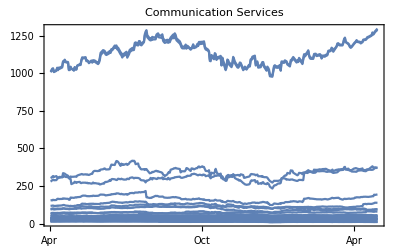

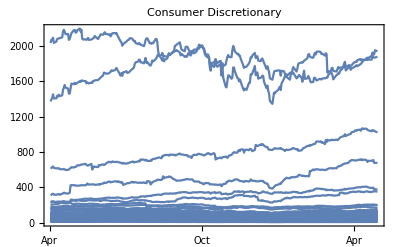

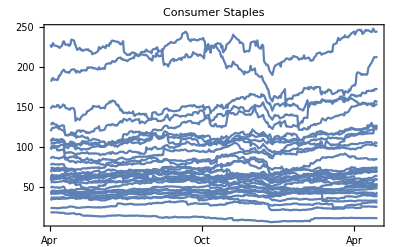

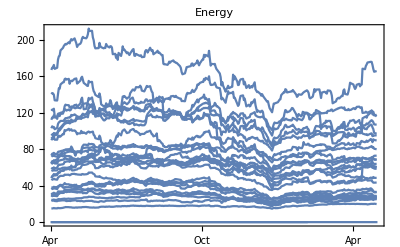

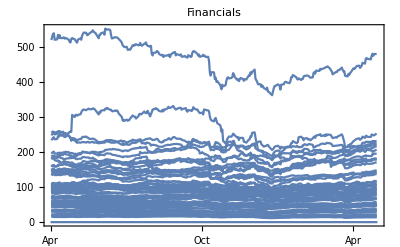

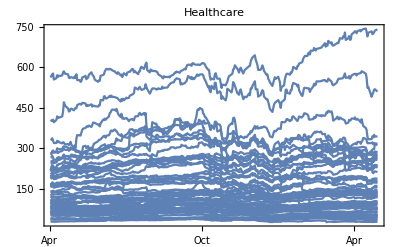

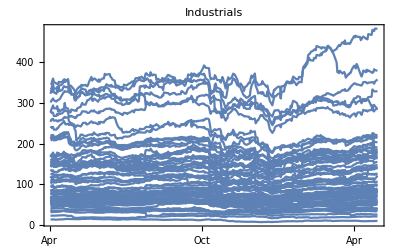

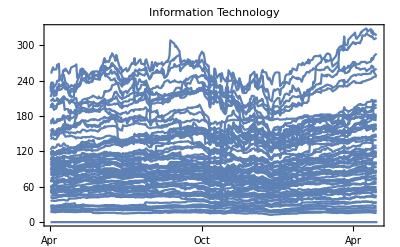

```mathematica
For[i = 1, i ≤ 11, i++,
allPlots[[i]] = Show[allPlots[[i]],PlotLabel-> sectorNames[[i]]]
]
allPlots[[1]]
allPlots[[2]]
allPlots[[3]]
allPlots[[4]]
allPlots[[5]]
allPlots[[6]]
allPlots[[7]]
allPlots[[8]]
allPlots[[9]]
allPlots[[10]]
allPlots[[11]]
```

Upon visual inspection of the stock data, we can see that there are clear correlations between stocks within a particular industry. We observe stocks reflect fluctuations from global forces as well (ex. there’s a noticeable dip in stocks around January, likely due to the government shutdown). At the same time, upon inspection it is possible to see more subtle trends in the behavior of a family of stocks - this motivates our analysis, and we see whether our methods of clustering preserve this structure or induce a new one.

### Initialize Ticker Data for each Stock

We show sample collection of data for one stock, and then encapsulate the data collection into a function to be applied on each stock.

```mathematica
startDate = "Apr 1 2018"; endDate = "Apr 1 2019";
```

```mathematica
google = FinancialData["GOOGL",{startDate,endDate,"Week"}]
```

{{{2018,4,6},1009.95},{{2018,4,13},1036.04},{{2018,4,20},1077.32},{{2018,4,27},1031.45},{{2018,5,4},1051.},{{2018,5,11},1103.38},{{2018,5,18},1069.64},{{2018,5,25},1084.08},{{2018,6,1},1135.},{{2018,6,8},1132.71},{{2018,6,15},1159.27},{{2018,6,22},1169.29},{{2018,6,29},1129.19},{{2018,7,6},1155.08},{{2018,7,13},1204.42},{{2018,7,20},1197.88},{{2018,7,27},1252.89},{{2018,8,3},1238.16},{{2018,8,10},1252.51},{{2018,8,17},1215.85},{{2018,8,24},1236.75},{{2018,8,31},1231.8},{{2018,9,7},1177.59},{{2018,9,14},1177.98},{{2018,9,21},1172.12},{{2018,9,28},1207.08},{{2018,10,5},1167.83},{{2018,10,12},1120.54},{{2018,10,19},1105.18},{{2018,10,26},1083.75},{{2018,11,2},1071.49},{{2018,11,9},1077.02},{{2018,11,16},1068.27},{{2018,11,23},1030.1},{{2018,11,30},1109.65},{{2018,12,7},1046.58},{{2018,12,14},1051.71},{{2018,12,21},991.25},{{2018,12,28},1046.68},{{2019,1,4},1078.07},{{2019,1,11},1064.47},{{2019,1,18},1107.3},{{2019,1,25},1101.51},{{2019,2,1},1118.62},{{2019,2,8},1102.38},{{2019,2,15},1119.63},{{2019,2,22},1116.56},{{2019,3,1},1148.52},{{2019,3,7},1149.97},{{2019,3,15},1190.3},{{2019,3,22},1207.65},{{2019,3,29},1176.89},{{2019,4,1},1198.98}}

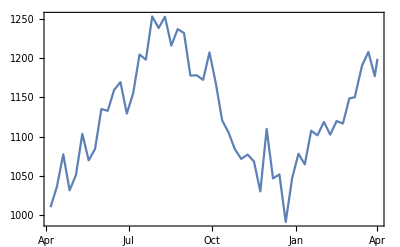

```mathematica
DateListPlot[google,Background-> White]
```

We then transfer the data to a vector, stripping away calendar information.

```mathematica
googleData = google[[All,2]]
```

{1009.95,1036.04,1077.32,1031.45,1051.,1103.38,1069.64,1084.08,1135.,1132.71,1159.27,1169.29,1129.19,1155.08,1204.42,1197.88,1252.89,1238.16,1252.51,1215.85,1236.75,1231.8,1177.59,1177.98,1172.12,1207.08,1167.83,1120.54,1105.18,1083.75,1071.49,1077.02,1068.27,1030.1,1109.65,1046.58,1051.71,991.25,1046.68,1078.07,1064.47,1107.3,1101.51,1118.62,1102.38,1119.63,1116.56,1148.52,1149.97,1190.3,1207.65,1176.89,1198.98}

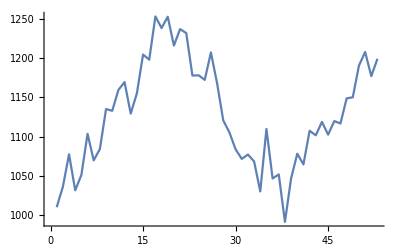

```mathematica
ListLinePlot[googleData,Background-> White]
```

We can readily extract a vector of weekly prices for a given stock - we now seek to create a matrix for each sector to store the family of stocks in that sector. To illustrate this, we show the collection of data for stocks in the Communication Services Sector.

```mathematica
communicationServices
```

{ATVI,CBS,CHTR,CMCSA,CTL,DIS,DISCA,DISCK,DISH,EA,FB,FOX,FOXA,GOOG,GOOGL,IPG,NFLX,NWS,NWSA,OMC,T,TRIP,TTWO,TWTR,VIAB,VZ}

```mathematica
matrix = {};
n = Length[communicationServices]
```

26

Some stocks have incomplete data (i.e., less than 53 weeks of data) - for these stocks, we discard them from our analysis by excluding them from the matrix rather than finding the missing weeks and interpolating between them.

```mathematica
For[i = 1, i≤ n, i++,
tempAllData = FinancialData[communicationServices[[i]],{startDate,endDate,"Week"}];
tempData = tempAllData[[All,2]];
If[Length[tempData]==53,AppendTo[matrix,tempData],Print[communicationServices[[i]]," does not have length 53 - discarding."]];
]
```

FOX does not have length 53 - discarding.

FOXA does not have length 53 - discarding.

```mathematica
matrix = Transpose[matrix];
```

```mathematica
Dimensions[matrix]
```

{53,24}

```mathematica
MatrixForm[matrix]
```

(64.56 | 52.84 | 310.67 | 34.12 | 17.21 | 100.35 | 22.62 | 20.73 | 38.51 | 118.36 | 157.2 | 1007.04 | 1009.95 | 23.15 | 288.85 | 15.8 | 15.5 | 71.74 | 35.63 | 40.15 | 94.63 | 28.1 | 30.9 | 47.48
65.88 | 50.07 | 305.91 | 33.02 | 17.05 | 100.35 | 22.83 | 21.04 | 38.53 | 120.53 | 164.52 | 1029.27 | 1036.04 | 23.33 | 311.65 | 15.9 | 15.72 | 71.86 | 35.14 | 40.52 | 97.19 | 28.76 | 30.7 | 47.66
66.3 | 49.33 | 310.94 | 33.21 | 17.61 | 100.24 | 23.16 | 21.46 | 37.23 | 120.89 | 166.28 | 1072.96 | 1077.32 | 23.99 | 327.77 | 16.35 | 16.17 | 73.74 | 34.67 | 41.62 | 98.38 | 31.91 | 30.66 | 47.9
65.79 | 49.97 | 263.325 | 31.81 | 18.9 | 99.23 | 23.95 | 22.5 | 34.74 | 117.47 | 173.59 | 1030.05 | 1031.45 | 23.89 | 311.76 | 16.25 | 16.01 | 73.91 | 33.04 | 37.27 | 98.63 | 29. | 30.75 | 51.57
69.84 | 53.17 | 276.07 | 31.96 | 18.49 | 101.15 | 23.16 | 21.88 | 33.39 | 123.64 | 176.61 | 1048.21 | 1051. | 23.66 | 320.09 | 16.35 | 16.14 | 74.58 | 32.14 | 38.53 | 108.76 | 31.04 | 30.29 | 48.19
71.7 | 52.52 | 272.81 | 31.9 | 19.6 | 102.07 | 24.03 | 22.84 | 31.38 | 132.81 | 186.99 | 1098.26 | 1103.38 | 24.26 | 326.46 | 15.5 | 15.18 | 75.08 | 32.29 | 48.99 | 116.09 | 32.75 | 30.22 | 48.62
71.99 | 51.75 | 270.17 | 32.72 | 19.29 | 103.93 | 22.57 | 21.42 | 32.35 | 132. | 182.68 | 1066.36 | 1069.64 | 23.77 | 324.18 | 16.1 | 15.63 | 74.96 | 32.05 | 47.92 | 115.81 | 32.63 | 27.24 | 47.74
71.46 | 50.97 | 270.2 | 31.75 | 18.18 | 102.2 | 22.34 | 20.95 | 30.71 | 131.85 | 184.92 | 1075.66 | 1084.08 | 23.02 | 351.29 | 16.05 | 15.58 | 71.96 | 32.51 | 49.48 | 112.02 | 33.63 | 27.5 | 48.52
73.03 | 49.98 | 261.87 | 31.26 | 17.74 | 99.36 | 20.95 | 19.85 | 29.08 | 135.69 | 193.99 | 1119.5 | 1135. | 22.57 | 359.93 | 15.6 | 15.21 | 72.27 | 32.47 | 55.21 | 114.59 | 36.65 | 26.71 | 47.81
74.29 | 51.13 | 277.26 | 32.08 | 17.65 | 103.98 | 23.02 | 21.8 | 32.08 | 137.87 | 189.1 | 1120.87 | 1132.71 | 23.12 | 360.57 | 16.15 | 15.82 | 73.9 | 33.83 | 55.84 | 113.42 | 41.21 | 27.91 | 49.18
77.41 | 56.11 | 297.2 | 33.88 | 18.02 | 108.85 | 27.17 | 25.31 | 34.61 | 146.65 | 195.85 | 1152.26 | 1159.27 | 23.57 | 391.98 | 16.25 | 15.98 | 75.42 | 33.15 | 58.54 | 121.51 | 45.8 | 29.4 | 48.06
75.98 | 56.7 | 299.3 | 33.81 | 18.62 | 106.34 | 28.12 | 26.25 | 34.91 | 141.26 | 201.74 | 1155.48 | 1169.29 | 23.91 | 411.09 | 16.05 | 15.82 | 75.91 | 31.69 | 56.66 | 116.96 | 45.88 | 30.28 | 49.76
76.32 | 56.22 | 293.21 | 32.81 | 18.64 | 104.81 | 27.5 | 25.5 | 33.61 | 141.02 | 194.32 | 1115.65 | 1129.19 | 23.44 | 391.43 | 15.85 | 15.5 | 76.27 | 32.11 | 55.71 | 118.36 | 43.67 | 30.16 | 50.31
77.19 | 58.15 | 304.43 | 33.58 | 19.66 | 104.78 | 27.87 | 25.76 | 34.99 | 145.1 | 203.23 | 1140.17 | 1155.08 | 22.86 | 408.25 | 15.6 | 15.4 | 77.08 | 32.68 | 57.56 | 123.44 | 46.65 | 30. | 51.48
81.5 | 59.01 | 304.84 | 34.7 | 19.88 | 110. | 27.44 | 25.51 | 33.59 | 148.73 | 207.32 | 1188.82 | 1204.42 | 23.3 | 395.8 | 15.8 | 15.59 | 77.51 | 31.67 | 59.13 | 126.35 | 44.49 | 30. | 51.41
79.65 | 57.23 | 288.84 | 34.3 | 18.76 | 111.48 | 26.58 | 24.59 | 30.91 | 147.48 | 209.94 | 1184.91 | 1197.88 | 21.48 | 361.05 | 15.5 | 15.28 | 68.18 | 31.1 | 59.85 | 126.61 | 43.42 | 27.49 | 50.62
75.36 | 54.01 | 286.29 | 35.08 | 18.37 | 112.62 | 26.03 | 24.26 | 30.15 | 133.81 | 174.89 | 1238.5 | 1252.89 | 22.42 | 355.21 | 15.1 | 14.89 | 68.98 | 31.08 | 57.93 | 122.58 | 34.12 | 29.35 | 52.01
71.32 | 53.16 | 303.66 | 35.41 | 18.83 | 114.09 | 27.06 | 24.94 | 34.2 | 130.87 | 177.78 | 1223.71 | 1238.16 | 22.02 | 343.09 | 15.3 | 15.08 | 67.45 | 32.27 | 53.27 | 123.41 | 31.96 | 29.09 | 52.27
70.61 | 52.52 | 302.45 | 35.08 | 21.38 | 112.68 | 25.99 | 24.17 | 35.17 | 131.32 | 180.26 | 1237.61 | 1252.51 | 22.09 | 345.87 | 13.45 | 13.2 | 67.85 | 32.26 | 54.35 | 128.8 | 32.01 | 30.34 | 52.47
69.15 | 53.22 | 299.64 | 35.6 | 23.48 | 112.48 | 26.95 | 24.92 | 35.13 | 128.01 | 173.8 | 1200.96 | 1215.85 | 22.37 | 316.78 | 14.45 | 13.9 | 68.59 | 33.03 | 53.55 | 124.3 | 32.73 | 30.72 | 54.79
74.09 | 53.1 | 300.67 | 36.5 | 22.75 | 111.93 | 28.54 | 26.32 | 35.45 | 128.97 | 174.645 | 1220.65 | 1236.75 | 22.88 | 358.82 | 13.85 | 13.4 | 68.97 | 32.64 | 53.38 | 134.01 | 34.28 | 30.98 | 54.78
72.1 | 53.02 | 310.4 | 36.99 | 21.36 | 112.02 | 27.83 | 25.64 | 35.35 | 113.41 | 175.73 | 1218.19 | 1231.8 | 23.35 | 367.68 | 13.6 | 13.07 | 69.32 | 31.94 | 54.31 | 133.56 | 35.18 | 29.28 | 54.37
73.57 | 56.06 | 305.19 | 36.17 | 21.94 | 110.97 | 27.95 | 25.75 | 35.29 | 114.91 | 163.04 | 1164.83 | 1177.59 | 22.75 | 348.68 | 13.1 | 12.66 | 69.87 | 32.12 | 50.71 | 130.54 | 30.49 | 28.98 | 54.
81.27 | 55.85 | 318.13 | 36.96 | 22.74 | 109.26 | 32.18 | 29.55 | 36.38 | 114.27 | 162.32 | 1172.53 | 1177.98 | 22.71 | 364.56 | 12.85 | 12.44 | 68.98 | 33.6 | 50.39 | 134.11 | 30.12 | 29.85 | 54.55
80.29 | 56.74 | 332.59 | 37.9 | 22.94 | 110.4 | 31.8 | 29.07 | 36.51 | 115.02 | 162.93 | 1166.09 | 1172.12 | 23.18 | 361.19 | 13.2 | 12.81 | 70.9 | 33.78 | 50. | 132.07 | 28.5 | 32.37 | 54.42
83.19 | 57.45 | 325.88 | 35.41 | 21.2 | 116.94 | 32. | 29.58 | 35.76 | 120.49 | 164.46 | 1193.47 | 1207.08 | 22.87 | 374.13 | 13.6 | 13.19 | 68.02 | 33.58 | 51.07 | 137.99 | 28.46 | 33.76 | 53.39
79.59 | 55.32 | 316.04 | 34.56 | 21.86 | 114.78 | 32.93 | 30.24 | 34.3 | 113.73 | 157.33 | 1157.35 | 1167.83 | 23.35 | 351.35 | 13.64 | 13.29 | 70.21 | 33.99 | 50.72 | 130.6 | 28.39 | 32.6 | 54.94
77.92 | 54.32 | 308.74 | 34.62 | 20.66 | 112.61 | 31.76 | 29.05 | 32.92 | 106.1 | 153.74 | 1110.08 | 1120.54 | 21.43 | 339.56 | 13.2 | 12.82 | 68.6 | 32.25 | 45.35 | 129.05 | 27.99 | 31.39 | 53.73
69.75 | 57.2 | 321.34 | 35.98 | 21.99 | 118.9 | 33.4 | 30.21 | 34.91 | 102.11 | 154.05 | 1096.46 | 1105.18 | 24.65 | 332.67 | 13.38 | 13.13 | 77.07 | 32.87 | 46.6 | 122.45 | 28.83 | 33.23 | 54.9
68.84 | 53.83 | 295.01 | 35.24 | 19.37 | 113.19 | 30.13 | 27.42 | 28.26 | 96.22 | 145.37 | 1071.47 | 1083.75 | 22.87 | 299.83 | 12.84 | 12.67 | 71.04 | 29.09 | 47.44 | 120.06 | 32.36 | 29.98 | 55.51
68.99 | 56.17 | 317.87 | 37.66 | 20.97 | 115.18 | 32.31 | 29.14 | 30.93 | 92.46 | 150.35 | 1057.79 | 1071.49 | 22.8 | 309.1 | 13.36 | 13.17 | 74.69 | 30.52 | 53.63 | 128.37 | 34.3 | 31.67 | 56.63
55.01 | 57.55 | 321.11 | 38.34 | 18.91 | 118. | 32.98 | 29.71 | 31.73 | 88.89 | 144.96 | 1066.15 | 1077.02 | 23.84 | 303.47 | 14.4 | 14.24 | 75.57 | 30.69 | 63.3 | 113.05 | 34.08 | 32.1 | 58.46
50.94 | 57.49 | 328.54 | 38.59 | 19.17 | 116.19 | 31.44 | 28.56 | 32.85 | 85.97 | 139.53 | 1061.49 | 1068.27 | 24.03 | 286.21 | 13.88 | 13.57 | 77.1 | 30.29 | 63.67 | 113.93 | 33.67 | 32.99 | 60.21
50.05 | 53.92 | 309.43 | 37.39 | 17.88 | 112.08 | 30.43 | 27.53 | 30.67 | 82.67 | 131.73 | 1023.88 | 1030.1 | 22.7 | 258.82 | 12.96 | 12.61 | 74.88 | 29.36 | 58.65 | 105.5 | 31.12 | 31.04 | 58.64
49.88 | 54.18 | 329.2 | 39.01 | 18.8 | 115.49 | 30.72 | 27.93 | 32.76 | 84.07 | 140.61 | 1094.43 | 1109.65 | 23.5 | 286.13 | 13.4 | 12.98 | 76.97 | 31.24 | 64.06 | 109.67 | 31.45 | 30.86 | 60.3
47.23 | 51.1 | 315.7 | 37.41 | 17.47 | 111.98 | 28.93 | 26.9 | 31.93 | 82.52 | 137.42 | 1036.58 | 1046.58 | 22.64 | 265.14 | 12.71 | 12.36 | 75.5 | 30.14 | 61.61 | 102.67 | 32.83 | 29.91 | 57.68
47.75 | 48.05 | 309.42 | 36.34 | 17. | 112.2 | 27.97 | 26.02 | 30.65 | 80.16 | 144.06 | 1042.1 | 1051.71 | 22.21 | 266.84 | 12.46 | 12.25 | 75.78 | 30.22 | 60.7 | 103.46 | 35.87 | 28.57 | 57.08
45.85 | 43.36 | 283.93 | 33.75 | 14.9 | 104.22 | 25.05 | 23.49 | 25.02 | 76.57 | 124.95 | 979.54 | 991.25 | 20.15 | 246.39 | 11.25 | 11.04 | 70.23 | 28.31 | 52.48 | 101.37 | 27.31 | 25.68 | 54.92
46.8 | 43.41 | 285.08 | 34.35 | 15.27 | 107.3 | 24.64 | 22.83 | 24.96 | 79.3 | 133.2 | 1037.08 | 1046.68 | 20.43 | 256.08 | 11.46 | 11.25 | 72.32 | 28.46 | 53.55 | 104.57 | 28.43 | 25.89 | 55.27
47.17 | 47.17 | 302.74 | 35.81 | 15.95 | 109.61 | 26.14 | 24.35 | 28.28 | 84.42 | 137.95 | 1070.71 | 1078.07 | 20.73 | 297.57 | 11.96 | 11.77 | 73.34 | 30.34 | 53.92 | 101.7 | 29.95 | 26.9 | 56.36
46.54 | 47.97 | 294.54 | 35.63 | 16.27 | 112.65 | 27.12 | 25.18 | 28.15 | 90.7 | 143.8 | 1057.19 | 1064.47 | 22.28 | 337.59 | 12.48 | 12.24 | 76.51 | 30.87 | 56.02 | 109.03 | 32.87 | 29.44 | 58.02
48.65 | 49.24 | 291.4 | 36.21 | 15.83 | 111.04 | 27.71 | 25.92 | 29.8 | 92.52 | 150.04 | 1098.26 | 1107.3 | 22.25 | 339.1 | 12.68 | 12.52 | 76. | 30.96 | 59.04 | 108.26 | 33.27 | 30.08 | 57.09
47.8 | 49.17 | 291.41 | 35.78 | 14.99 | 111.09 | 27.68 | 25.77 | 30.08 | 91.74 | 149.01 | 1090.99 | 1101.51 | 22.41 | 338.05 | 12.8 | 12.69 | 76.4 | 30.66 | 57.23 | 103.7 | 32.9 | 28.99 | 56.4
46.01 | 49.67 | 340.95 | 36.79 | 15.25 | 111.3 | 28.56 | 26.68 | 30.44 | 91.22 | 165.71 | 1110.75 | 1118.62 | 22.67 | 339.85 | 12.86 | 12.74 | 77.6 | 30. | 57.62 | 104.95 | 33.19 | 29.53 | 54.55
43.41 | 49.56 | 344.16 | 37.6 | 14.21 | 111.51 | 29.19 | 27.34 | 31.54 | 97.6 | 167.33 | 1095.06 | 1102.38 | 22.11 | 347.57 | 12.67 | 12.46 | 74.7 | 29.55 | 59.2 | 97.14 | 30.01 | 29.19 | 53.95
44.6 | 50.64 | 349.06 | 37.77 | 13.74 | 112.59 | 29.3 | 27.65 | 30.9 | 106.84 | 162.5 | 1113.65 | 1119.63 | 23.38 | 356.87 | 12.93 | 12.75 | 75. | 30.47 | 56.81 | 93.3 | 31.23 | 29.15 | 55.16
41.5 | 51.69 | 350.08 | 38.61 | 13.44 | 115.25 | 29.21 | 27.51 | 32.82 | 95.92 | 161.89 | 1110.37 | 1116.56 | 23.75 | 363.02 | 13.21 | 12.98 | 75.63 | 31.15 | 54.94 | 87.07 | 31.71 | 29.19 | 56.92
42.84 | 50.79 | 346.58 | 39.1 | 12.97 | 114.01 | 29.08 | 27.51 | 32.23 | 97.41 | 162.28 | 1140.99 | 1148.52 | 23.13 | 357.32 | 13.56 | 13.25 | 76.72 | 30.82 | 52.54 | 88.32 | 30.62 | 29.45 | 56.96
42.03 | 49.01 | 337.54 | 38.19 | 12.3 | 113.81 | 28.92 | 27.29 | 31.75 | 98.36 | 169.6 | 1142.32 | 1149.97 | 22.25 | 349.6 | 13.05 | 12.8 | 73.98 | 29.96 | 50.91 | 87.04 | 30.04 | 28.86 | 56.53
44.63 | 47.7 | 355.92 | 40.47 | 12.09 | 114.96 | 27.43 | 25.9 | 32.57 | 98.98 | 165.98 | 1184.46 | 1190.3 | 22.34 | 361.46 | 12.74 | 12.64 | 75.47 | 30.67 | 51.59 | 93.55 | 31.22 | 27.99 | 58.39
46.87 | 45.06 | 360.78 | 39.46 | 12.17 | 108.23 | 26.67 | 25.45 | 31.27 | 102.34 | 164.34 | 1205.5 | 1207.65 | 21.13 | 361.01 | 12.64 | 12.63 | 73.07 | 31.07 | 50.75 | 96.02 | 33.02 | 25.34 | 59.76
45.53 | 47.53 | 346.91 | 39.98 | 11.99 | 111.03 | 27.02 | 25.42 | 31.69 | 101.63 | 166.69 | 1173.31 | 1176.89 | 21.01 | 356.56 | 12.49 | 12.44 | 72.99 | 31.36 | 51.45 | 94.37 | 32.88 | 28.07 | 59.13
47.12 | 48.21 | 346.22 | 40.31 | 12.37 | 112.51 | 27.75 | 26.18 | 33.14 | 102.67 | 168.7 | 1194.43 | 1198.98 | 21.17 | 366.96 | 12.61 | 12.52 | 73.62 | 31.95 | 52.74 | 95.69 | 33.44 | 28.89 | 59.09)

This gives us the desired matrix, where each column represents a stock sampled at each week. We encapsulate the above into the following function:

```mathematica
sampleWeeklyStock[familyOfStocks_]:=Module[{matrix,n,tempAllData,tempData},
matrix = {};
n = Length[familyOfStocks];
For[i = 1, i≤ n, i++,
Print[i," out of ",n];
tempAllData = FinancialData[familyOfStocks[[i]],{startDate,endDate,"Week"}];
tempData = tempAllData[[All,2]];
If[Length[tempData]==53,AppendTo[matrix,tempData],Print[familyOfStocks[[i]]," does not have length 53 - discarding."]];
] ;
Return[Transpose[matrix]]
]
```

We now define the matrix for each process.

(Note: This data is explicitly stored in this cell to save time from not having to download the stock data - I recommend running this cell to initialize the matrices instead creating them from scratch). CAUTION: Long Cell, Don’t Expand.

```mathematica
communicationServicesM ={{64.55999755859375,52.84000015258789,310.6700134277344,34.119998931884766,17.209999084472656,100.3499984741211,22.6200008392334,20.729999542236328,38.5099983215332,118.36000061035156,157.1999969482422,1007.0399780273438,1009.9500122070312,23.149999618530273,288.8500061035156,15.800000190734863,15.5,71.73999786376953,35.630001068115234,40.150001525878906,94.62999725341797,28.100000381469727,30.899999618530273,47.47999954223633},{65.87999725341797,50.06999969482422,305.9100036621094,33.02000045776367,17.049999237060547,100.3499984741211,22.829999923706055,21.040000915527344,38.529998779296875,120.52999877929688,164.52000427246094,1029.27001953125,1036.0400390625,23.329999923706055,311.6499938964844,15.899999618530273,15.720000267028809,71.86000061035156,35.13999938964844,40.52000045776367,97.19000244140625,28.760000228881836,30.700000762939453,47.65999984741211},{66.30000305175781,49.33000183105469,310.94000244140625,33.209999084472656,17.610000610351562,100.23999786376953,23.15999984741211,21.459999084472656,37.22999954223633,120.88999938964844,166.27999877929688,1072.9599609375,1077.3199462890625,23.989999771118164,327.7699890136719,16.350000381469727,16.170000076293945,73.73999786376953,34.66999816894531,41.619998931884766,98.37999725341797,31.90999984741211,30.65999984741211,47.900001525878906},{65.79000091552734,49.970001220703125,263.32501220703125,31.809999465942383,18.899999618530273,99.2300033569336,23.950000762939453,22.5,34.7400016784668,117.47000122070312,173.58999633789062,1030.050048828125,1031.449951171875,23.889999389648438,311.760009765625,16.25,16.010000228881836,73.91000366210938,33.040000915527344,37.27000045776367,98.62999725341797,29.,30.75,51.56999969482422},{69.83999633789062,53.16999816894531,276.07000732421875,31.959999084472656,18.489999771118164,101.1500015258789,23.15999984741211,21.8799991607666,33.38999938964844,123.63999938964844,176.61000061035156,1048.2099609375,1051.,23.65999984741211,320.0899963378906,16.350000381469727,16.139999389648438,74.58000183105469,32.13999938964844,38.529998779296875,108.76000213623047,31.040000915527344,30.290000915527344,48.189998626708984},{71.69999694824219,52.52000045776367,272.80999755859375,31.899999618530273,19.600000381469727,102.06999969482422,24.030000686645508,22.84000015258789,31.3799991607666,132.80999755859375,186.99000549316406,1098.260009765625,1103.3800048828125,24.260000228881836,326.4599914550781,15.5,15.180000305175781,75.08000183105469,32.290000915527344,48.9900016784668,116.08999633789062,32.75,30.219999313354492,48.619998931884766},{71.98999786376953,51.75,270.1700134277344,32.720001220703125,19.290000915527344,103.93000030517578,22.56999969482422,21.420000076293945,32.349998474121094,132.,182.67999267578125,1066.3599853515625,1069.6400146484375,23.770000457763672,324.17999267578125,16.100000381469727,15.630000114440918,74.95999908447266,32.04999923706055,47.91999816894531,115.80999755859375,32.630001068115234,27.239999771118164,47.7400016784668},{71.45999908447266,50.970001220703125,270.20001220703125,31.75,18.18000030517578,102.19999694824219,22.34000015258789,20.950000762939453,30.709999084472656,131.85000610351562,184.9199981689453,1075.6600341796875,1084.0799560546875,23.020000457763672,351.2900085449219,16.049999237060547,15.579999923706055,71.95999908447266,32.5099983215332,49.47999954223633,112.0199966430664,33.630001068115234,27.5,48.52000045776367},{73.02999877929688,49.97999954223633,261.8699951171875,31.260000228881836,17.739999771118164,99.36000061035156,20.950000762939453,19.850000381469727,29.079999923706055,135.69000244140625,193.99000549316406,1119.5,1135.,22.56999969482422,359.92999267578125,15.600000381469727,15.210000038146973,72.2699966430664,32.470001220703125,55.209999084472656,114.58999633789062,36.650001525878906,26.709999084472656,47.810001373291016},{74.29000091552734,51.130001068115234,277.260009765625,32.08000183105469,17.649999618530273,103.9800033569336,23.020000457763672,21.799999237060547,32.08000183105469,137.8699951171875,189.10000610351562,1120.8699951171875,1132.7099609375,23.1200008392334,360.57000732421875,16.149999618530273,15.819999694824219,73.9000015258789,33.83000183105469,55.84000015258789,113.41999816894531,41.209999084472656,27.90999984741211,49.18000030517578},{77.41000366210938,56.11000061035156,297.20001220703125,33.880001068115234,18.020000457763672,108.8499984741211,27.170000076293945,25.309999465942383,34.61000061035156,146.64999389648438,195.85000610351562,1152.260009765625,1159.27001953125,23.56999969482422,391.9800109863281,16.25,15.979999542236328,75.41999816894531,33.150001525878906,58.540000915527344,121.51000213623047,45.79999923706055,29.399999618530273,48.060001373291016},{75.9800033569336,56.70000076293945,299.29998779296875,33.810001373291016,18.6200008392334,106.33999633789062,28.1200008392334,26.25,34.90999984741211,141.25999450683594,201.74000549316406,1155.47998046875,1169.2900390625,23.90999984741211,411.0899963378906,16.049999237060547,15.819999694824219,75.91000366210938,31.690000534057617,56.65999984741211,116.95999908447266,45.880001068115234,30.280000686645508,49.7599983215332},{76.31999969482422,56.220001220703125,293.2099914550781,32.810001373291016,18.639999389648438,104.80999755859375,27.5,25.5,33.61000061035156,141.02000427246094,194.32000732421875,1115.6500244140625,1129.18994140625,23.440000534057617,391.42999267578125,15.850000381469727,15.5,76.2699966430664,32.11000061035156,55.709999084472656,118.36000061035156,43.66999816894531,30.15999984741211,50.310001373291016},{77.19000244140625,58.150001525878906,304.42999267578125,33.58000183105469,19.65999984741211,104.77999877929688,27.8700008392334,25.760000228881836,34.9900016784668,145.10000610351562,203.22999572753906,1140.1700439453125,1155.0799560546875,22.860000610351562,408.25,15.600000381469727,15.399999618530273,77.08000183105469,32.68000030517578,57.560001373291016,123.44000244140625,46.650001525878906,30.,51.47999954223633},{81.5,59.0099983215332,304.8399963378906,34.70000076293945,19.8799991607666,110.,27.440000534057617,25.510000228881836,33.59000015258789,148.72999572753906,207.32000732421875,1188.8199462890625,1204.4200439453125,23.299999237060547,395.79998779296875,15.800000190734863,15.59000015258789,77.51000213623047,31.670000076293945,59.130001068115234,126.3499984741211,44.4900016784668,30.,51.40999984741211},{79.6500015258789,57.22999954223633,288.8399963378906,34.29999923706055,18.760000228881836,111.4800033569336,26.579999923706055,24.59000015258789,30.90999984741211,147.47999572753906,209.94000244140625,1184.9100341796875,1197.8800048828125,21.479999542236328,361.04998779296875,15.5,15.279999732971191,68.18000030517578,31.100000381469727,59.849998474121094,126.61000061035156,43.41999816894531,27.489999771118164,50.619998931884766},{75.36000061035156,54.0099983215332,286.2900085449219,35.08000183105469,18.3700008392334,112.62000274658203,26.030000686645508,24.260000228881836,30.149999618530273,133.80999755859375,174.88999938964844,1238.5,1252.8900146484375,22.420000076293945,355.2099914550781,15.100000381469727,14.890000343322754,68.9800033569336,31.079999923706055,57.93000030517578,122.58000183105469,34.119998931884766,29.350000381469727,52.0099983215332},{71.31999969482422,53.15999984741211,303.6600036621094,35.40999984741211,18.829999923706055,114.08999633789062,27.059999465942383,24.940000534057617,34.20000076293945,130.8699951171875,177.77999877929688,1223.7099609375,1238.1600341796875,22.020000457763672,343.0899963378906,15.300000190734863,15.079999923706055,67.44999694824219,32.27000045776367,53.27000045776367,123.41000366210938,31.959999084472656,29.09000015258789,52.27000045776367},{70.61000061035156,52.52000045776367,302.45001220703125,35.08000183105469,21.3799991607666,112.68000030517578,25.989999771118164,24.170000076293945,35.16999816894531,131.32000732421875,180.25999450683594,1237.6099853515625,1252.510009765625,22.09000015258789,345.8699951171875,13.449999809265137,13.199999809265137,67.8499984741211,32.2599983215332,54.349998474121094,128.8000030517578,32.0099983215332,30.34000015258789,52.470001220703125},{69.1500015258789,53.220001220703125,299.6400146484375,35.599998474121094,23.479999542236328,112.4800033569336,26.950000762939453,24.920000076293945,35.130001068115234,128.00999450683594,173.8000030517578,1200.9599609375,1215.8499755859375,22.3700008392334,316.7799987792969,14.449999809265137,13.899999618530273,68.58999633789062,33.029998779296875,53.54999923706055,124.30000305175781,32.72999954223633,30.719999313354492,54.790000915527344},{74.08999633789062,53.099998474121094,300.6700134277344,36.5,22.75,111.93000030517578,28.540000915527344,26.31999969482422,35.45000076293945,128.97000122070312,174.64500427246094,1220.6500244140625,1236.75,22.8799991607666,358.82000732421875,13.850000381469727,13.399999618530273,68.97000122070312,32.63999938964844,53.380001068115234,134.00999450683594,34.279998779296875,30.979999542236328,54.779998779296875},{72.0999984741211,53.02000045776367,310.3999938964844,36.9900016784668,21.360000610351562,112.0199966430664,27.829999923706055,25.639999389648438,35.349998474121094,113.41000366210938,175.72999572753906,1218.18994140625,1231.800048828125,23.350000381469727,367.67999267578125,13.600000381469727,13.069999694824219,69.31999969482422,31.940000534057617,54.310001373291016,133.55999755859375,35.18000030517578,29.280000686645508,54.369998931884766},{73.56999969482422,56.060001373291016,305.19000244140625,36.16999816894531,21.940000534057617,110.97000122070312,27.950000762939453,25.75,35.290000915527344,114.91000366210938,163.0399932861328,1164.8299560546875,1177.5899658203125,22.75,348.67999267578125,13.100000381469727,12.65999984741211,69.87000274658203,32.119998931884766,50.709999084472656,130.5399932861328,30.489999771118164,28.979999542236328,54.},{81.2699966430664,55.849998474121094,318.1300048828125,36.959999084472656,22.739999771118164,109.26000213623047,32.18000030517578,29.549999237060547,36.380001068115234,114.2699966430664,162.32000732421875,1172.530029296875,1177.97998046875,22.709999084472656,364.55999755859375,12.850000381469727,12.4399995803833,68.9800033569336,33.599998474121094,50.38999938964844,134.11000061035156,30.1200008392334,29.850000381469727,54.54999923706055},{80.29000091552734,56.7400016784668,332.5899963378906,37.900001525878906,22.940000534057617,110.4000015258789,31.799999237060547,29.06999969482422,36.5099983215332,115.0199966430664,162.92999267578125,1166.0899658203125,1172.1199951171875,23.18000030517578,361.19000244140625,13.199999809265137,12.8100004196167,70.9000015258789,33.779998779296875,50.,132.07000732421875,28.5,32.369998931884766,54.41999816894531},{83.19000244140625,57.45000076293945,325.8800048828125,35.40999984741211,21.200000762939453,116.94000244140625,32.,29.579999923706055,35.7599983215332,120.48999786376953,164.4600067138672,1193.469970703125,1207.0799560546875,22.8700008392334,374.1300048828125,13.600000381469727,13.1899995803833,68.0199966430664,33.58000183105469,51.06999969482422,137.99000549316406,28.459999084472656,33.7599983215332,53.38999938964844},{79.58999633789062,55.31999969482422,316.0400085449219,34.560001373291016,21.860000610351562,114.77999877929688,32.93000030517578,30.239999771118164,34.29999923706055,113.7300033569336,157.3300018310547,1157.3499755859375,1167.8299560546875,23.350000381469727,351.3500061035156,13.640000343322754,13.289999961853027,70.20999908447266,33.9900016784668,50.720001220703125,130.60000610351562,28.389999389648438,32.599998474121094,54.939998626708984},{77.91999816894531,54.31999969482422,308.739990234375,34.619998931884766,20.65999984741211,112.61000061035156,31.760000228881836,29.049999237060547,32.91999816894531,106.0999984741211,153.74000549316406,1110.0799560546875,1120.5400390625,21.43000030517578,339.55999755859375,13.199999809265137,12.819999694824219,68.5999984741211,32.25,45.349998474121094,129.0500030517578,27.989999771118164,31.389999389648438,53.72999954223633},{69.75,57.20000076293945,321.3399963378906,35.97999954223633,21.989999771118164,118.9000015258789,33.400001525878906,30.209999084472656,34.90999984741211,102.11000061035156,154.0500030517578,1096.4599609375,1105.1800537109375,24.649999618530273,332.6700134277344,13.380000114440918,13.130000114440918,77.06999969482422,32.869998931884766,46.599998474121094,122.44999694824219,28.829999923706055,33.22999954223633,54.900001525878906},{68.83999633789062,53.83000183105469,295.010009765625,35.2400016784668,19.3700008392334,113.19000244140625,30.1299991607666,27.420000076293945,28.260000228881836,96.22000122070312,145.3699951171875,1071.469970703125,1083.75,22.8700008392334,299.8299865722656,12.84000015258789,12.670000076293945,71.04000091552734,29.09000015258789,47.439998626708984,120.05999755859375,32.36000061035156,29.979999542236328,55.5099983215332},{68.98999786376953,56.16999816894531,317.8699951171875,37.65999984741211,20.969999313354492,115.18000030517578,32.310001373291016,29.139999389648438,30.93000030517578,92.45999908447266,150.35000610351562,1057.7900390625,1071.489990234375,22.799999237060547,309.1000061035156,13.359999656677246,13.170000076293945,74.69000244140625,30.520000457763672,53.630001068115234,128.3699951171875,34.29999923706055,31.670000076293945,56.630001068115234},{55.0099983215332,57.54999923706055,321.1099853515625,38.34000015258789,18.90999984741211,118.,32.97999954223633,29.709999084472656,31.729999542236328,88.88999938964844,144.9600067138672,1066.1500244140625,1077.02001953125,23.84000015258789,303.4700012207031,14.399999618530273,14.239999771118164,75.56999969482422,30.690000534057617,63.29999923706055,113.05000305175781,34.08000183105469,32.099998474121094,58.459999084472656},{50.939998626708984,57.4900016784668,328.5400085449219,38.59000015258789,19.170000076293945,116.19000244140625,31.440000534057617,28.559999465942383,32.849998474121094,85.97000122070312,139.52999877929688,1061.489990234375,1068.27001953125,24.030000686645508,286.2099914550781,13.880000114440918,13.569999694824219,77.0999984741211,30.290000915527344,63.66999816894531,113.93000030517578,33.66999816894531,32.9900016784668,60.209999084472656},{50.04999923706055,53.91999816894531,309.42999267578125,37.38999938964844,17.8799991607666,112.08000183105469,30.43000030517578,27.530000686645508,30.670000076293945,82.66999816894531,131.72999572753906,1023.8800048828125,1030.0999755859375,22.700000762939453,258.82000732421875,12.960000038146973,12.609999656677246,74.87999725341797,29.360000610351562,58.650001525878906,105.5,31.1200008392334,31.040000915527344,58.63999938964844},{49.880001068115234,54.18000030517578,329.20001220703125,39.0099983215332,18.799999237060547,115.48999786376953,30.719999313354492,27.93000030517578,32.7599983215332,84.06999969482422,140.61000061035156,1094.4300537109375,1109.6500244140625,23.5,286.1300048828125,13.399999618530273,12.979999542236328,76.97000122070312,31.239999771118164,64.05999755859375,109.66999816894531,31.450000762939453,30.860000610351562,60.29999923706055},{47.22999954223633,51.099998474121094,315.70001220703125,37.40999984741211,17.469999313354492,111.9800033569336,28.93000030517578,26.899999618530273,31.93000030517578,82.5199966430664,137.4199981689453,1036.5799560546875,1046.5799560546875,22.639999389648438,265.1400146484375,12.710000038146973,12.359999656677246,75.5,30.139999389648438,61.61000061035156,102.66999816894531,32.83000183105469,29.90999984741211,57.68000030517578},{47.75,48.04999923706055,309.4200134277344,36.34000015258789,17.,112.19999694824219,27.969999313354492,26.020000457763672,30.649999618530273,80.16000366210938,144.05999755859375,1042.0999755859375,1051.7099609375,22.209999084472656,266.8399963378906,12.460000038146973,12.25,75.77999877929688,30.219999313354492,60.70000076293945,103.45999908447266,35.869998931884766,28.56999969482422,57.08000183105469},{45.849998474121094,43.36000061035156,283.92999267578125,33.75,14.899999618530273,104.22000122070312,25.049999237060547,23.489999771118164,25.020000457763672,76.56999969482422,124.94999694824219,979.5399780273438,991.25,20.149999618530273,246.38999938964844,11.25,11.039999961853027,70.2300033569336,28.309999465942383,52.47999954223633,101.37000274658203,27.309999465942383,25.68000030517578,54.91999816894531},{46.79999923706055,43.40999984741211,285.0799865722656,34.349998474121094,15.270000457763672,107.30000305175781,24.639999389648438,22.829999923706055,24.959999084472656,79.30000305175781,133.1999969482422,1037.0799560546875,1046.6800537109375,20.43000030517578,256.0799865722656,11.460000038146973,11.25,72.31999969482422,28.459999084472656,53.54999923706055,104.56999969482422,28.43000030517578,25.889999389648438,55.27000045776367},{47.16999816894531,47.16999816894531,302.739990234375,35.810001373291016,15.949999809265137,109.61000061035156,26.139999389648438,24.350000381469727,28.280000686645508,84.41999816894531,137.9499969482422,1070.7099609375,1078.0699462890625,20.729999542236328,297.57000732421875,11.960000038146973,11.770000457763672,73.33999633789062,30.34000015258789,53.91999816894531,101.69999694824219,29.950000762939453,26.899999618530273,56.36000061035156},{46.540000915527344,47.970001220703125,294.5400085449219,35.630001068115234,16.270000457763672,112.6500015258789,27.1200008392334,25.18000030517578,28.149999618530273,90.69999694824219,143.8000030517578,1057.18994140625,1064.469970703125,22.280000686645508,337.5899963378906,12.479999542236328,12.239999771118164,76.51000213623047,30.8700008392334,56.02000045776367,109.02999877929688,32.869998931884766,29.440000534057617,58.02000045776367},{48.650001525878906,49.2400016784668,291.3999938964844,36.209999084472656,15.829999923706055,111.04000091552734,27.709999084472656,25.920000076293945,29.799999237060547,92.5199966430664,150.0399932861328,1098.260009765625,1107.300048828125,22.25,339.1000061035156,12.680000305175781,12.520000457763672,76.,30.959999084472656,59.040000915527344,108.26000213623047,33.27000045776367,30.079999923706055,57.09000015258789},{47.79999923706055,49.16999816894531,291.4100036621094,35.779998779296875,14.989999771118164,111.08999633789062,27.68000030517578,25.770000457763672,30.079999923706055,91.73999786376953,149.00999450683594,1090.989990234375,1101.510009765625,22.40999984741211,338.04998779296875,12.800000190734863,12.6899995803833,76.4000015258789,30.65999984741211,57.22999954223633,103.69999694824219,32.900001525878906,28.989999771118164,56.400001525878906},{46.0099983215332,49.66999816894531,340.95001220703125,36.790000915527344,15.25,111.30000305175781,28.559999465942383,26.68000030517578,30.440000534057617,91.22000122070312,165.7100067138672,1110.75,1118.6199951171875,22.670000076293945,339.8500061035156,12.859999656677246,12.739999771118164,77.5999984741211,30.,57.619998931884766,104.94999694824219,33.189998626708984,29.530000686645508,54.54999923706055},{43.40999984741211,49.560001373291016,344.1600036621094,37.599998474121094,14.210000038146973,111.51000213623047,29.190000534057617,27.34000015258789,31.540000915527344,97.5999984741211,167.3300018310547,1095.06005859375,1102.3800048828125,22.110000610351562,347.57000732421875,12.670000076293945,12.460000038146973,74.69999694824219,29.549999237060547,59.20000076293945,97.13999938964844,30.010000228881836,29.190000534057617,53.95000076293945},{44.599998474121094,50.63999938964844,349.05999755859375,37.77000045776367,13.739999771118164,112.58999633789062,29.299999237060547,27.649999618530273,30.899999618530273,106.83999633789062,162.5,1113.6500244140625,1119.6300048828125,23.3799991607666,356.8699951171875,12.930000305175781,12.75,75.,30.469999313354492,56.810001373291016,93.30000305175781,31.229999542236328,29.149999618530273,55.15999984741211},{41.5,51.689998626708984,350.0799865722656,38.61000061035156,13.4399995803833,115.25,29.209999084472656,27.510000228881836,32.81999969482422,95.91999816894531,161.88999938964844,1110.3699951171875,1116.56005859375,23.75,363.0199890136719,13.210000038146973,12.979999542236328,75.62999725341797,31.149999618530273,54.939998626708984,87.06999969482422,31.709999084472656,29.190000534057617,56.91999816894531},{42.84000015258789,50.790000915527344,346.5799865722656,39.099998474121094,12.970000267028809,114.01000213623047,29.079999923706055,27.510000228881836,32.22999954223633,97.41000366210938,162.27999877929688,1140.989990234375,1148.52001953125,23.1299991607666,357.32000732421875,13.5600004196167,13.25,76.72000122070312,30.81999969482422,52.540000915527344,88.31999969482422,30.6200008392334,29.450000762939453,56.959999084472656},{42.029998779296875,49.0099983215332,337.5400085449219,38.189998626708984,12.300000190734863,113.80999755859375,28.920000076293945,27.290000915527344,31.75,98.36000061035156,169.60000610351562,1142.3199462890625,1149.969970703125,22.25,349.6000061035156,13.050000190734863,12.800000190734863,73.9800033569336,29.959999084472656,50.90999984741211,87.04000091552734,30.040000915527344,28.860000610351562,56.529998779296875},{44.630001068115234,47.70000076293945,355.9200134277344,40.470001220703125,12.09000015258789,114.95999908447266,27.43000030517578,25.899999618530273,32.56999969482422,98.9800033569336,165.97999572753906,1184.4599609375,1190.300048828125,22.34000015258789,361.4599914550781,12.739999771118164,12.640000343322754,75.47000122070312,30.670000076293945,51.59000015258789,93.55000305175781,31.219999313354492,27.989999771118164,58.38999938964844},{46.869998931884766,45.060001373291016,360.7799987792969,39.459999084472656,12.170000076293945,108.2300033569336,26.670000076293945,25.450000762939453,31.270000457763672,102.33999633789062,164.33999633789062,1205.5,1207.6500244140625,21.1299991607666,361.010009765625,12.640000343322754,12.630000114440918,73.06999969482422,31.06999969482422,50.75,96.0199966430664,33.02000045776367,25.34000015258789,59.7599983215332},{45.529998779296875,47.529998779296875,346.9100036621094,39.97999954223633,11.989999771118164,111.02999877929688,27.020000457763672,25.420000076293945,31.690000534057617,101.62999725341797,166.69000244140625,1173.31005859375,1176.8900146484375,21.010000228881836,356.55999755859375,12.489999771118164,12.4399995803833,72.98999786376953,31.360000610351562,51.45000076293945,94.37000274658203,32.880001068115234,28.06999969482422,59.130001068115234},{47.119998931884766,48.209999084472656,346.2200012207031,40.310001373291016,12.369999885559082,112.51000213623047,27.75,26.18000030517578,33.13999938964844,102.66999816894531,168.6999969482422,1194.4300537109375,1198.97998046875,21.170000076293945,366.9599914550781,12.609999656677246,12.520000457763672,73.62000274658203,31.950000762939453,52.7400016784668,95.69000244140625,33.439998626708984,28.889999389648438,59.09000015258789}};
matrix = communicationServicesM;
consumerDiscretionaryM={{111.91000366210938,1405.22998046875,83.81999969482422,620.3599853515625,70.48999786376953,2033.4100341796875,51.27000045776367,64.51000213623047,318.07000732421875,64.86,94.97000122070312,45.349998474121094,98.72000122070312,86.86000061035156,39.09000015258789,107.55000305175781,11.180000305175781,46.459999084472656,37.68000030517578,89.26000213623047,30.84000015258789,58.41999816894531,84.43000030517578,18.8799991607666,174.4499969482422,77.51000213623047,42.189998626708984,25.510000228881836,48.029998779296875,60.29999923706055,64.,38.20000076293945,43.93000030517578,61.58000183105469,38.18000030517578,88.23999786376953,29.799999237060547,130.92999267578125,13.119999885559082,161.25,34.130001068115234,236.0800018310547,53.209999084472656,67.55000305175781,25.790000915527344,237.19000244140625,30.030000686645508,156.72999572753906,114.83000183105469,111.7699966430664,77.44999694824219,58.34000015258789,72.29000091552734,95.58000183105469,83.44000244140625,52.470001220703125,59.70000076293945,14.75,16.979999542236328,208.25999450683594,76.30999755859375,148.52000427246094,178.49000549316406,84.45999908447266},{106.61000061035156,1430.7900390625,85.51000213623047,606.8300170898438,71.12999725341797,2085.860107421875,52.86000061035156,62.939998626708984,318.3599853515625,65.38,96.27999877929688,44.47999954223633,97.12999725341797,87.72000122070312,39.900001525878906,107.19999694824219,11.279999732971191,45.20000076293945,38.72999954223633,89.5199966430664,30.049999237060547,59.029998779296875,87.76000213623047,18.1299991607666,172.8000030517578,79.61000061035156,42.20000076293945,26.049999237060547,47.38999938964844,61.720001220703125,61.34000015258789,36.18000030517578,44.33000183105469,56.939998626708984,38.189998626708984,86.2300033569336,28.260000228881836,131.05999755859375,14.640000343322754,161.72999572753906,34.400001525878906,239.1999969482422,52.41999816894531,67.25,25.719999313354492,224.8699951171875,29.290000915527344,159.1300048828125,113.73999786376953,111.1500015258789,76.16999816894531,59.2400016784668,71.5199966430664,99.0199966430664,81.26000213623047,52.5099983215332,58.31999969482422,14.34000015258789,16.489999771118164,220.8800048828125,77.22000122070312,148.58999633789062,183.80999755859375,85.41999816894531},{103.76000213623047,1527.489990234375,86.30999755859375,595.8400268554688,72.30000305175781,2131.3701171875,52.7599983215332,65.87999725341797,331.95001220703125,65.01,96.33999633789062,43.0099983215332,97.55999755859375,91.05000305175781,42.20000076293945,109.7699966430664,10.819999694824219,40.880001068115234,37.61000061035156,87.75,28.440000534057617,58.939998626708984,82.80999755859375,17.209999084472656,177.00999450683594,82.33000183105469,41.040000915527344,27.100000381469727,46.779998779296875,61.15999984741211,58.380001068115234,34.369998931884766,42.900001525878906,54.619998931884766,38.25,83.62000274658203,29.959999084472656,137.47999572753906,12.960000038146973,158.77000427246094,35.439998626708984,235.57000732421875,55.650001525878906,66.08999633789062,26.440000534057617,221.47999572753906,28.540000915527344,159.47999572753906,119.08999633789062,106.2699966430664,77.31999969482422,58.,70.31999969482422,98.83999633789062,82.4800033569336,53.029998779296875,60.33000183105469,13.989999771118164,16.100000381469727,235.0500030517578,77.5,149.3699951171875,192.50999450683594,86.29000091552734},{116.33999633789062,1572.6199951171875,86.01000213623047,628.6699829101562,77.04000091552734,2141.719970703125,49.619998931884766,64.36000061035156,427.3500061035156,69.06,98.36000061035156,45.130001068115234,97.36000061035156,94.44000244140625,38.22999954223633,115.06999969482422,11.489999771118164,44.40999984741211,37.650001525878906,90.93000030517578,30.40999984741211,59.2599983215332,87.36000061035156,18.68000030517578,186.4600067138672,80.16999816894531,41.81999969482422,28.219999313354492,51.599998474121094,62.86000061035156,62.33000183105469,35.2599983215332,41.04999923706055,54.849998474121094,31.649999618530273,84.,32.189998626708984,137.4199981689453,14.170000076293945,158.3000030517578,31.280000686645508,217.36000061035156,54.75,69.55999755859375,27.739999771118164,263.2900085449219,31.059999465942383,160.50999450683594,111.81999969482422,111.04000091552734,81.68000030517578,58.36000061035156,72.8499984741211,103.31999969482422,86.5,54.63999938964844,68.43000030517578,15.369999885559082,17.829999923706055,248.80999755859375,80.80000305175781,157.75,185.11000061035156,87.05000305175781},{116.66999816894531,1580.949951171875,92.58999633789062,649.9400024414062,76.22000122070312,2175.7099609375,49.130001068115234,63.56999969482422,420.4100036621094,61.56,95.55000305175781,44.709999084472656,93.61000061035156,92.83000183105469,38.,110.12000274658203,11.359999656677246,41.66999816894531,36.709999084472656,89.91999816894531,28.799999237060547,59.88999938964844,86.87000274658203,16.809999465942383,185.02999877929688,81.16000366210938,41.,27.489999771118164,49.4900016784668,64.95999908447266,63.099998474121094,34.349998474121094,41.41999816894531,54.439998626708984,30.1299991607666,84.2300033569336,31.239999771118164,135.85000610351562,14.020000457763672,165.02999877929688,31.860000610351562,216.36000061035156,51.5099983215332,68.0999984741211,27.649999618530273,259.510009765625,30.979999542236328,152.27000427246094,107.36000061035156,106.80000305175781,80.70999908447266,57.68000030517578,71.05000305175781,103.01000213623047,82.83000183105469,46.15999984741211,66.95999908447266,15.729999542236328,17.360000610351562,253.74000549316406,76.2699966430664,153.3000030517578,192.41000366210938,82.43000030517578},{119.94000244140625,1602.9100341796875,96.22000122070312,660.8599853515625,77.77999877929688,2071.989990234375,50.61000061035156,64.0199966430664,424.8999938964844,63.08,93.62000274658203,43.869998931884766,93.88999938964844,90.33000183105469,38.2599983215332,113.91000366210938,11.1899995803833,42.59000015258789,36.88999938964844,91.37999725341797,29.190000534057617,59.290000915527344,87.25,16.729999542236328,190.30999755859375,83.51000213623047,40.77000045776367,27.850000381469727,48.79999923706055,63.79999923706055,60.22999954223633,32.33000183105469,41.869998931884766,54.290000915527344,30.280000686645508,87.44999694824219,29.639999389648438,139.82000732421875,14.880000114440918,165.38999938964844,31.799999237060547,213.5800018310547,51.459999084472656,68.43000030517578,27.059999465942383,269.6199951171875,31.31999969482422,153.19000244140625,107.05999755859375,109.01000213623047,81.94000244140625,57.27000045776367,70.25,103.75,84.06999969482422,46.040000915527344,69.62000274658203,16.899999618530273,18.760000228881836,250.,77.94000244140625,155.97000122070312,195.64999389648438,84.62000274658203},{118.31999969482422,1574.3699951171875,97.33999633789062,652.6400146484375,78.25,2066.340087890625,51.91999816894531,64.83999633789062,431.95001220703125,66.16,96.7300033569336,41.84000015258789,93.0999984741211,85.05999755859375,38.31999969482422,115.06999969482422,11.329999923706055,43.439998626708984,37.790000915527344,92.37000274658203,31.56999969482422,59.7599983215332,88.70999908447266,18.3799991607666,187.4199981689453,83.83999633789062,42.5,27.68000030517578,45.36000061035156,65.87000274658203,63.66999816894531,33.7400016784668,42.119998931884766,52.029998779296875,30.479999542236328,86.33999633789062,33.959999084472656,138.52000427246094,15.140000343322754,160.97999572753906,32.34000015258789,216.14999389648438,52.970001220703125,71.31999969482422,26.31999969482422,272.0899963378906,29.90999984741211,155.11000061035156,106.95999908447266,115.45999908447266,82.47000122070312,57.15999984741211,75.94000244140625,103.3499984741211,84.79000091552734,44.47999954223633,72.81999969482422,18.,20.1200008392334,255.58999633789062,80.06999969482422,162.67999267578125,189.02999877929688,82.33999633789062},{124.91000366210938,1610.1500244140625,97.6500015258789,633.7000122070312,68.44999694824219,2110.6201171875,51.459999084472656,64.25,428.9599914550781,68.64,96.62000274658203,42.65999984741211,95.18000030517578,87.87999725341797,37.939998626708984,117.83000183105469,11.510000228881836,55.7400016784668,38.29999923706055,91.4800033569336,28.149999618530273,60.560001373291016,87.63999938964844,18.190000534057617,186.85000610351562,81.83000183105469,42.310001373291016,27.93000030517578,48.93000030517578,67.27999877929688,65.27999877929688,35.5,41.630001068115234,53.38999938964844,30.760000228881836,96.69000244140625,34.130001068115234,137.97000122070312,15.229999542236328,163.2100067138672,31.450000762939453,213.36000061035156,54.130001068115234,72.25,25.260000228881836,268.2900085449219,30.469999313354492,157.82000732421875,109.80000305175781,137.3000030517578,77.33999633789062,57.91999816894531,71.20999908447266,129.2100067138672,88.11000061035156,44.290000915527344,73.33999633789062,18.8799991607666,20.850000381469727,251.0500030517578,81.72000122070312,151.07000732421875,194.2100067138672,82.52999877929688},{128.33999633789062,1641.5400390625,99.08000183105469,653.1199951171875,68.8499984741211,2128.93994140625,49.95000076293945,63.16999816894531,438.6199951171875,59.84,89.26000213623047,42.209999084472656,81.27999877929688,88.5,38.34000015258789,120.0199966430664,11.710000038146973,54.70000076293945,43.20000076293945,91.47000122070312,28.959999084472656,61.38999938964844,87.08999633789062,18.299999237060547,187.35000610351562,82.6500015258789,40.68000030517578,27.889999389648438,49.59000015258789,69.88999938964844,68.37000274658203,34.56999969482422,41.45000076293945,51.619998931884766,31.93000030517578,95.83000183105469,35.560001373291016,138.33999633789062,15.800000190734863,159.16000366210938,31.790000915527344,204.35000610351562,53.18000030517578,72.76000213623047,23.1200008392334,272.4800109863281,30.360000610351562,158.9600067138672,106.33000183105469,137.8699951171875,80.70999908447266,56.90999984741211,72.80000305175781,132.42999267578125,90.41999816894531,44.5,75.12999725341797,19.329999923706055,21.360000610351562,245.14999389648438,81.33000183105469,145.30999755859375,192.5,81.91000366210938},{131.7100067138672,1683.989990234375,100.80999755859375,674.3900146484375,72.30999755859375,2136.5400390625,50.02000045776367,60.939998626708984,453.3800048828125,64.65,94.9000015258789,44.189998626708984,82.62999725341797,91.44999694824219,40.290000915527344,120.88999938964844,12.100000381469727,58.91999816894531,44.25,94.62000274658203,31.739999771118164,61.849998474121094,90.33000183105469,20.09000015258789,198.3300018310547,84.13999938964844,42.650001525878906,29.149999618530273,52.470001220703125,73.79000091552734,77.76000213623047,36.9900016784668,43.63999938964844,54.,32.59000015258789,100.22000122070312,39.880001068115234,138.3800048828125,17.030000686645508,168.91000366210938,30.780000686645508,210.44000244140625,51.75,74.9000015258789,24.68000030517578,283.1300048828125,32.560001373291016,168.16000366210938,103.4800033569336,142.22999572753906,85.83999633789062,56.599998474121094,78.0199966430664,132.19000244140625,94.94000244140625,46.2400016784668,76.58000183105469,22.399999618530273,24.309999465942383,253.05999755859375,83.66999816894531,148.86000061035156,178.1199951171875,83.18000030517578},{137.16000366210938,1715.969970703125,102.7300033569336,693.3699951171875,74.80999755859375,2141.449951171875,48.22999954223633,65.18000030517578,462.010009765625,67.52,97.33000183105469,42.84000015258789,88.0199966430664,94.0999984741211,38.88999938964844,124.12000274658203,11.880000114440918,56.869998931884766,43.90999984741211,95.06999969482422,31.6299991607666,61.2400016784668,91.27999877929688,20.299999237060547,200.5399932861328,83.83999633789062,45.939998626708984,23.65999984741211,50.4900016784668,72.38999938964844,74.,36.38999938964844,44.31999969482422,52.81999969482422,33.45000076293945,99.18000030517578,38.27000045776367,138.8300018310547,17.68000030517578,166.4600067138672,31.229999542236328,213.00999450683594,54.95000076293945,75.83999633789062,26.049999237060547,282.92999267578125,30.3700008392334,161.41000366210938,114.51000213623047,139.7100067138672,85.13999938964844,57.11000061035156,77.25,136.27000427246094,95.16999816894531,46.40999984741211,74.4000015258789,21.469999313354492,23.209999084472656,247.8800048828125,84.37999725341797,152.0399932861328,173.30999755859375,82.62000274658203},{138.85000610351562,1715.6700439453125,96.23999786376953,685.97998046875,76.26000213623047,2102.85009765625,45.09000015258789,63.529998779296875,469.94000244140625,66.63,100.1500015258789,40.75,86.98999786376953,108.87000274658203,38.09000015258789,124.83000183105469,11.649999618530273,54.58000183105469,41.25,93.04000091552734,33.38999938964844,60.22999954223633,91.68000030517578,21.959999084472656,197.41000366210938,80.87000274658203,44.209999084472656,23.,51.43000030517578,80.19000244140625,73.83999633789062,36.689998626708984,43.689998626708984,51.20000076293945,32.869998931884766,98.22000122070312,37.43000030517578,132.61000061035156,17.520000457763672,164.5500030517578,30.06999969482422,211.8699951171875,51.959999084472656,73.43000030517578,26.209999084472656,286.1600036621094,28.780000686645508,152.0800018310547,111.55000305175781,130.25999450683594,85.9800033569336,51.2400016784668,76.04000091552734,133.6699981689453,95.08000183105469,47.27000045776367,76.8499984741211,20.790000915527344,22.3799991607666,249.75999450683594,81.58000183105469,144.64999389648438,170.13999938964844,80.36000061035156},{135.6999969482422,1699.800048828125,91.62999725341797,670.9299926757812,74.58000183105469,2027.0899658203125,43.15999984741211,57.310001373291016,431.3699951171875,66.6,98.5999984741211,41.,85.,107.05999755859375,36.2599983215332,120.19000244140625,11.069999694824219,52.650001525878906,39.400001525878906,91.79000091552734,32.38999938964844,61.,92.30999755859375,22.020000457763672,195.10000610351562,79.16000366210938,42.08000183105469,22.780000686645508,51.779998779296875,72.87000274658203,72.9000015258789,36.880001068115234,44.63999938964844,52.5,31.899999618530273,95.56999969482422,37.43000030517578,126.5999984741211,16.420000076293945,156.69000244140625,29.030000686645508,214.27000427246094,47.25,79.68000030517578,25.790000915527344,273.57000732421875,28.75,149.72000122070312,103.5999984741211,125.72000122070312,84.75,48.849998474121094,76.12000274658203,131.60000610351562,95.18000030517578,46.709999084472656,76.48999786376953,21.079999923706055,22.479999542236328,233.4600067138672,81.5199966430664,146.22999572753906,167.33999633789062,78.22000122070312},{137.1699981689453,1710.6300048828125,94.26000213623047,681.8599853515625,74.27999877929688,2086.929931640625,44.59000015258789,57.54999923706055,451.0400085449219,66.97,98.62999725341797,41.41999816894531,84.62999725341797,111.08000183105469,37.38999938964844,126.,11.0600004196167,52.29999923706055,39.15999984741211,90.73999786376953,31.260000228881836,61.349998474121094,96.05000305175781,22.31999969482422,194.47999572753906,80.55999755859375,42.38999938964844,23.510000228881836,53.95000076293945,76.41000366210938,71.37999725341797,36.70000076293945,45.15999984741211,53.689998626708984,32.529998779296875,96.13999938964844,36.88999938964844,127.66000366210938,17.270000457763672,159.4199981689453,28.969999313354492,218.74000549316406,47.04999923706055,76.4800033569336,27.420000076293945,282.95001220703125,29.309999465942383,146.4199981689453,104.73999786376953,126.41999816894531,86.31999969482422,48.97999954223633,76.79000091552734,133.6699981689453,95.55000305175781,46.79999923706055,76.72000122070312,20.8700008392334,22.260000228881836,242.61000061035156,81.51000213623047,150.8699951171875,156.86000061035156,78.2699966430664},{139.33999633789062,1813.030029296875,93.62999725341797,686.969970703125,75.87999725341797,2031.43994140625,45.08000183105469,58.04999923706055,457.2099914550781,66.55,99.5,41.470001220703125,86.75,112.08999633789062,37.61000061035156,126.94999694824219,10.979999542236328,52.66999816894531,39.36000061035156,93.25,29.399999618530273,63.22999954223633,96.5199966430664,21.68000030517578,198.69000244140625,80.97000122070312,42.93000030517578,23.93000030517578,52.18000030517578,76.91999816894531,69.12999725341797,31.709999084472656,45.66999816894531,54.060001373291016,33.459999084472656,99.58000183105469,36.38999938964844,131.00999450683594,16.459999084472656,158.50999450683594,30.950000762939453,223.86000061035156,47.08000183105469,77.37999725341797,27.799999237060547,286.,29.649999618530273,148.27000427246094,107.87000274658203,127.55000305175781,85.16000366210938,51.619998931884766,77.72000122070312,132.25,95.33000183105469,46.529998779296875,78.23999786376953,20.229999542236328,21.489999771118164,259.8699951171875,84.83999633789062,155.77000427246094,165.24000549316406,79.13999938964844},{142.6699981689453,1813.699951171875,92.94000244140625,714.3499755859375,76.11000061035156,2009.6700439453125,44.349998474121094,58.13999938964844,451.19000244140625,67.63,98.16999816894531,42.54999923706055,86.44000244140625,110.45999908447266,34.20000076293945,125.5,10.5600004196167,52.40999984741211,39.400001525878906,98.05999755859375,30.049999237060547,64.55000305175781,93.93000030517578,22.170000076293945,202.4499969482422,81.95999908447266,41.619998931884766,24.399999618530273,52.59000015258789,77.13999938964844,73.6500015258789,31.700000762939453,46.04999923706055,54.68000030517578,33.779998779296875,100.66000366210938,38.650001525878906,133.0500030517578,15.970000267028809,157.97000122070312,31.200000762939453,224.22999572753906,49.540000915527344,76.95999908447266,26.149999618530273,297.3299865722656,31.110000610351562,154.47000122070312,110.55999755859375,136.55999755859375,86.58999633789062,50.90999984741211,77.76000213623047,136.3699951171875,97.06999969482422,48.31999969482422,79.87000274658203,20.020000457763672,21.610000610351562,254.52000427246094,92.94000244140625,151.8000030517578,163.9199981689453,79.30999755859375},{139.85000610351562,1817.27001953125,93.61000061035156,699.780029296875,74.68000030517578,2085.030029296875,45.79999923706055,58.220001220703125,472.29998779296875,66.71,97.43000030517578,43.900001525878906,87.98999786376953,106.77999877929688,33.810001373291016,137.7899932861328,9.930000305175781,47.349998474121094,37.529998779296875,96.69000244140625,29.43000030517578,62.93000030517578,101.30999755859375,21.790000915527344,197.13999938964844,78.44999694824219,44.380001068115234,24.8700008392334,51.970001220703125,74.81999969482422,72.5199966430664,30.770000457763672,44.09000015258789,52.11000061035156,33.95000076293945,98.,39.47999954223633,128.5500030517578,15.579999923706055,157.47999572753906,30.719999313354492,183.05999755859375,49.7599983215332,76.88999938964844,26.030000686645508,300.44000244140625,28.1299991607666,154.0800018310547,111.7699966430664,136.0500030517578,85.93000030517578,52.150001525878906,80.12999725341797,136.67999267578125,96.55000305175781,47.56999969482422,76.25,19.280000686645508,20.600000381469727,249.99000549316406,91.97000122070312,127.88999938964844,163.38999938964844,78.91000366210938},{144.67999267578125,1823.2900390625,98.44999694824219,721.3800048828125,76.08000183105469,2029.7099609375,45.310001373291016,59.04999923706055,463.2699890136719,64.24,98.2300033569336,43.779998779296875,90.27999877929688,108.87999725341797,33.65999984741211,132.10000610351562,10.039999961853027,47.15999984741211,37.72999954223633,98.04000091552734,30.350000381469727,64.91000366210938,99.52999877929688,17.969999313354492,195.63999938964844,78.18000030517578,44.060001373291016,25.350000381469727,50.58000183105469,74.69000244140625,72.30999755859375,32.5099983215332,43.619998931884766,51.47999954223633,33.439998626708984,97.62999725341797,38.95000076293945,128.19000244140625,15.9399995803833,156.2100067138672,28.530000686645508,186.61000061035156,49.810001373291016,78.73999786376953,26.56999969482422,311.8800048828125,28.639999389648438,150.85000610351562,112.41999816894531,130.36000061035156,89.05000305175781,52.22999954223633,81.44999694824219,135.8000030517578,97.58999633789062,46.529998779296875,78.62000274658203,18.3799991607666,19.68000030517578,235.02000427246094,92.44000244140625,134.77999877929688,149.19000244140625,81.86000061035156},{146.35000610351562,1886.300048828125,94.52999877929688,738.9600219726562,78.70999908447266,1897.6600341796875,43.939998626708984,59.599998474121094,485.4700012207031,72.67,102.33000183105469,44.91999816894531,92.43000030517578,109.47000122070312,34.09000015258789,131.88999938964844,9.739999771118164,47.970001220703125,36.59000015258789,98.02999877929688,31.329999923706055,63.83000183105469,97.81999969482422,18.6200008392334,196.3000030517578,75.6500015258789,43.25,25.860000610351562,52.58000183105469,73.08000183105469,75.66000366210938,31.239999771118164,43.33000183105469,53.380001068115234,33.75,98.30999755859375,39.970001220703125,120.16000366210938,15.720000267028809,158.67999267578125,28.860000610351562,182.32000732421875,50.61000061035156,80.7300033569336,20.81999969482422,318.94000244140625,28.739999771118164,153.74000549316406,113.63999938964844,136.3800048828125,91.5999984741211,51.5099983215332,82.70999908447266,134.33999633789062,100.69999694824219,47.93000030517578,80.41000366210938,19.139999389648438,20.6299991607666,236.52000427246094,96.29000091552734,127.31999969482422,148.52000427246094,82.94000244140625},{159.72000122070312,1882.219970703125,92.76000213623047,765.3400268554688,78.4800033569336,1840.6800537109375,45.279998779296875,60.58000183105469,510.44000244140625,72.98,106.37999725341797,44.380001068115234,95.61000061035156,113.8499984741211,34.0099983215332,131.02999877929688,9.550000190734863,50.70000076293945,36.380001068115234,98.88999938964844,31.280000686645508,65.3499984741211,98.52999877929688,18.399999618530273,195.55999755859375,77.19999694824219,42.2599983215332,26.420000076293945,59.18000030517578,73.62999725341797,76.44000244140625,32.54999923706055,44.599998474121094,50.56999969482422,33.15999984741211,97.9800033569336,36.029998779296875,123.8499984741211,15.3100004196167,161.14999389648438,28.549999237060547,190.05999755859375,52.4900016784668,79.75,21.5,329.9599914550781,28.09000015258789,149.19000244140625,115.72000122070312,135.41000366210938,91.87000274658203,53.560001373291016,83.04000091552734,128.55999755859375,100.3499984741211,51.40999984741211,80.51000213623047,18.920000076293945,20.489999771118164,235.0399932861328,91.62999725341797,127.23999786376953,142.3300018310547,83.80999755859375},{164.36000061035156,1905.3900146484375,88.47000122070312,770.52001953125,82.08000183105469,1903.3399658203125,44.40999984741211,61.22999954223633,520.7100219726562,74.81,108.01000213623047,44.959999084472656,93.45999908447266,114.33000183105469,34.529998779296875,130.22000122070312,9.680000305175781,48.31999969482422,35.95000076293945,99.12999725341797,29.649999618530273,64.73999786376953,100.98999786376953,17.639999389648438,201.3000030517578,77.11000061035156,42.849998474121094,26.469999313354492,62.060001373291016,75.48999786376953,80.86000061035156,27.6200008392334,45.16999816894531,51.54999923706055,33.61000061035156,106.80000305175781,36.5099983215332,123.11000061035156,15.399999618530273,159.3800048828125,28.5,190.41000366210938,53.06999969482422,82.44999694824219,21.68000030517578,330.6700134277344,28.549999237060547,154.52999877929688,119.70999908447266,136.6999969482422,95.08999633789062,52.75,87.30999755859375,131.4499969482422,108.05999755859375,51.029998779296875,88.58000183105469,19.709999084472656,21.5,241.6699981689453,91.7699966430664,127.12000274658203,145.89999389648438,84.13999938964844},{164.02999877929688,2012.7099609375,88.01000213623047,766.8800048828125,79.55999755859375,1951.550048828125,43.77000045776367,61.4900016784668,475.17999267578125,72.62,107.7300033569336,44.5099983215332,80.51000213623047,116.04000091552734,34.61000061035156,130.5,9.479999542236328,49.29999923706055,36.04999923706055,99.8499984741211,30.350000381469727,68.13999938964844,99.30999755859375,17.540000915527344,200.77000427246094,77.62000274658203,42.619998931884766,27.059999465942383,62.849998474121094,78.05000305175781,79.11000061035156,26.43000030517578,45.439998626708984,51.66999816894531,34.52000045776367,108.75,36.54999923706055,126.47000122070312,15.430000305175781,162.22999572753906,28.989999771118164,191.58999633789062,53.61000061035156,82.19999694824219,21.719999313354492,335.4200134277344,27.950000762939453,143.16000366210938,122.58000183105469,132.80999755859375,95.77999877929688,53.45000076293945,87.5,122.6500015258789,109.97000122070312,50.689998626708984,88.27999877929688,18.969999313354492,20.450000762939453,260.,92.12999725341797,124.9800033569336,148.33999633789062,86.88999938964844},{167.27999877929688,1952.0699462890625,84.33000183105469,772.530029296875,78.19000244140625,1901.81005859375,43.66999816894531,62.060001373291016,482.0299987792969,72.36,110.81999969482422,42.9900016784668,82.23999786376953,119.16000366210938,33.9900016784668,128.82000732421875,9.270000457763672,46.7400016784668,33.90999984741211,101.38999938964844,28.940000534057617,67.91999816894531,101.,17.600000381469727,206.22999572753906,76.44000244140625,44.369998931884766,26.170000076293945,65.72000122070312,78.86000061035156,80.25,27.09000015258789,45.709999084472656,50.529998779296875,33.279998779296875,109.58999633789062,35.5099983215332,126.61000061035156,15.680000305175781,163.89999389648438,26.75,188.6199951171875,53.369998931884766,80.30000305175781,21.3700008392334,346.1199951171875,26.899999618530273,132.5500030517578,124.36000061035156,130.0399932861328,96.55000305175781,54.86000061035156,88.73999786376953,122.87000274658203,109.93000030517578,49.18000030517578,89.47000122070312,18.420000076293945,19.65999984741211,285.79998779296875,89.44999694824219,125.66999816894531,128.3800048828125,88.4000015258789},{165.4499969482422,1970.18994140625,86.87999725341797,749.2000122070312,78.38999938964844,1916.27001953125,44.869998931884766,63.95000076293945,491.55999755859375,73.05,108.91000366210938,43.,84.56999969482422,119.05000305175781,34.099998474121094,129.74000549316406,9.449999809265137,46.59000015258789,34.630001068115234,101.9000015258789,27.780000686645508,68.72000122070312,105.58999633789062,17.690000534057617,209.07000732421875,80.05999755859375,44.27000045776367,25.010000228881836,65.5,80.5199966430664,80.83999633789062,28.969999313354492,46.400001525878906,52.529998779296875,32.779998779296875,113.88999938964844,36.27000045776367,130.42999267578125,16.350000381469727,160.83999633789062,27.68000030517578,187.10000610351562,55.470001220703125,83.48999786376953,21.700000762939453,338.7300109863281,27.020000457763672,139.5399932861328,129.2899932861328,131.74000549316406,96.79000091552734,54.75,87.94000244140625,128.69000244140625,108.7699966430664,49.939998626708984,87.41000366210938,17.739999771118164,18.959999084472656,279.1000061035156,91.16999816894531,123.20999908447266,135.27999877929688,88.13999938964844},{168.44000244140625,1915.010009765625,90.2699966430664,769.8699951171875,80.63999938964844,1956.739990234375,45.2599983215332,67.16999816894531,467.3699951171875,72.69,108.26000213623047,42.40999984741211,85.06999969482422,112.88999938964844,34.040000915527344,133.72999572753906,9.850000381469727,48.290000915527344,35.31999969482422,101.13999938964844,27.799999237060547,70.04000091552734,107.45999908447266,18.700000762939453,212.38999938964844,80.95999908447266,45.349998474121094,26.1200008392334,60.34000015258789,78.16999816894531,75.87999725341797,30.3700008392334,45.650001525878906,50.130001068115234,32.38999938964844,116.83999633789062,35.689998626708984,130.89999389648438,16.530000686645508,165.3000030517578,28.489999771118164,186.60000610351562,57.880001068115234,85.55000305175781,21.84000015258789,344.510009765625,26.260000228881836,141.6199951171875,131.47000122070312,136.57000732421875,97.48999786376953,57.45000076293945,87.30999755859375,126.62000274658203,109.70999908447266,50.20000076293945,89.9800033569336,18.700000762939453,20.56999969482422,280.7699890136719,92.23999786376953,123.75,136.72999572753906,89.52999877929688},{168.3300018310547,2003.,83.9000015258789,775.7000122070312,79.36000061035156,1984.,42.779998779296875,63.77000045776367,454.5199890136719,68.56,109.30000305175781,42.18000030517578,81.55000305175781,111.19000244140625,33.02000045776367,130.47999572753906,9.25,50.97999954223633,33.66999816894531,99.4000015258789,28.850000381469727,70.05000305175781,105.12000274658203,18.43000030517578,207.14999389648438,80.77999877929688,45.29999923706055,25.75,59.810001373291016,74.66999816894531,74.55000305175781,30.299999237060547,43.790000915527344,46.689998626708984,31.670000076293945,114.81999969482422,34.72999954223633,132.02999877929688,15.699999809265137,167.2899932861328,27.90999984741211,175.35000610351562,57.43000030517578,84.72000122070312,20.299999237060547,347.32000732421875,24.770000457763672,144.39999389648438,129.94000244140625,137.5500030517578,99.0999984741211,56.84000015258789,88.20999908447266,128.97000122070312,112.0199966430664,50.27000045776367,90.87999725341797,19.459999084472656,21.219999313354492,282.1199951171875,93.44999694824219,118.75,127.05999755859375,90.91000366210938},{165.8300018310547,1889.6500244140625,79.01000213623047,771.2999877929688,72.55000305175781,1903.8399658203125,41.70000076293945,60.58000183105469,449.3599853515625,66.87,103.76000213623047,40.2599983215332,80.63999938964844,108.38999938964844,32.2400016784668,123.7300033569336,9.119999885559082,47.599998474121094,34.119998931884766,99.2300033569336,27.59000015258789,68.5999984741211,101.63999938964844,17.190000534057617,196.3800048828125,74.37999725341797,43.959999084472656,25.440000534057617,60.2599983215332,70.88999938964844,72.2300033569336,28.459999084472656,41.93000030517578,44.779998779296875,30.040000915527344,109.73999786376953,32.83000183105469,121.44999694824219,14.520000457763672,166.57000732421875,26.239999771118164,168.08999633789062,54.2400016784668,80.12000274658203,18.81999969482422,340.82000732421875,23.860000610351562,132.89999389648438,123.66999816894531,126.45999908447266,94.62999725341797,55.7599983215332,84.5199966430664,122.,110.30000305175781,47.959999084472656,87.6500015258789,17.809999465942383,19.420000076293945,269.8500061035156,91.47000122070312,111.5199966430664,120.62999725341797,90.},{165.1199951171875,1788.6099853515625,74.0199966430664,774.9600219726562,72.44999694824219,1807.1700439453125,37.849998474121094,58.2400016784668,435.7099914550781,63.61,104.76000213623047,37.630001068115234,81.13999938964844,106.76000213623047,31.719999313354492,118.55999755859375,8.640000343322754,49.70000076293945,31.790000915527344,94.8499984741211,26.670000076293945,62.59000015258789,98.30999755859375,16.360000610351562,192.47000122070312,73.62000274658203,40.91999816894531,25.690000534057617,61.4900016784668,67.86000061035156,72.6500015258789,31.3799991607666,38.91999816894531,43.150001525878906,28.530000686645508,105.36000061035156,33.380001068115234,117.48999786376953,14.329999923706055,163.82000732421875,26.450000762939453,156.1199951171875,50.70000076293945,75.91000366210938,17.520000457763672,339.5400085449219,22.889999389648438,126.05000305175781,119.05000305175781,121.41999816894531,95.87000274658203,56.45000076293945,84.61000061035156,112.83999633789062,109.44000244140625,43.81999969482422,86.66999816894531,17.270000457763672,18.670000076293945,275.6400146484375,87.43000030517578,103.8499984741211,116.58000183105469,88.05000305175781},{164.3300018310547,1764.030029296875,74.29000091552734,725.7999877929688,70.79000091552734,1805.739990234375,36.68000030517578,57.22999954223633,428.5400085449219,58.06,109.55000305175781,35.91999816894531,84.51000213623047,106.33000183105469,28.75,118.31999969482422,8.5,47.38999938964844,31.200000762939453,101.33999633789062,25.280000686645508,61.970001220703125,98.04000091552734,16.31999969482422,179.85000610351562,70.66000366210938,39.56999969482422,25.809999465942383,59.439998626708984,68.6500015258789,71.26000213623047,29.639999389648438,38.279998779296875,40.83000183105469,27.760000228881836,99.58999633789062,32.34000015258789,112.04000091552734,14.220000267028809,167.49000549316406,26.649999618530273,150.30999755859375,49.,74.20999908447266,16.950000762939453,339.8699951171875,21.579999923706055,121.20999908447266,115.18000030517578,123.4800033569336,94.69000244140625,58.65999984741211,82.0199966430664,107.01000213623047,107.26000213623047,42.5099983215332,86.86000061035156,16.799999237060547,18.200000762939453,270.7799987792969,77.76000213623047,106.88999938964844,110.19999694824219,89.4000015258789},{164.5500030517578,1642.81005859375,73.7300033569336,743.5700073242188,68.44999694824219,1770.81005859375,38.04999923706055,54.27000045776367,438.3800048828125,55.65,107.83000183105469,36.04999923706055,83.27999877929688,103.91000366210938,27.34000015258789,120.5,8.979999542236328,45.61000061035156,32.650001525878906,98.55999755859375,27.079999923706055,61.560001373291016,92.70999908447266,16.420000076293945,172.22999572753906,68.2699966430664,35.9900016784668,25.5,61.119998931884766,70.04000091552734,73.77999877929688,30.420000076293945,34.75,41.790000915527344,26.3799991607666,93.77999877929688,32.369998931884766,112.7300033569336,13.449999809265137,173.33999633789062,24.940000534057617,115.02999877929688,43.880001068115234,72.06999969482422,15.630000114440918,326.0799865722656,23.93000030517578,118.55000305175781,103.06999969482422,127.22000122070312,96.7300033569336,58.06999969482422,81.94000244140625,106.93000030517578,106.54000091552734,41.2400016784668,90.83999633789062,16.549999237060547,17.979999542236328,274.8900146484375,79.30999755859375,104.52999877929688,100.51000213623047,85.77999877929688},{165.,1665.530029296875,79.45999908447266,760.489990234375,71.88999938964844,1875.010009765625,40.380001068115234,57.06999969482422,476.3900146484375,58.29,112.12000274658203,36.09000015258789,85.1500015258789,105.30000305175781,29.8700008392334,126.51000213623047,9.380000114440918,48.79999923706055,36.029998779296875,97.0199966430664,27.90999984741211,66.1500015258789,98.29000091552734,15.960000038146973,179.92999267578125,72.81999969482422,39.79999923706055,27.1299991607666,66.48999786376953,69.79000091552734,76.9000015258789,33.849998474121094,37.959999084472656,43.279998779296875,27.770000457763672,96.81999969482422,35.540000915527344,120.93000030517578,14.470000267028809,176.75,28.170000076293945,131.77999877929688,45.79999923706055,76.58000183105469,18.989999771118164,325.2300109863281,24.270000457763672,126.19000244140625,105.80000305175781,134.02999877929688,100.02999877929688,64.31999969482422,84.41000366210938,115.91999816894531,109.48999786376953,42.810001373291016,93.80999755859375,21.420000076293945,23.700000762939453,281.95001220703125,85.38999938964844,115.52999877929688,111.69000244140625,86.9000015258789},{171.17999267578125,1712.4300537109375,75.62000274658203,793.8699951171875,67.79000091552734,1937.6400146484375,38.790000915527344,58.540000915527344,490.760009765625,47.78,116.0999984741211,34.400001525878906,86.37999725341797,112.44000244140625,29.6299991607666,124.04000091552734,9.380000114440918,50.2400016784668,35.70000076293945,100.61000061035156,27.479999542236328,66.11000061035156,97.31999969482422,16.559999465942383,185.99000549316406,71.16000366210938,40.72999954223633,28.729999542236328,65.45999908447266,65.72000122070312,81.97000122070312,36.5,37.56999969482422,41.900001525878906,27.729999542236328,96.81999969482422,37.779998779296875,117.04000091552734,13.550000190734863,185.94000244140625,25.540000915527344,125.6500015258789,48.75,76.36000061035156,19.899999618530273,354.739990234375,24.440000534057617,121.41000366210938,107.16999816894531,123.93000030517578,102.76000213623047,68.5999984741211,86.94000244140625,110.36000061035156,55.63999938964844,42.,97.12999725341797,20.739999771118164,22.75,308.1199951171875,84.16000366210938,116.36000061035156,98.31999969482422,90.72000122070312},{179.2100067138672,1593.4100341796875,74.18000030517578,827.989990234375,66.43000030517578,1855.3199462890625,39.779998779296875,59.959999084472656,472.760009765625,45.89,111.41999816894531,34.779998779296875,84.19999694824219,111.86000061035156,28.1200008392334,116.94999694824219,9.050000190734863,50.880001068115234,35.75,102.41000366210938,25.899999618530273,65.4800033569336,97.70999908447266,14.90999984741211,177.02000427246094,73.04000091552734,41.380001068115234,28.3799991607666,50.93000030517578,62.029998779296875,72.48999786376953,35.279998779296875,37.900001525878906,41.04999923706055,28.399999618530273,93.25,33.29999923706055,118.6500015258789,13.729999542236328,187.58999633789062,26.579999923706055,123.5199966430664,50.43000030517578,74.73999786376953,21.68000030517578,352.6000061035156,24.969999313354492,115.6500015258789,109.98999786376953,117.27999877929688,95.27999877929688,68.16000366210938,79.68000030517578,106.48999786376953,51.4900016784668,40.630001068115234,92.66000366210938,20.209999084472656,21.75,313.55999755859375,82.29000091552734,117.0999984741211,107.76000213623047,88.88999938964844},{177.24000549316406,1502.06005859375,72.98999786376953,827.530029296875,62.54999923706055,1764.0799560546875,39.47999954223633,60.75,471.4200134277344,44.88,105.86000061035156,35.810001373291016,83.01000213623047,111.56999969482422,28.440000534057617,113.13999938964844,9.130000114440918,52.959999084472656,35.93000030517578,99.72000122070312,26.,64.98999786376953,96.02999877929688,15.3100004196167,168.85000610351562,73.12000274658203,39.88999938964844,27.950000762939453,51.540000915527344,62.2400016784668,63.83000183105469,29.969999313354492,38.02000045776367,42.7400016784668,27.34000015258789,87.80999755859375,32.0099983215332,117.26000213623047,13.4399995803833,181.92999267578125,25.809999465942383,126.83999633789062,50.7400016784668,71.48999786376953,21.739999771118164,350.6300048828125,25.920000076293945,110.12000274658203,110.27999877929688,114.9000015258789,80.36000061035156,65.69999694824219,67.3499984741211,102.41000366210938,45.86000061035156,37.66999816894531,89.30000305175781,20.079999923706055,21.5,303.32000732421875,78.97000122070312,121.04000091552734,104.33000183105469,87.19000244140625},{177.7100067138672,1690.1700439453125,71.9000015258789,809.0700073242188,64.58999633789062,1891.8800048828125,39.58000183105469,60.290000915527344,473.2099914550781,43.75,110.98999786376953,37.220001220703125,86.7699966430664,110.54000091552734,29.850000381469727,120.79000091552734,9.40999984741211,56.400001525878906,37.95000076293945,103.70999908447266,27.290000915527344,66.66000366210938,91.,15.90999984741211,180.32000732421875,75.54000091552734,42.290000915527344,27.010000228881836,52.869998931884766,66.06999969482422,67.16999816894531,33.11000061035156,38.7400016784668,42.72999954223633,27.84000015258789,94.37000274658203,34.220001220703125,115.02999877929688,13.899999618530273,188.50999450683594,26.959999084472656,128.05999755859375,51.31999969482422,75.12000274658203,23.399999618530273,346.7799987792969,26.520000457763672,110.51000213623047,113.06999969482422,111.4000015258789,87.5999984741211,66.72000122070312,70.95999908447266,91.,48.849998474121094,38.93000030517578,95.12999725341797,22.329999923706055,23.8799991607666,297.7900085449219,81.29000091552734,126.12999725341797,109.4000015258789,92.22000122070312},{167.58999633789062,1629.1300048828125,67.08999633789062,870.1599731445312,60.58000183105469,1834.510009765625,35.7400016784668,56.72999954223633,467.42999267578125,40.48,102.69999694824219,36.459999084472656,83.38999938964844,104.83000183105469,29.059999465942383,118.23999786376953,8.819999694824219,53.04999923706055,34.689998626708984,99.54000091552734,26.989999771118164,64.68000030517578,83.93000030517578,15.15999984741211,172.7899932861328,72.86000061035156,38.25,27.040000915527344,49.36000061035156,62.560001373291016,62.47999954223633,31.81999969482422,38.380001068115234,42.,25.6299991607666,89.4000015258789,31.690000534057617,111.25,13.430000305175781,182.9600067138672,25.989999771118164,120.44000244140625,47.59000015258789,73.33999633789062,22.68000030517578,331.45001220703125,26.229999542236328,102.44000244140625,104.91999816894531,104.9000015258789,78.33999633789062,65.47000122070312,67.80999755859375,86.0199966430664,45.290000915527344,35.34000015258789,88.79000091552734,22.06999969482422,23.450000762939453,254.47000122070312,76.,120.37000274658203,104.98999786376953,90.43000030517578},{163.77999877929688,1591.9100341796875,65.94999694824219,871.239990234375,55.369998931884766,1807.1400146484375,34.630001068115234,56.33000183105469,457.8299865722656,37.94,104.9800033569336,35.5,85.86000061035156,103.19999694824219,28.90999984741211,118.36000061035156,8.520000457763672,49.2599983215332,35.099998474121094,98.9000015258789,26.610000610351562,65.13999938964844,84.05999755859375,13.569999694824219,172.2899932861328,71.86000061035156,34.720001220703125,26.979999542236328,48.61000061035156,61.209999084472656,61.2400016784668,30.829999923706055,36.15999984741211,40.209999084472656,24.600000381469727,93.36000061035156,30.610000610351562,107.66000366210938,11.789999961853027,183.2899932861328,26.459999084472656,116.9800033569336,47.619998931884766,72.52999877929688,22.079999923706055,348.1700134277344,25.610000610351562,93.20999908447266,107.08999633789062,101.5,79.20999908447266,65.33999633789062,67.16999816894531,82.66000366210938,45.220001220703125,34.599998474121094,89.19000244140625,17.729999542236328,18.989999771118164,246.85000610351562,75.1500015258789,113.19999694824219,106.69999694824219,91.69999694824219},{151.41000366210938,1377.449951171875,61.439998626708984,826.0399780273438,48.86000061035156,1633.3900146484375,33.77000045776367,47.86000061035156,394.4200134277344,36.41,99.73999786376953,33.619998931884766,83.45999908447266,99.18000030517578,26.579999923706055,110.1500015258789,8.050000190734863,48.7599983215332,32.97999954223633,93.20999908447266,24.600000381469727,61.33000183105469,78.11000061035156,11.890000343322754,160.47999572753906,66.47000122070312,32.22999954223633,23.940000534057617,44.31999969482422,58.959999084472656,59.400001525878906,24.90999984741211,34.880001068115234,38.959999084472656,23.56999969482422,87.63999938964844,28.200000762939453,102.87999725341797,9.5600004196167,174.14999389648438,22.3799991607666,113.20999908447266,40.790000915527344,72.37000274658203,18.860000610351562,330.57000732421875,25.1299991607666,88.72000122070312,92.5199966430664,97.52999877929688,76.9800033569336,61.38999938964844,61.130001068115234,75.77999877929688,41.93000030517578,32.810001373291016,80.33000183105469,15.40999984741211,16.959999084472656,230.49000549316406,69.87000274658203,104.93000030517578,93.41000366210938,88.13999938964844},{155.4600067138672,1478.02001953125,61.380001068115234,839.010009765625,51.34000015258789,1715.8299560546875,34.5099983215332,48.68000030517578,424.19000244140625,37.18,107.06999969482422,34.59000015258789,87.7300033569336,98.33999633789062,28.239999771118164,113.29000091552734,7.809999942779541,52.279998779296875,33.91999816894531,95.51000213623047,25.6200008392334,62.81999969482422,81.12999725341797,12.1899995803833,170.22000122070312,70.94999694824219,33.959999084472656,25.229999542236328,46.04999923706055,62.4900016784668,65.05999755859375,25.459999084472656,35.810001373291016,39.43000030517578,23.959999084472656,91.87000274658203,30.020000457763672,107.23999786376953,9.9399995803833,175.55999755859375,23.729999542236328,117.19999694824219,41.97999954223633,73.33999633789062,18.3799991607666,342.1000061035156,26.040000915527344,92.33999633789062,96.04000091552734,101.77999877929688,81.58000183105469,63.38999938964844,64.95999908447266,79.12000274658203,43.810001373291016,33.810001373291016,83.20999908447266,15.989999771118164,17.520000457763672,239.4499969482422,70.56999969482422,107.2699966430664,97.23999786376953,91.61000061035156},{158.80999755859375,1575.3900146484375,62.619998931884766,835.6300048828125,52.75,1717.550048828125,35.349998474121094,50.04999923706055,455.,38.96,108.7699966430664,36.75,92.88999938964844,101.4000015258789,28.969999313354492,113.08999633789062,8.079999923706055,54.880001068115234,33.33000183105469,93.79000091552734,25.399999618530273,63.720001220703125,80.79000091552734,12.899999618530273,173.6199951171875,69.94000244140625,34.68000030517578,25.459999084472656,46.970001220703125,63.61000061035156,66.41000366210938,27.709999084472656,36.52000045776367,41.209999084472656,23.829999923706055,93.87000274658203,29.3799991607666,107.80999755859375,10.40999984741211,178.27999877929688,25.770000457763672,122.12999725341797,43.029998779296875,74.6500015258789,19.15999984741211,341.82000732421875,27.200000762939453,93.87000274658203,98.76000213623047,104.79000091552734,85.33999633789062,63.56999969482422,66.43000030517578,82.37999725341797,45.400001525878906,34.27000045776367,82.33999633789062,16.600000381469727,18.1299991607666,255.02999877929688,71.62999725341797,112.81999969482422,107.55999755859375,91.45999908447266},{159.4199981689453,1640.56005859375,69.43000030517578,822.8800048828125,56.5099983215332,1665.8900146484375,39.20000076293945,52.400001525878906,506.95001220703125,40.21,116.05999755859375,39.599998474121094,97.27999877929688,107.98999786376953,30.40999984741211,114.22000122070312,8.819999694824219,56.5,37.18000030517578,96.16000366210938,25.239999771118164,66.56999969482422,86.91999816894531,13.699999809265137,179.41000366210938,71.88999938964844,36.54999923706055,25.780000686645508,47.380001068115234,64.98999786376953,67.2699966430664,26.459999084472656,38.34000015258789,46.40999984741211,26.31999969482422,97.30000305175781,25.420000076293945,109.41999816894531,12.25,182.3699951171875,28.,125.66999816894531,46.189998626708984,76.04000091552734,20.399999618530273,338.7300109863281,28.579999923706055,105.7699966430664,106.41999816894531,105.43000030517578,91.20999908447266,63.72999954223633,69.61000061035156,85.81999969482422,47.459999084472656,36.349998474121094,85.30999755859375,17.860000610351562,19.670000076293945,284.1099853515625,71.45999908447266,123.08999633789062,113.55000305175781,90.94000244140625},{167.61000061035156,1696.199951171875,72.93000030517578,844.3200073242188,58.709999084472656,1760.260009765625,40.619998931884766,54.880001068115234,513.239990234375,42.42,113.52999877929688,37.18000030517578,94.66000366210938,109.0199966430664,31.,118.4800033569336,8.579999923706055,58.369998931884766,38.61000061035156,97.93000030517578,26.010000228881836,67.9000015258789,88.8499984741211,14.84000015258789,179.5800018310547,73.08000183105469,37.43000030517578,25.6299991607666,47.52000045776367,61.91999816894531,69.94999694824219,27.329999923706055,39.61000061035156,44.099998474121094,26.25,94.9800033569336,25.790000915527344,109.05000305175781,12.4399995803833,182.57000732421875,28.559999465942383,126.62000274658203,47.529998779296875,80.44999694824219,21.09000015258789,351.5,26.59000015258789,110.18000030517578,109.3499984741211,111.56999969482422,93.01000213623047,64.69999694824219,70.68000030517578,89.81999969482422,49.15999984741211,37.08000183105469,89.4800033569336,18.549999237060547,20.489999771118164,291.5,82.33999633789062,127.05999755859375,115.18000030517578,92.36000061035156},{153.22000122070312,1670.5699462890625,73.,814.6400146484375,59.34000015258789,1802.199951171875,40.97999954223633,55.5099983215332,543.3699951171875,42.41,114.19999694824219,37.29999923706055,96.91999816894531,106.43000030517578,33.720001220703125,117.11000061035156,8.859999656677246,56.75,38.63999938964844,96.80000305175781,25.68000030517578,68.58000183105469,90.12999725341797,15.199999809265137,180.39999389648438,71.76000213623047,36.880001068115234,25.90999984741211,47.08000183105469,60.310001373291016,70.69999694824219,27.649999618530273,39.970001220703125,44.560001373291016,26.079999923706055,93.81999969482422,25.510000228881836,109.8499984741211,12.430000305175781,184.,28.700000762939453,127.55999755859375,47.93000030517578,80.61000061035156,21.31999969482422,337.44000244140625,26.959999084472656,108.37000274658203,111.73999786376953,113.63999938964844,92.51000213623047,67.08999633789062,72.38999938964844,88.87999725341797,48.869998931884766,37.5,89.5999984741211,19.489999771118164,21.440000534057617,290.7200012207031,83.5,125.06999969482422,118.52999877929688,92.70999908447266},{159.0399932861328,1626.22998046875,78.0199966430664,849.9099731445312,58.470001220703125,1836.9599609375,41.209999084472656,57.709999084472656,527.2000122070312,42.45,115.04000091552734,37.9900016784668,96.69000244140625,104.9800033569336,34.310001373291016,121.97000122070312,8.720000267028809,55.060001373291016,38.779998779296875,100.87999725341797,25.,69.33999633789062,90.77999877929688,15.1899995803833,184.3699951171875,74.41999816894531,36.650001525878906,23.989999771118164,45.33000183105469,59.189998626708984,66.69000244140625,27.149999618530273,40.970001220703125,47.150001525878906,26.43000030517578,97.11000061035156,25.729999542236328,114.56999969482422,12.220000267028809,176.72000122070312,29.75,128.77999877929688,51.470001220703125,81.51000213623047,21.280000686645508,346.75,27.350000381469727,108.76000213623047,118.30999755859375,115.77999877929688,91.7300033569336,68.11000061035156,71.16999816894531,88.19999694824219,48.900001525878906,38.630001068115234,86.97000122070312,18.860000610351562,20.6299991607666,291.3599853515625,84.2300033569336,132.99000549316406,126.06999969482422,94.12999725341797},{162.41000366210938,1588.219970703125,75.69000244140625,874.0800170898438,58.95000076293945,1871.0899658203125,38.279998779296875,56.630001068115234,582.77001953125,46.03,116.31999969482422,37.720001220703125,97.6500015258789,109.41000366210938,35.2599983215332,130.8000030517578,8.390000343322754,56.4900016784668,38.70000076293945,102.83999633789062,24.899999618530273,70.26000213623047,89.38999938964844,17.84000015258789,184.5399932861328,73.91000366210938,35.25,23.90999984741211,45.470001220703125,60.380001068115234,64.86000061035156,26.40999984741211,43.45000076293945,46.029998779296875,26.229999542236328,97.16999816894531,25.139999389648438,115.4800033569336,15.229999542236328,174.75,28.969999313354492,135.77999877929688,51.310001373291016,82.36000061035156,20.59000015258789,360.2300109863281,26.610000610351562,110.88999938964844,114.83999633789062,125.02999877929688,92.94999694824219,69.75,70.87999725341797,88.08000183105469,48.939998626708984,33.86000061035156,92.31999969482422,19.040000915527344,20.75,296.05999755859375,85.77999877929688,133.2899932861328,125.20999908447266,94.48999786376953},{169.99000549316406,1607.949951171875,80.94999694824219,919.75,60.18000030517578,1933.5699462890625,41.91999816894531,57.25,605.8900146484375,44.49,119.,39.970001220703125,98.8499984741211,112.12000274658203,36.58000183105469,127.08999633789062,8.539999961853027,59.290000915527344,39.09000015258789,107.58999633789062,25.06999969482422,71.62000274658203,86.4000015258789,18.770000457763672,192.38999938964844,81.75,37.29999923706055,24.100000381469727,44.439998626708984,62.060001373291016,65.93000030517578,27.34000015258789,44.95000076293945,48.900001525878906,27.149999618530273,104.23999786376953,24.8799991607666,121.05000305175781,13.819999694824219,179.97000122070312,28.209999084472656,139.2100067138672,53.029998779296875,85.37999725341797,17.15999984741211,388.,27.1200008392334,112.9000015258789,117.97000122070312,125.08999633789062,94.01000213623047,70.70999908447266,72.83999633789062,90.83000183105469,50.22999954223633,35.90999984741211,97.58000183105469,19.040000915527344,21.15999984741211,306.3599853515625,86.9000015258789,139.36000061035156,124.51000213623047,94.12000274658203},{161.47000122070312,1631.56005859375,82.36000061035156,911.6599731445312,60.439998626708984,1910.52001953125,41.68000030517578,58.81999969482422,600.219970703125,43.84,118.37999725341797,40.84000015258789,97.11000061035156,111.76000213623047,37.4900016784668,126.9800033569336,8.710000038146973,59.63999938964844,39.9900016784668,110.80999755859375,24.760000228881836,83.06999969482422,86.,19.1299991607666,192.38999938964844,85.02999877929688,37.11000061035156,25.079999923706055,44.040000915527344,60.540000915527344,64.37000274658203,27.059999465942383,45.880001068115234,50.25,27.329999923706055,106.2699966430664,24.059999465942383,128.83999633789062,14.069999694824219,183.1699981689453,27.709999084472656,140.5,55.349998474121094,84.76000213623047,17.059999465942383,383.989990234375,27.979999542236328,117.62000274658203,120.93000030517578,127.12000274658203,94.37000274658203,71.30000305175781,72.25,92.69999694824219,50.349998474121094,35.459999084472656,96.04000091552734,19.65999984741211,21.68000030517578,310.7200012207031,86.5,145.5800018310547,131.75,95.38999938964844},{160.6199951171875,1671.72998046875,84.2699966430664,929.3200073242188,67.80999755859375,1714.0799560546875,40.900001525878906,57.84000015258789,611.6300048828125,46.81,119.5,38.779998779296875,96.36000061035156,111.6500015258789,37.349998474121094,125.2699966430664,8.789999961853027,63.06999969482422,39.529998779296875,109.1500015258789,29.510000228881836,84.69000244140625,88.0199966430664,18.520000457763672,185.1699981689453,83.77999877929688,37.880001068115234,24.139999389648438,46.779998779296875,61.650001525878906,68.0999984741211,27.5,45.97999954223633,47.029998779296875,27.81999969482422,103.95999908447266,24.489999771118164,124.44999694824219,14.890000343322754,185.0500030517578,26.979999542236328,137.47999572753906,55.27000045776367,87.16000366210938,16.170000076293945,371.0899963378906,26.739999771118164,115.12000274658203,119.02999877929688,126.97000122070312,94.86000061035156,70.8499984741211,72.94000244140625,95.93000030517578,52.02000045776367,35.36000061035156,94.95999908447266,20.40999984741211,22.860000610351562,315.29998779296875,87.27999877929688,141.30999755859375,125.12000274658203,95.37000274658203},{151.77000427246094,1620.800048828125,81.79000091552734,934.72998046875,67.37000274658203,1715.8199462890625,38.11000061035156,54.970001220703125,616.4400024414062,43.58,118.70999908447266,40.400001525878906,102.4000015258789,107.63999938964844,35.88999938964844,121.36000061035156,8.420000076293945,60.08000183105469,37.9900016784668,105.94000244140625,25.93000030517578,82.68000030517578,87.05000305175781,18.290000915527344,181.22999572753906,82.44999694824219,37.65999984741211,24.950000762939453,43.880001068115234,58.380001068115234,67.7699966430664,25.889999389648438,44.33000183105469,47.72999954223633,27.350000381469727,99.33000183105469,23.09000015258789,120.69999694824219,14.489999771118164,179.5,26.5,132.0800018310547,55.0099983215332,84.80000305175781,15.4399995803833,364.1000061035156,27.579999923706055,110.27999877929688,116.54000091552734,122.05999755859375,89.05999755859375,69.36000061035156,75.80999755859375,94.33000183105469,50.720001220703125,33.540000915527344,90.38999938964844,19.110000610351562,21.469999313354492,306.3900146484375,84.20999908447266,137.5500030517578,119.58999633789062,96.66999816894531},{154.83999633789062,1712.3599853515625,81.95999908447266,962.22998046875,69.62999725341797,1752.1700439453125,37.810001373291016,56.61000061035156,639.,45.93,113.88999938964844,40.7599983215332,99.86000061035156,110.66000366210938,36.29999923706055,121.55999755859375,8.430000305175781,58.97999954223633,38.06999969482422,107.05000305175781,25.290000915527344,83.25,86.72000122070312,17.6299991607666,182.22999572753906,85.76000213623047,36.599998474121094,24.350000381469727,43.7400016784668,61.060001373291016,67.9800033569336,26.579999923706055,43.,47.72999954223633,27.860000610351562,100.13999938964844,23.709999084472656,122.31999969482422,14.470000267028809,185.3300018310547,26.020000457763672,128.57000732421875,55.54999923706055,86.80000305175781,15.5600004196167,370.0199890136719,26.8700008392334,110.51000213623047,117.18000030517578,120.77999877929688,89.9000015258789,70.66999816894531,76.66000366210938,96.55999755859375,51.77000045776367,32.20000076293945,89.45999908447266,19.799999237060547,22.209999084472656,338.4100036621094,84.77999877929688,133.17999267578125,115.79000091552734,100.9000015258789},{164.83999633789062,1764.77001953125,77.61000061035156,981.27001953125,70.11000061035156,1721.5899658203125,36.2400016784668,56.41999816894531,671.4600219726562,43.7,117.47000122070312,40.93000030517578,101.43000030517578,117.44000244140625,36.650001525878906,121.63999938964844,8.539999961853027,56.90999984741211,36.439998626708984,107.4800033569336,24.520000457763672,83.58000183105469,83.51000213623047,16.920000076293945,188.75,84.56999969482422,33.84000015258789,24.1299991607666,42.93000030517578,61.630001068115234,67.02999877929688,26.670000076293945,40.77000045776367,47.84000015258789,28.360000610351562,104.94999694824219,23.309999465942383,124.5,13.210000038146973,186.80999755859375,26.09000015258789,124.86000061035156,55.619998931884766,82.19000244140625,15.,376.29998779296875,26.579999923706055,107.20999908447266,115.58000183105469,120.2300033569336,89.52999877929688,71.95999908447266,78.31999969482422,103.20999908447266,52.34000015258789,30.93000030517578,92.68000030517578,18.40999984741211,20.719999313354492,330.5199890136719,83.72000122070312,129.0399932861328,116.91000366210938,98.97000122070312},{170.52999877929688,1780.75,79.48999786376953,1024.1199951171875,71.05999755859375,1744.9100341796875,38.40999984741211,50.720001220703125,710.3099975585938,45.75,119.30000305175781,41.380001068115234,105.04000091552734,121.47000122070312,37.13999938964844,119.,8.779999732971191,60.599998474121094,37.099998474121094,112.02999877929688,26.18000030517578,86.3499984741211,85.0199966430664,17.8799991607666,191.88999938964844,83.11000061035156,35.65999984741211,23.940000534057617,44.380001068115234,69.80000305175781,68.7699966430664,27.579999923706055,42.220001220703125,49.09000015258789,28.3799991607666,109.47000122070312,24.030000686645508,125.08999633789062,13.,189.89999389648438,25.65999984741211,126.1500015258789,54.959999084472656,84.20999908447266,15.34000015258789,388.29998779296875,27.959999084472656,121.94999694824219,114.62000274658203,129.67999267578125,93.0999984741211,74.33999633789062,80.26000213623047,105.55000305175781,53.209999084472656,32.4900016784668,97.76000213623047,18.8700008392334,21.139999389648438,348.7300109863281,86.91000366210938,132.88999938964844,119.31999969482422,99.80999755859375},{173.6300048828125,1814.18994140625,82.58000183105469,1029.7099609375,72.08999633789062,1759.22998046875,40.52000045776367,52.189998626708984,705.739990234375,47.14,118.33000183105469,41.709999084472656,103.72000122070312,120.4800033569336,37.68000030517578,120.25,8.979999542236328,61.20000076293945,37.7599983215332,113.0999984741211,26.100000381469727,87.87999725341797,85.68000030517578,18.18000030517578,195.63999938964844,84.1500015258789,36.959999084472656,24.329999923706055,44.900001525878906,69.06999969482422,70.20999908447266,27.209999084472656,42.619998931884766,48.90999984741211,29.209999084472656,108.93000030517578,24.469999313354492,127.44999694824219,13.100000381469727,188.38999938964844,26.59000015258789,127.87999725341797,56.11000061035156,85.2300033569336,15.4399995803833,391.5400085449219,27.889999389648438,125.02999877929688,115.61000061035156,128.99000549316406,94.26000213623047,73.95999908447266,79.97000122070312,105.80999755859375,53.209999084472656,33.38999938964844,97.48999786376953,18.84000015258789,21.100000381469727,352.54998779296875,87.33000183105469,134.47000122070312,129.33999633789062,100.58000183105469}};
consumerStaplesM ={{44.33000183105469,36.7400016784668,49.5,71.63999938964844,128.50999450683594,183.9600067138672,18.290000915527344,43.72999954223633,150.25,45.470001220703125,34.93000030517578,98.8499984741211,64.23999786376953,60.540000915527344,108.5999984741211,43.91999816894531,23.770000457763672,61.779998779296875,41.47999954223633,104.19999694824219,55.93000030517578,63.849998474121094,109.30000305175781,78.43000030517578,101.0199966430664,123.94000244140625,227.19000244140625,59.720001220703125,73.16000366210938,70.11000061035156,63.470001220703125,86.69000244140625},{45.20000076293945,36.79999923706055,48.95000076293945,71.5999984741211,125.52999877929688,188.91000366210938,17.65999984741211,42.45000076293945,148.80999755859375,44.79999923706055,35.040000915527344,95.95999908447266,63.060001373291016,60.91999816894531,105.83999633789062,44.5099983215332,23.729999542236328,64.12000274658203,42.09000015258789,105.80000305175781,56.68000030517578,63.95000076293945,109.26000213623047,78.37000274658203,101.8499984741211,122.8499984741211,223.88999938964844,60.41999816894531,72.9800033569336,70.16999816894531,63.81999969482422,86.0199966430664},{45.5,36.43000030517578,45.84000015258789,67.5199966430664,114.87999725341797,193.55999755859375,16.760000228881836,40.36000061035156,148.72999572753906,43.40999984741211,35.45000076293945,92.4800033569336,60.27000045776367,58.220001220703125,100.02999877929688,43.7400016784668,24.1200008392334,65.36000061035156,40.11000061035156,103.23999786376953,56.5,57.22999954223633,102.4800033569336,73.80000305175781,84.2699966430664,114.91999816894531,227.5800018310547,61.150001525878906,70.37999725341797,69.19999694824219,63.91999816894531,86.9800033569336},{46.04999923706055,37.34000015258789,46.779998779296875,66.58000183105469,118.30999755859375,196.5800018310547,17.020000457763672,42.08000183105469,148.74000549316406,44.52000045776367,36.470001220703125,93.37999725341797,60.2400016784668,57.65999984741211,104.51000213623047,43.310001373291016,25.520000457763672,66.58999633789062,39.93000030517578,106.69000244140625,56.189998626708984,56.130001068115234,101.70999908447266,72.80999755859375,82.55999755859375,116.18000030517578,234.22000122070312,63.380001068115234,72.30000305175781,71.3499984741211,67.11000061035156,87.29000091552734},{43.86000061035156,36.91999816894531,47.349998474121094,63.709999084472656,120.29000091552734,195.19000244140625,16.06999969482422,41.02000045776367,135.74000549316406,42.540000915527344,35.77000045776367,91.77999877929688,59.79999923706055,58.0099983215332,103.7300033569336,42.36000061035156,24.139999389648438,65.08999633789062,38.900001525878906,103.19999694824219,52.7599983215332,56.2599983215332,98.98999786376953,72.43000030517578,81.87000274658203,113.30999755859375,221.27999877929688,62.290000915527344,60.47999954223633,66.97000122070312,63.810001373291016,87.52999877929688},{43.97999954223633,37.849998474121094,47.459999084472656,62.709999084472656,120.54000091552734,195.75999450683594,14.300000190734863,40.68000030517578,140.19000244140625,42.65999984741211,36.2599983215332,92.45999908447266,61.38999938964844,59.2400016784668,104.9000015258789,42.13999938964844,24.56999969482422,67.93000030517578,39.22999954223633,107.0199966430664,49.27000045776367,55.189998626708984,97.43000030517578,73.37000274658203,81.19999694824219,113.0199966430664,220.22999572753906,62.81999969482422,60.720001220703125,68.25,64.08999633789062,83.37999725341797},{45.02000045776367,37.41999816894531,46.119998931884766,62.220001220703125,117.33000183105469,198.9600067138672,14.,34.369998931884766,145.49000549316406,41.81999969482422,35.900001525878906,91.48999786376953,60.189998626708984,56.790000915527344,103.66999816894531,42.18000030517578,24.889999389648438,66.79000091552734,39.650001525878906,102.94999694824219,49.470001220703125,55.540000915527344,97.51000213623047,73.44999694824219,80.75,107.94000244140625,220.3000030517578,63.540000915527344,60.2400016784668,67.91000366210938,64.33999633789062,83.63999938964844},{44.54999923706055,37.40999984741211,47.41999816894531,63.75,122.58000183105469,198.36000061035156,13.670000076293945,34.599998474121094,150.82000732421875,42.63999938964844,35.86000061035156,92.02999877929688,65.2300033569336,57.77000045776367,105.45999908447266,42.400001525878906,24.610000610351562,65.43000030517578,39.58000183105469,103.44000244140625,49.65999984741211,55.630001068115234,100.30999755859375,74.30999755859375,80.33999633789062,109.73999786376953,216.80999755859375,65.0199966430664,61.43000030517578,69.58999633789062,63.529998779296875,82.45999908447266},{43.81999969482422,36.939998626708984,47.31999969482422,62.689998626708984,120.44000244140625,197.1300048828125,13.109999656677246,33.279998779296875,148.39999389648438,42.599998474121094,35.790000915527344,90.01000213623047,63.83000183105469,57.650001525878906,100.87000274658203,43.119998931884766,24.420000076293945,64.11000061035156,39.560001373291016,100.51000213623047,51.5,55.720001220703125,100.25,73.44999694824219,78.18000030517578,106.19999694824219,222.75,65.41000366210938,61.61000061035156,68.08999633789062,62.86000061035156,82.98999786376953},{44.849998474121094,37.7400016784668,48.189998626708984,63.34000015258789,126.75,203.75999450683594,13.890000343322754,34.04999923706055,153.0500030517578,42.90999984741211,36.209999084472656,91.7699966430664,63.709999084472656,58.470001220703125,103.2699966430664,43.95000076293945,25.360000610351562,65.68000030517578,39.779998779296875,103.4800033569336,55.47999954223633,57.709999084472656,102.48999786376953,77.18000030517578,79.41999816894531,102.5199966430664,227.27999877929688,66.1500015258789,63.560001373291016,70.75,63.400001525878906,84.36000061035156},{46.029998779296875,38.5,50.2599983215332,64.7300033569336,128.85000610351562,207.32000732421875,14.5,37.099998474121094,158.02999877929688,45.43000030517578,36.439998626708984,94.,67.05999755859375,61.61000061035156,103.44000244140625,44.119998931884766,25.8799991607666,64.93000030517578,40.81999969482422,106.4000015258789,56.43000030517578,57.790000915527344,107.61000061035156,77.37999725341797,81.87999725341797,105.7300033569336,233.02000427246094,66.88999938964844,67.88999938964844,71.80999755859375,65.80000305175781,83.69999694824219},{46.529998779296875,38.54999923706055,50.630001068115234,64.62999725341797,128.91000366210938,211.10000610351562,14.770000457763672,38.599998474121094,152.92999267578125,45.220001220703125,36.27000045776367,92.66999816894531,67.4000015258789,63.209999084472656,100.97000122070312,43.25,29.690000534057617,67.87999725341797,41.29999923706055,106.08999633789062,56.86000061035156,57.02000045776367,108.37000274658203,77.43000030517578,80.19000244140625,105.70999908447266,231.52000427246094,67.79000091552734,69.0199966430664,69.37999725341797,67.61000061035156,84.81999969482422},{45.83000183105469,35.72999954223633,53.15999984741211,64.80999755859375,135.25,208.97999572753906,14.100000381469727,40.540000915527344,142.69000244140625,44.2599983215332,37.209999084472656,93.05999755859375,69.87000274658203,62.81999969482422,105.33999633789062,43.86000061035156,28.450000762939453,68.51000213623047,41.,116.08999633789062,57.29999923706055,56.790000915527344,108.87000274658203,78.05999755859375,80.73999786376953,107.4800033569336,218.8699951171875,68.29000091552734,68.04000091552734,68.8499984741211,60.01499938964844,85.6500015258789},{46.709999084472656,35.72999954223633,54.65999984741211,65.77999877929688,135.44000244140625,209.6199951171875,14.15999984741211,41.90999984741211,142.4199981689453,45.040000915527344,37.150001525878906,95.55000305175781,71.83000183105469,64.43000030517578,106.8499984741211,44.63999938964844,29.1200008392334,70.19000244140625,42.349998474121094,119.37999725341797,58.439998626708984,58.290000915527344,109.55999755859375,79.30999755859375,82.26000213623047,111.73999786376953,214.97999572753906,69.37999725341797,70.62000274658203,67.01000213623047,63.29999923706055,84.51000213623047},{47.56999969482422,36.06999969482422,55.88999938964844,65.75,134.4600067138672,216.5399932861328,14.239999771118164,41.04999923706055,140.49000549316406,44.90999984741211,37.58000183105469,93.98999786376953,71.16999816894531,63.849998474121094,105.62000274658203,44.7400016784668,28.049999237060547,70.8499984741211,42.83000183105469,119.13999938964844,61.209999084472656,58.5,112.69000244140625,79.30999755859375,82.68000030517578,111.05999755859375,215.5,70.73999786376953,68.0999984741211,66.30000305175781,65.16999816894531,87.69999694824219},{47.119998931884766,36.150001525878906,54.97999954223633,65.94999694824219,131.8000030517578,218.69000244140625,13.949999809265137,40.5,141.0800018310547,43.36000061035156,37.25,91.91999816894531,70.19999694824219,60.689998626708984,104.68000030517578,45.279998779296875,28.139999389648438,70.41999816894531,42.45000076293945,117.83000183105469,61.58000183105469,57.63999938964844,116.01000213623047,78.68000030517578,84.30999755859375,109.47000122070312,215.9600067138672,71.,62.849998474121094,64.12000274658203,64.9800033569336,88.05999755859375},{47.61000061035156,37.290000915527344,55.36000061035156,66.66000366210938,132.72000122070312,219.64999389648438,13.40999984741211,40.939998626708984,136.7899932861328,44.97999954223633,36.650001525878906,96.98999786376953,71.4000015258789,60.2599983215332,108.04000091552734,46.209999084472656,28.700000762939453,69.80000305175781,42.900001525878906,117.73999786376953,60.630001068115234,57.900001525878906,114.27999877929688,80.58000183105469,85.47000122070312,110.0199966430664,213.9499969482422,71.4800033569336,64.27999877929688,63.560001373291016,68.63999938964844,88.12999725341797},{49.95000076293945,37.599998474121094,57.16999816894531,67.5,143.0800018310547,222.02999877929688,13.9399995803833,42.7599983215332,134.99000549316406,47.2400016784668,37.02000045776367,99.16000366210938,72.1500015258789,64.4800033569336,116.69999694824219,46.619998931884766,29.93000030517578,72.16000366210938,43.7599983215332,121.5199966430664,59.2599983215332,59.72999954223633,116.30000305175781,82.33000183105469,86.83999633789062,116.23999786376953,214.00999450683594,68.56999969482422,69.19999694824219,57.75,67.22000122070312,89.5999984741211},{49.869998931884766,36.650001525878906,55.7400016784668,65.43000030517578,140.2100067138672,220.30999755859375,12.050000190734863,41.349998474121094,132.72999572753906,45.18000030517578,37.09000015258789,97.69999694824219,71.37999725341797,59.650001525878906,110.08999633789062,46.08000183105469,30.139999389648438,71.08999633789062,41.939998626708984,121.,60.70000076293945,59.04999923706055,112.87000274658203,81.43000030517578,82.55999755859375,110.83000183105469,213.3000030517578,68.4800033569336,65.45999908447266,60.18000030517578,66.48999786376953,90.18000030517578},{50.54999923706055,37.47999954223633,57.150001525878906,67.5,147.52999877929688,225.67999267578125,12.220000267028809,42.040000915527344,135.94000244140625,47.209999084472656,38.63999938964844,101.4800033569336,73.62999725341797,61.02000045776367,119.55999755859375,46.599998474121094,31.350000381469727,65.58999633789062,42.709999084472656,126.4000015258789,62.16999816894531,61.,114.95999908447266,83.69000244140625,85.05000305175781,114.58999633789062,203.92999267578125,74.83000183105469,68.55999755859375,62.400001525878906,69.98999786376953,97.8499984741211},{50.70000076293945,36.849998474121094,56.33000183105469,66.87999725341797,145.6699981689453,231.27999877929688,11.979999542236328,40.68000030517578,135.58999633789062,45.97999954223633,37.959999084472656,99.7699966430664,72.44999694824219,59.029998779296875,116.33999633789062,45.630001068115234,31.200000762939453,67.02999877929688,42.38999938964844,124.26000213623047,60.650001525878906,58.779998779296875,112.1500015258789,83.36000061035156,79.69000244140625,105.05000305175781,207.60000610351562,75.77999877929688,68.02999877929688,63.119998931884766,69.20999908447266,94.94999694824219},{50.400001525878906,36.75,56.58000183105469,66.41000366210938,144.97999572753906,233.1300048828125,12.359999656677246,39.45000076293945,140.1199951171875,46.0099983215332,39.150001525878906,100.5199966430664,71.79000091552734,58.27000045776367,115.54000091552734,44.56999969482422,31.5,67.5999984741211,42.720001220703125,124.87999725341797,60.88999938964844,58.52000045776367,112.01000213623047,82.94999694824219,77.88999938964844,103.37999725341797,208.1999969482422,74.81999969482422,66.73999786376953,62.810001373291016,68.55999755859375,95.86000061035156},{49.310001373291016,36.33000183105469,58.689998626708984,67.01000213623047,150.74000549316406,241.4600067138672,12.390000343322754,40.220001220703125,138.77000427246094,47.54999923706055,41.290000915527344,103.63999938964844,74.08999633789062,56.59000015258789,115.47000122070312,45.720001220703125,32.369998931884766,66.83000183105469,42.52000045776367,130.60000610351562,60.34000015258789,60.93000030517578,112.73999786376953,81.91000366210938,78.5999984741211,109.52999877929688,211.72000122070312,74.69999694824219,63.779998779296875,63.27000045776367,68.19000244140625,95.83000183105469},{50.040000915527344,38.25,59.54999923706055,67.98999786376953,151.3800048828125,235.3800048828125,11.90999984741211,41.290000915527344,140.92999267578125,47.75,41.900001525878906,105.97000122070312,74.83999633789062,58.970001220703125,116.44999694824219,45.9900016784668,27.799999237060547,68.01000213623047,43.79999923706055,132.2899932861328,59.529998779296875,62.06999969482422,114.56999969482422,83.61000061035156,79.33000183105469,111.08000183105469,212.0500030517578,73.54000091552734,63.13999938964844,63.400001525878906,70.27999877929688,94.58999633789062},{50.31999969482422,37.45000076293945,60.040000915527344,69.08999633789062,152.47000122070312,234.75999450683594,13.069999694824219,40.04999923706055,143.5399932861328,44.459999084472656,40.0099983215332,103.9000015258789,73.16999816894531,57.119998931884766,116.72000122070312,46.58000183105469,29.950000762939453,67.,43.939998626708984,130.22000122070312,59.849998474121094,62.54999923706055,114.91000366210938,85.81999969482422,83.75,110.16000366210938,216.94000244140625,72.97000122070312,64.77999877929688,61.2400016784668,73.,95.9000015258789},{50.27000045776367,33.970001220703125,59.369998931884766,66.94999694824219,150.41000366210938,234.8800048828125,12.5600004196167,36.630001068115234,145.32000732421875,42.91999816894531,39.400001525878906,102.,70.0199966430664,55.11000061035156,113.63999938964844,46.189998626708984,29.110000610351562,66.5999984741211,42.959999084472656,131.75,58.279998779296875,60.310001373291016,111.80000305175781,83.2300033569336,81.54000091552734,102.61000061035156,215.6199951171875,73.25,61.5,59.529998779296875,72.9000015258789,93.91000366210938},{51.06999969482422,33.59000015258789,59.189998626708984,64.70999908447266,149.5800018310547,218.82000732421875,11.619999885559082,37.22999954223633,138.30999755859375,43.4900016784668,39.70000076293945,104.38999938964844,69.37999725341797,55.88999938964844,113.44999694824219,45.880001068115234,29.06999969482422,74.69999694824219,42.41999816894531,135.75,56.189998626708984,62.06999969482422,106.48999786376953,82.1500015258789,84.0999984741211,102.94999694824219,223.17999267578125,72.02999877929688,61.88999938964844,61.54999923706055,72.51000213623047,93.30999755859375},{48.83000183105469,35.34000015258789,56.06999969482422,62.540000915527344,144.83999633789062,226.9499969482422,11.029999732971191,37.099998474121094,126.31999969482422,43.099998474121094,39.689998626708984,103.41000366210938,67.94999694824219,54.2400016784668,109.13999938964844,44.68000030517578,26.920000076293945,72.95999908447266,41.119998931884766,132.82000732421875,53.290000915527344,60.060001373291016,105.27999877929688,79.05999755859375,82.30999755859375,103.16000366210938,225.69000244140625,68.81999969482422,59.33000183105469,60.290000915527344,73.5,94.80999755859375},{49.540000915527344,35.84000015258789,60.33000183105469,64.5199966430664,152.57000732421875,229.6699981689453,10.529999732971191,37.93000030517578,125.44999694824219,44.540000915527344,41.72999954223633,106.58000183105469,71.16999816894531,57.560001373291016,110.2300033569336,46.33000183105469,27.559999465942383,76.56999969482422,41.79999923706055,140.64999389648438,52.11000061035156,61.95000076293945,110.29000091552734,87.30000305175781,88.83000183105469,104.9800033569336,222.92999267578125,71.0999984741211,59.900001525878906,62.43000030517578,77.3499984741211,97.1500015258789},{46.459999084472656,35.41999816894531,58.029998779296875,59.58000183105469,147.82000732421875,218.19000244140625,9.960000038146973,36.72999954223633,125.62000274658203,43.52000045776367,41.16999816894531,102.5199966430664,69.16000366210938,54.650001525878906,102.30999755859375,45.91999816894531,27.579999923706055,77.01000213623047,40.11000061035156,138.38999938964844,51.04999923706055,63.09000015258789,110.44999694824219,87.86000061035156,89.,105.36000061035156,209.9600067138672,69.80000305175781,55.70000076293945,60.470001220703125,76.2300033569336,98.94000244140625},{48.,35.,66.05999755859375,60.290000915527344,154.1999969482422,230.16000366210938,10.989999771118164,36.880001068115234,143.11000061035156,42.16999816894531,43.20000076293945,105.83999633789062,63.,50.72999954223633,105.4800033569336,48.,30.170000076293945,76.9800033569336,41.97999954223633,143.4600067138672,54.099998474121094,63.66999816894531,111.16999816894531,89.80999755859375,88.75,105.69000244140625,201.32000732421875,71.29000091552734,63.119998931884766,61.560001373291016,79.30000305175781,101.33999633789062},{48.2599983215332,34.38999938964844,65.55000305175781,63.79999923706055,158.77000427246094,237.74000549316406,8.489999771118164,38.970001220703125,140.22999572753906,45.310001373291016,45.02000045776367,108.58000183105469,65.01000213623047,53.9900016784668,109.44999694824219,49.68000030517578,31.389999389648438,82.0199966430664,44.29999923706055,150.39999389648438,56.84000015258789,63.41999816894531,117.4800033569336,92.41000366210938,89.18000030517578,112.87999725341797,203.1300048828125,66.80999755859375,64.5,62.08000183105469,82.38999938964844,105.55999755859375},{46.380001068115234,33.06999969482422,65.4000015258789,63.2400016784668,162.02000427246094,231.02000427246094,9.09000015258789,38.650001525878906,144.02000427246094,44.18000030517578,45.88999938964844,109.1500015258789,61.72999954223633,52.08000183105469,111.2699966430664,50.16999816894531,30.239999771118164,82.6500015258789,44.27000045776367,150.,55.77000045776367,56.779998779296875,118.3499984741211,93.81999969482422,86.33000183105469,113.05999755859375,196.52999877929688,66.38999938964844,64.73999786376953,60.220001220703125,82.5199966430664,97.69000244140625},{45.20000076293945,33.189998626708984,65.94000244140625,61.779998779296875,162.8300018310547,220.05999755859375,8.579999923706055,40.529998779296875,140.11000061035156,43.369998931884766,45.66999816894531,106.20999908447266,61.7400016784668,51.040000915527344,112.81999969482422,49.02000045776367,29.690000534057617,81.1500015258789,43.790000915527344,145.17999267578125,57.31999969482422,53.720001220703125,115.41000366210938,91.54000091552734,84.05000305175781,110.70999908447266,192.83999633789062,64.9000015258789,64.0999984741211,58.88999938964844,80.80999755859375,95.0999984741211},{46.02000045776367,32.34000015258789,66.19000244140625,63.52000045776367,165.6199951171875,231.27999877929688,8.34000015258789,39.20000076293945,142.66000366210938,42.310001373291016,45.09000015258789,108.30000305175781,63.650001525878906,51.119998931884766,115.37000274658203,50.400001525878906,29.65999984741211,76.69999694824219,44.97999954223633,150.,59.68000030517578,54.83000183105469,121.94000244140625,94.51000213623047,86.52999877929688,104.51000213623047,195.75999450683594,67.4000015258789,65.7699966430664,58.95000076293945,84.66999816894531,97.6500015258789},{44.459999084472656,30.84000015258789,66.80999755859375,62.709999084472656,162.47000122070312,224.86000061035156,7.5,37.77000045776367,137.1199951171875,38.47999954223633,44.34000015258789,107.13999938964844,60.84000015258789,48.709999084472656,113.5,49.09000015258789,29.170000076293945,73.44999694824219,43.79999923706055,150.38999938964844,57.40999984741211,54.18000030517578,115.81999969482422,92.44999694824219,84.55999755859375,98.16999816894531,188.61000061035156,65.0199966430664,63.369998931884766,56.209999084472656,81.19000244140625,93.19000244140625},{44.61000061035156,29.889999389648438,68.7300033569336,65.16999816894531,164.52000427246094,207.05999755859375,7.309999942779541,39.15999984741211,135.17999267578125,37.380001068115234,44.56999969482422,107.87000274658203,60.36000061035156,47.459999084472656,117.41999816894531,49.34000015258789,29.549999237060547,75.83000183105469,43.54999923706055,151.57000732421875,52.689998626708984,52.72999954223633,113.94999694824219,96.63999938964844,82.5,101.91000366210938,181.27000427246094,65.44999694824219,62.,55.29999923706055,78.73999786376953,91.8499984741211},{40.79999923706055,22.149999618530273,64.9000015258789,59.90999984741211,154.50999450683594,194.52000427246094,6.159999847412109,35.75,125.81999969482422,38.810001373291016,42.540000915527344,105.91000366210938,57.63999938964844,44.04999923706055,115.94999694824219,47.56999969482422,27.399999618530273,73.5999984741211,40.68000030517578,138.13999938964844,48.22999954223633,49.09000015258789,109.41999816894531,90.97000122070312,66.20999908447266,96.0999984741211,162.17999267578125,60.88999938964844,55.5,51.72999954223633,67.26000213623047,87.12999725341797},{40.779998779296875,21.18000030517578,65.75,59.619998931884766,153.1199951171875,202.0399932861328,6.489999771118164,33.439998626708984,128.55999755859375,38.7599983215332,42.369998931884766,106.30000305175781,57.25,43.56999969482422,113.20999908447266,47.20000076293945,27.579999923706055,73.61000061035156,39.88999938964844,139.00999450683594,49.040000915527344,48.88999938964844,110.36000061035156,91.18000030517578,67.2699966430664,93.91000366210938,162.86000061035156,62.279998779296875,55.939998626708984,52.34000015258789,68.05000305175781,92.12999725341797},{41.709999084472656,21.860000610351562,65.05999755859375,59.52000045776367,153.05999755859375,206.24000549316406,7.159999847412109,32.84000015258789,129.9199981689453,39.81999969482422,41.70000076293945,106.08000183105469,57.29999923706055,44.4900016784668,111.87999725341797,47.56999969482422,27.65999984741211,75.58000183105469,40.84000015258789,136.6699981689453,49.790000915527344,50.29999923706055,110.4800033569336,92.48999786376953,69.55000305175781,95.87999725341797,166.6199951171875,61.849998474121094,59.709999084472656,55.15999984741211,69.56999969482422,93.44000244140625},{43.15999984741211,21.610000610351562,67.1500015258789,62.099998474121094,153.35000610351562,210.50999450683594,7.239999771118164,35.040000915527344,125.94000244140625,41.79999923706055,42.540000915527344,106.58999633789062,58.58000183105469,45.61000061035156,117.19999694824219,47.34000015258789,28.43000030517578,69.47000122070312,42.22999954223633,140.1199951171875,54.369998931884766,48.900001525878906,108.16000366210938,91.7699966430664,69.5,102.19000244140625,159.2100067138672,63.040000915527344,63.34000015258789,57.83000183105469,71.70999908447266,94.83999633789062},{44.2599983215332,21.56999969482422,68.36000061035156,62.630001068115234,154.3699951171875,213.58999633789062,7.53000020980835,35.4900016784668,127.54000091552734,43.470001220703125,43.84000015258789,108.13999938964844,59.43000030517578,47.529998779296875,116.87000274658203,47.61000061035156,29.43000030517578,70.87999725341797,43.36000061035156,139.44000244140625,55.58000183105469,48.310001373291016,110.06999969482422,91.41999816894531,73.79000091552734,104.79000091552734,164.14999389648438,62.68000030517578,63.619998931884766,60.959999084472656,72.43000030517578,97.7300033569336},{43.720001220703125,21.010000228881836,63.59000015258789,61.84000015258789,147.69000244140625,209.07000732421875,7.309999942779541,34.2400016784668,128.07000732421875,43.290000915527344,41.459999084472656,104.30000305175781,57.779998779296875,46.75,108.12000274658203,47.369998931884766,28.1200008392334,71.0999984741211,42.720001220703125,121.36000061035156,55.849998474121094,44.2400016784668,109.3499984741211,93.5999984741211,72.7300033569336,101.44000244140625,166.8000030517578,62.02000045776367,64.4000015258789,60.720001220703125,71.88999938964844,96.94000244140625},{44.88999938964844,21.399999618530273,64.66999816894531,65.05000305175781,149.86000061035156,210.27000427246094,7.539999961853027,35.0099983215332,136.72000122070312,44.2400016784668,42.,104.77999877929688,58.70000076293945,47.7599983215332,111.73999786376953,48.70000076293945,28.06999969482422,72.4000015258789,45.56999969482422,123.05999755859375,57.95000076293945,49.20000076293945,112.19000244140625,97.47000122070312,75.7300033569336,103.83000183105469,173.75,63.56999969482422,66.,61.91999816894531,71.87999725341797,93.86000061035156},{41.7599983215332,22.190000534057617,63.34000015258789,65.69000244140625,155.66000366210938,207.75,9.329999923706055,34.290000915527344,154.7100067138672,43.95000076293945,42.939998626708984,108.41999816894531,55.36000061035156,47.459999084472656,115.69000244140625,49.5,27.829999923706055,70.62000274658203,46.900001525878906,126.69000244140625,57.88999938964844,48.84000015258789,113.01499938964844,97.70999908447266,79.9800033569336,103.61000061035156,175.22000122070312,66.19999694824219,64.94000244140625,59.290000915527344,70.12000274658203,95.58000183105469},{41.97999954223633,24.5,64.69000244140625,66.4800033569336,156.27999877929688,216.47000122070312,11.039999961853027,34.790000915527344,155.00999450683594,45.040000915527344,43.20000076293945,109.3499984741211,56.790000915527344,47.619998931884766,118.44000244140625,45.2400016784668,29.5,69.51000213623047,48.15999984741211,128.47000122070312,58.720001220703125,48.7400016784668,115.91000366210938,98.4800033569336,83.45999908447266,103.37999725341797,174.91000366210938,67.54000091552734,60.90999984741211,62.61000061035156,73.43000030517578,99.98999786376953},{42.4900016784668,23.3799991607666,66.27999877929688,66.9000015258789,159.5800018310547,216.2899932861328,11.270000457763672,32.83000183105469,158.97999572753906,46.58000183105469,42.90999984741211,110.22000122070312,56.72999954223633,34.95000076293945,119.0999984741211,45.279998779296875,28.520000457763672,70.5,47.720001220703125,135.74000549316406,58.439998626708984,51.5,116.76000213623047,100.25,87.1500015258789,101.41999816894531,169.05999755859375,67.33000183105469,61.93000030517578,63.31999969482422,70.43000030517578,99.55000305175781},{42.43000030517578,23.260000228881836,65.58000183105469,66.,157.8000030517578,219.44000244140625,11.079999923706055,36.349998474121094,156.9199981689453,47.220001220703125,43.38999938964844,112.2300033569336,56.84000015258789,32.400001525878906,115.68000030517578,45.380001068115234,28.020000457763672,70.94999694824219,47.22999954223633,136.7100067138672,64.73999786376953,52.75,116.18000030517578,98.44000244140625,87.51000213623047,105.41999816894531,171.94000244140625,67.58000183105469,61.40999984741211,62.189998626708984,66.61000061035156,97.93000030517578},{41.91999816894531,22.469999313354492,65.6500015258789,65.3499984741211,157.8300018310547,227.82000732421875,11.,36.02000045776367,156.0399932861328,46.560001373291016,42.9900016784668,111.23999786376953,54.560001373291016,32.099998474121094,115.87999725341797,44.84000015258789,24.469999313354492,70.01000213623047,46.58000183105469,137.0500030517578,60.61000061035156,55.369998931884766,115.2300033569336,98.41000366210938,87.44999694824219,102.48999786376953,166.19000244140625,65.77999877929688,59.45000076293945,62.779998779296875,59.900001525878906,97.58999633789062},{43.18000030517578,23.09000015258789,67.4000015258789,67.19999694824219,160.6699981689453,233.60000610351562,10.890000343322754,36.0099983215332,162.74000549316406,47.5099983215332,42.560001373291016,110.79000091552734,54.27000045776367,32.09000015258789,120.19000244140625,45.29999923706055,24.360000610351562,69.51000213623047,47.79999923706055,139.99000549316406,60.27000045776367,56.75,115.66000366210938,102.44000244140625,90.8499984741211,105.58000183105469,170.4499969482422,66.2699966430664,60.81999969482422,65.22000122070312,62.630001068115234,98.41999816894531},{42.619998931884766,26.450000762939453,67.0999984741211,66.,158.1300048828125,237.55999755859375,11.220000267028809,38.2400016784668,159.5,50.7400016784668,43.59000015258789,112.,56.7400016784668,32.290000915527344,122.05000305175781,45.93000030517578,24.34000015258789,71.66000366210938,49.130001068115234,142.3699951171875,53.5099983215332,55.91999816894531,120.72000122070312,101.66000366210938,91.16999816894531,114.30000305175781,169.52999877929688,65.55999755859375,59.45000076293945,66.61000061035156,62.40999984741211,98.27999877929688},{43.130001068115234,27.739999771118164,71.2300033569336,68.54000091552734,160.4600067138672,242.13999938964844,11.5,38.130001068115234,165.5500030517578,51.75,44.7599983215332,114.83000183105469,57.380001068115234,32.650001525878906,123.9000015258789,46.86000061035156,24.600000381469727,74.94000244140625,49.91999816894531,150.6300048828125,54.58000183105469,57.43000030517578,122.55000305175781,104.05000305175781,88.38999938964844,116.5,175.3300018310547,66.76000213623047,59.650001525878906,69.43000030517578,63.27000045776367,97.52999877929688},{42.68000030517578,27.6299991607666,71.97000122070312,68.30000305175781,158.5399932861328,244.19000244140625,11.279999732971191,37.849998474121094,164.77000427246094,50.9900016784668,43.779998779296875,113.83999633789062,56.02000045776367,32.5,122.7699966430664,46.720001220703125,24.479999542236328,73.97000122070312,49.689998626708984,150.35000610351562,53.279998779296875,57.72999954223633,122.,103.63999938964844,88.19999694824219,115.7300033569336,177.58999633789062,66.77999877929688,60.369998931884766,69.69999694824219,63.4900016784668,97.81999969482422}};
energyM = {{38.34000015258789,58.86000061035156,29.579999923706055,23.170000076293945,0.00035804000799544156,114.76000213623047,133.6300048828125,31.450000762939453,101.93000030517578,116.62000274658203,28.850000381469727,47.,51.09000015258789,52.2599983215332,65.44999694824219,15.170000076293945,72.44999694824219,29.260000228881836,36.9900016784668,56.689998626708984,67.52999877929688,96.97000122070312,168.1300048828125,64.36000061035156,95.18000030517578,24.3799991607666,90.45999908447266,74.87000274658203},{40.619998931884766,63.029998779296875,32.56999969482422,23.670000076293945,0.000367450003977865,119.91999816894531,151.02000427246094,33.599998474121094,111.0199966430664,118.69999694824219,32.380001068115234,50.779998779296875,56.31999969482422,55.709999084472656,73.05000305175781,15.329999923706055,74.58999633789062,32.099998474121094,40.91999816894531,58.5099983215332,73.62999725341797,103.73999786376953,188.32000732421875,67.94999694824219,101.83000183105469,25.149999618530273,93.9800033569336,77.83999633789062},{41.45000076293945,66.48999786376953,33.9900016784668,23.079999923706055,0.00036875001387670636,122.30999755859375,156.36000061035156,35.400001525878906,113.97000122070312,128.39999389648438,32.880001068115234,51.959999084472656,57.810001373291016,58.2599983215332,72.33000183105469,16.469999313354492,79.76000213623047,33.77000045776367,38.25,59.540000915527344,76.47000122070312,110.98999786376953,194.9499969482422,69.2300033569336,108.55000305175781,25.510000228881836,100.61000061035156,79.},{40.18000030517578,67.05000305175781,36.,23.6200008392334,0.00035533998743630946,126.62000274658203,154.58999633789062,35.75,116.79000091552734,125.8499984741211,33.33000183105469,52.83000183105469,56.630001068115234,60.439998626708984,70.37000274658203,15.949999809265137,81.43000030517578,33.70000076293945,38.86000061035156,59.880001068115234,77.04000091552734,111.33999633789062,199.2899932861328,69.08000183105469,109.77999877929688,25.559999465942383,100.2300033569336,77.79000091552734},{39.4900016784668,66.58000183105469,36.,23.43000030517578,0.00035300999297760427,125.52999877929688,152.75,37.869998931884766,114.66000366210938,127.30000305175781,33.2400016784668,52.189998626708984,58.709999084472656,66.05000305175781,69.9000015258789,16.110000610351562,76.94000244140625,32.72999954223633,38.5,63.45000076293945,77.70999908447266,115.61000061035156,194.19000244140625,68.79000091552734,113.38999938964844,26.190000534057617,97.30999755859375,76.9000015258789},{41.40999984741211,68.30999755859375,35.7599983215332,22.670000076293945,0.0003491000097710639,129.83999633789062,152.6999969482422,40.95000076293945,117.41000366210938,123.81999969482422,32.0099983215332,52.279998779296875,62.720001220703125,67.62000274658203,68.8499984741211,16.510000228881836,77.33000183105469,34.86000061035156,40.650001525878906,65.81999969482422,84.97000122070312,117.76000213623047,202.1699981689453,71.08000183105469,114.62999725341797,27.139999389648438,98.54000091552734,81.27999877929688},{43.90999984741211,70.56999969482422,35.869998931884766,23.280000686645508,0.00034905000939033926,127.86000061035156,153.49000549316406,41.959999084472656,125.79000091552734,134.5800018310547,34.189998626708984,54.31999969482422,64.66000366210938,72.95999908447266,71.98999786376953,16.06999969482422,79.52999877929688,36.22999954223633,43.41999816894531,66.2699966430664,85.41999816894531,120.33000183105469,209.63999938964844,74.29000091552734,120.55999755859375,27.799999237060547,98.30000305175781,81.30000305175781},{39.279998779296875,67.58999633789062,34.70000076293945,22.5,0.00034776999382302165,122.19000244140625,139.57000732421875,40.58000183105469,117.76000213623047,120.3499984741211,31.229999542236328,50.189998626708984,59.15999984741211,72.69000244140625,66.55999755859375,15.890000343322754,77.,35.34000015258789,41.2599983215332,65.88999938964844,82.4000015258789,115.5999984741211,190.63999938964844,68.5999984741211,118.7300033569336,26.989999771118164,92.08000183105469,78.70999908447266},{38.970001220703125,71.05000305175781,34.93000030517578,23.030000686645508,0.0003475300036370754,123.8499984741211,129.2100067138672,41.400001525878906,118.3499984741211,115.5,31.84000015258789,49.08000183105469,61.79999923706055,81.6500015258789,64.97000122070312,16.899999618530273,81.91999816894531,35.650001525878906,41.849998474121094,68.51000213623047,85.0999984741211,119.,191.91000366210938,68.95999908447266,123.77999877929688,26.68000030517578,88.08999633789062,81.83000183105469},{42.2400016784668,71.4000015258789,34.70000076293945,23.540000915527344,0.00035335999564267695,126.44000244140625,128.27999877929688,42.15999984741211,117.66999816894531,113.95999908447266,32.599998474121094,48.099998474121094,61.84000015258789,77.19000244140625,65.37999725341797,16.850000381469727,78.98999786376953,34.060001373291016,42.58000183105469,68.44999694824219,85.47000122070312,116.83999633789062,193.24000549316406,69.43000030517578,119.72000122070312,26.1200008392334,85.58999633789062,83.5999984741211},{41.61000061035156,68.48999786376953,32.56999969482422,23.5,0.00034984000376425683,124.04000091552734,125.73999786376953,40.25,114.18000030517578,115.58000183105469,31.040000915527344,46.599998474121094,60.040000915527344,72.30000305175781,63.209999084472656,16.770000457763672,73.55999755859375,33.84000015258789,41.47999954223633,67.77999877929688,83.33000183105469,114.30000305175781,184.1999969482422,66.83000183105469,115.18000030517578,26.670000076293945,85.05999755859375,80.66000366210938},{44.7599983215332,74.11000061035156,32.720001220703125,23.110000610351562,0.00034187998971901834,125.0999984741211,127.36000061035156,43.279998779296875,118.51000213623047,125.55999755859375,32.34000015258789,46.220001220703125,64.56999969482422,71.19000244140625,63.70000076293945,17.389999389648438,72.62000274658203,36.08000183105469,42.599998474121094,69.98999786376953,83.33000183105469,112.0199966430664,185.64999389648438,66.58000183105469,112.23999786376953,27.639999389648438,97.69000244140625,81.37999725341797},{46.75,73.25,33.029998779296875,23.799999237060547,0.0003393900115042925,126.43000030517578,138.35000610351562,43.959999084472656,124.43000030517578,131.57000732421875,31.739999771118164,45.060001373291016,66.88999938964844,68.43000030517578,63.7599983215332,17.670000076293945,70.16000366210938,35.279998779296875,43.400001525878906,69.83000183105469,83.68000030517578,112.30999755859375,189.24000549316406,67.02999877929688,110.83000183105469,27.110000610351562,101.73999786376953,82.7300033569336},{46.90999984741211,73.66000366210938,33.66999816894531,23.579999923706055,0.0003437300038058311,124.13999938964844,141.4600067138672,44.5099983215332,124.3499984741211,134.97000122070312,30.639999389648438,44.93000030517578,67.55000305175781,68.5999984741211,65.45999908447266,17.93000030517578,70.19999694824219,35.209999084472656,44.2599983215332,71.20999908447266,84.25,111.18000030517578,185.02000427246094,67.02999877929688,107.83000183105469,27.579999923706055,100.55999755859375,82.33000183105469},{47.45000076293945,74.58999633789062,32.630001068115234,23.450000762939453,0.00034530999255366623,124.04000091552734,148.0800018310547,44.720001220703125,125.95999908447266,131.33999633789062,30.940000534057617,45.349998474121094,66.54000091552734,68.68000030517578,64.5,17.90999984741211,71.73999786376953,36.02000045776367,44.2400016784668,71.4000015258789,83.63999938964844,111.80999755859375,184.5500030517578,68.08000183105469,107.33999633789062,27.31999969482422,99.97000122070312,83.30999755859375},{44.380001068115234,70.94999694824219,32.,24.239999771118164,0.00034902000334113836,122.2699966430664,144.2899932861328,44.13999938964844,122.3499984741211,131.14999389648438,30.18000030517578,45.20000076293945,64.04000091552734,71.0199966430664,59.400001525878906,17.690000534057617,72.5199966430664,34.68000030517578,43.099998474121094,69.93000030517578,83.08000183105469,110.36000061035156,180.9499969482422,66.08999633789062,106.20999908447266,28.799999237060547,96.75,81.4000015258789},{45.0099983215332,72.4000015258789,34.72999954223633,22.809999465942383,0.0003466400085017085,125.97000122070312,148.30999755859375,44.54999923706055,129.14999389648438,132.33999633789062,32.4900016784668,41.79999923706055,63.61000061035156,74.06999969482422,60.83000183105469,17.899999618530273,80.98999786376953,35.34000015258789,46.90999984741211,70.12000274658203,83.47000122070312,118.79000091552734,186.02000427246094,67.04000091552734,116.3499984741211,29.100000381469727,99.01000213623047,81.91999816894531},{45.150001525878906,68.26000213623047,33.880001068115234,23.450000762939453,0.0003452500095590949,124.05000305175781,133.5,43.04999923706055,122.41000366210938,130.8000030517578,31.209999084472656,42.04999923706055,66.30000305175781,67.6500015258789,61.29999923706055,17.6200008392334,79.08999633789062,32.88999938964844,47.029998779296875,67.51000213623047,82.29000091552734,121.66000366210938,184.11000061035156,65.88999938964844,115.37999725341797,31.139999389648438,94.02999877929688,80.19999694824219},{44.16999816894531,66.81999969482422,34.75,23.639999389648438,0.00034359999699518085,123.33999633789062,137.72999572753906,42.84000015258789,122.7699966430664,134.8000030517578,30.,41.939998626708984,64.2699966430664,69.0199966430664,62.619998931884766,18.170000076293945,80.93000030517578,30.579999923706055,45.84000015258789,68.9000015258789,78.77999877929688,122.58999633789062,186.13999938964844,66.04000091552734,115.37000274658203,31.790000915527344,89.98999786376953,79.41999816894531},{42.,62.04999923706055,31.010000228881836,23.600000381469727,0.00032786998781375587,117.80000305175781,135.0500030517578,40.599998474121094,114.7699966430664,120.18000030517578,28.030000686645508,39.970001220703125,62.349998474121094,68.63999938964844,62.5099983215332,17.950000762939453,77.11000061035156,28.770000457763672,43.84000015258789,67.5199966430664,78.55000305175781,115.44000244140625,173.1999969482422,62.83000183105469,111.,30.469999313354492,82.25,78.26000213623047},{43.4900016784668,63.650001525878906,32.779998779296875,24.149999618530273,0.000337779987603426,119.01000213623047,137.99000549316406,42.65999984741211,117.45999908447266,121.75,30.280000686645508,40.810001373291016,65.13999938964844,73.58000183105469,65.83000183105469,17.969999313354492,83.81999969482422,29.520000457763672,44.779998779296875,67.48999786376953,79.33999633789062,119.25,176.0399932861328,65.25,120.55000305175781,30.079999923706055,83.9000015258789,79.62000274658203},{43.83000183105469,64.4000015258789,32.970001220703125,23.829999923706055,0.00033328001154586673,118.45999908447266,137.14999389648438,42.93000030517578,118.2300033569336,121.08000183105469,30.6299991607666,39.88999938964844,67.33999633789062,74.5199966430664,65.56999969482422,17.700000762939453,82.29000091552734,29.719999313354492,47.06999969482422,65.91000366210938,79.87000274658203,118.51000213623047,174.6999969482422,63.15999984741211,117.87999725341797,29.59000015258789,84.4800033569336,80.16999816894531},{42.869998931884766,63.540000915527344,31.420000076293945,21.84000015258789,0.0003229000139981508,114.5999984741211,132.91000366210938,40.470001220703125,114.47000122070312,112.6500015258789,28.709999084472656,36.79999923706055,62.630001068115234,70.80999755859375,62.779998779296875,17.81999969482422,82.51000213623047,29.079999923706055,44.2400016784668,65.83999633789062,76.6500015258789,114.30000305175781,162.19000244140625,59.70000076293945,115.08000183105469,28.579999923706055,83.58999633789062,81.83000183105469},{45.459999084472656,63.0099983215332,31.559999465942383,21.920000076293945,0.000328330002957955,117.37999725341797,141.11000061035156,39.66999816894531,117.81999969482422,121.7300033569336,30.1299991607666,38.630001068115234,66.01000213623047,70.38999938964844,65.30999755859375,18.059999465942383,84.33999633789062,29.3799991607666,44.29999923706055,66.38999938964844,77.58000183105469,113.5999984741211,170.42999267578125,61.22999954223633,117.12999725341797,28.09000015258789,91.69000244140625,82.91999816894531},{45.959999084472656,64.63999938964844,32.900001525878906,23.209999084472656,0.0003299899981357157,121.12999725341797,142.8800048828125,40.54999923706055,119.45999908447266,128.5500030517578,31.200000762939453,40.709999084472656,70.51000213623047,66.87999725341797,67.27999877929688,18.059999465942383,83.37000274658203,30.469999313354492,43.150001525878906,69.11000061035156,79.5999984741211,111.66000366210938,172.52000427246094,61.130001068115234,112.23999786376953,27.8799991607666,92.33999633789062,85.16999816894531},{47.66999816894531,67.41000366210938,33.83000183105469,22.520000457763672,0.00033335998887196183,122.27999877929688,152.75,39.939998626708984,127.56999969482422,135.19000244140625,31.25,40.529998779296875,71.58000183105469,69.9000015258789,68.7699966430664,17.729999542236328,79.97000122070312,31.190000534057617,43.08000183105469,67.79000091552734,82.16999816894531,112.72000122070312,174.19000244140625,60.91999816894531,113.75,27.190000534057617,92.94000244140625,85.0199966430664},{47.97999954223633,69.12000274658203,31.899999618530273,23.90999984741211,0.00033151000388897955,125.33000183105469,158.22999572753906,40.040000915527344,131.0500030517578,136.35000610351562,30.139999389648438,42.,72.44000244140625,69.20999908447266,71.93000030517578,18.059999465942383,84.51000213623047,31.690000534057617,44.619998931884766,68.61000061035156,81.4000015258789,118.37000274658203,183.3800048828125,63.,117.11000061035156,27.6200008392334,99.18000030517578,85.33999633789062},{45.130001068115234,67.62999725341797,30.850000381469727,23.3799991607666,0.00032310999813489616,117.7699966430664,150.42999267578125,36.630001068115234,122.18000030517578,126.12000274658203,30.100000381469727,39.599998474121094,66.16000366210938,66.47000122070312,69.41000366210938,17.510000228881836,80.08000183105469,31.610000610351562,41.90999984741211,65.0199966430664,76.95999908447266,109.45999908447266,173.5399932861328,59.33000183105469,108.25,26.68000030517578,93.02999877929688,81.37999725341797},{42.099998474121094,66.,29.940000534057617,23.969999313354492,0.00032603999716229737,118.13999938964844,147.5399932861328,34.939998626708984,117.66999816894531,127.0999984741211,29.34000015258789,37.540000915527344,63.560001373291016,63.16999816894531,66.1500015258789,17.979999542236328,73.91999816894531,29.219999313354492,40.400001525878906,67.79000091552734,72.18000030517578,102.7699966430664,166.77999877929688,58.470001220703125,92.76000213623047,26.739999771118164,91.6500015258789,81.97000122070312},{37.38999938964844,58.84000015258789,27.360000610351562,22.920000076293945,0.00031586000113748014,111.52999877929688,135.17999267578125,32.380001068115234,106.55999755859375,113.76000213623047,26.350000381469727,35.13999938964844,58.11000061035156,61.9900016784668,62.66999816894531,16.59000015258789,68.86000061035156,25.65999984741211,35.88999938964844,63.34000015258789,67.91000366210938,99.44999694824219,149.66000366210938,52.900001525878906,85.79000091552734,24.31999969482422,81.93000030517578,77.52999877929688},{35.939998626708984,53.209999084472656,26.06999969482422,24.549999237060547,0.0003106099902652204,114.7300033569336,141.0500030517578,32.279998779296875,102.3499984741211,114.31999969482422,26.5,34.900001525878906,56.349998474121094,66.48999786376953,60.95000076293945,16.860000610351562,69.48999786376953,26.34000015258789,36.11000061035156,62.529998779296875,68.30999755859375,99.01000213623047,146.89999389648438,51.400001525878906,91.83000183105469,25.579999923706055,80.73999786376953,81.94999694824219},{37.08000183105469,58.209999084472656,25.510000228881836,25.610000610351562,0.00031959000625647604,119.51000213623047,136.52000427246094,33.0099983215332,105.51000213623047,113.8499984741211,25.649999618530273,34.97999954223633,59.150001525878906,64.69999694824219,62.59000015258789,17.530000686645508,67.18000030517578,26.520000457763672,35.2599983215332,63.09000015258789,73.55000305175781,99.73999786376953,159.82000732421875,50.400001525878906,87.58000183105469,25.329999923706055,90.31999969482422,80.87000274658203},{37.43000030517578,56.380001068115234,23.3700008392334,25.739999771118164,0.0003120900073554367,119.05999755859375,138.38999938964844,29.559999465942383,105.19999694824219,114.30999755859375,24.260000228881836,32.459999084472656,57.68000030517578,63.83000183105469,62.59000015258789,17.280000686645508,65.44000244140625,25.170000076293945,33.650001525878906,62.20000076293945,73.37999725341797,96.61000061035156,156.49000549316406,48.220001220703125,83.94999694824219,25.1299991607666,88.76000213623047,78.95999908447266},{34.86000061035156,51.619998931884766,22.459999084472656,25.59000015258789,0.00031319999834522605,113.5999984741211,126.95999908447266,26.90999984741211,100.69999694824219,104.87999725341797,22.6200008392334,30.700000762939453,53.650001525878906,57.16999816894531,58.77000045776367,16.610000610351562,61.72999954223633,23.739999771118164,31.6200008392334,59.099998474121094,69.83000183105469,89.,147.1699981689453,46.369998931884766,77.02999877929688,24.540000915527344,79.94999694824219,75.48999786376953},{35.130001068115234,52.900001525878906,22.81999969482422,25.15999984741211,0.00030571999377571046,118.94000244140625,130.33999633789062,27.030000686645508,103.30999755859375,110.37999725341797,23.09000015258789,31.43000030517578,53.88999938964844,62.470001220703125,60.599998474121094,17.06999969482422,65.16000366210938,23.739999771118164,32.11000061035156,61.43000030517578,70.2699966430664,93.5199966430664,147.75,45.099998474121094,79.9000015258789,25.31999969482422,81.9800033569336,79.5},{33.0099983215332,52.060001373291016,21.65999984741211,25.229999542236328,0.0003163600049447268,115.48999786376953,122.41000366210938,27.200000762939453,103.61000061035156,102.69999694824219,21.,29.68000030517578,52.61000061035156,56.849998474121094,60.7400016784668,16.350000381469727,61.560001373291016,23.780000686645508,29.809999465942383,59.9900016784668,66.54000091552734,90.3499984741211,143.,43.040000915527344,75.98999786376953,24.479999542236328,75.22000122070312,77.63999938964844},{30.239999771118164,50.95000076293945,21.450000762939453,23.309999465942383,0.00031550999847240746,113.83000183105469,115.0199966430664,25.84000015258789,100.08000183105469,92.70999908447266,20.139999389648438,29.,50.900001525878906,54.08000183105469,58.47999954223633,16.170000076293945,59.869998931884766,21.790000915527344,26.68000030517578,60.189998626708984,65.0999984741211,86.83000183105469,137.13999938964844,39.099998474121094,73.30000305175781,23.450000762939453,68.54000091552734,75.58000183105469},{26.549999237060547,42.95000076293945,20.8700008392334,22.809999465942383,0.0003106800140812993,104.20999908447266,99.8499984741211,21.90999984741211,87.26000213623047,88.7699966430664,19.170000076293945,25.850000381469727,41.4900016784668,49.36000061035156,46.16999816894531,15.569999694824219,56.7400016784668,18.170000076293945,25.239999771118164,53.900001525878906,59.97999954223633,82.37999725341797,125.08000183105469,35.70000076293945,71.63999938964844,21.780000686645508,60.36000061035156,68.12000274658203},{26.34000015258789,43.20000076293945,21.440000534057617,22.950000762939453,0.00030442001298069954,108.6500015258789,101.80999755859375,22.459999084472656,87.5199966430664,91.88999938964844,19.670000076293945,26.459999084472656,40.380001068115234,51.09000015258789,47.619998931884766,15.289999961853027,58.2400016784668,18.43000030517578,25.770000457763672,52.97999954223633,60.470001220703125,84.95999908447266,130.50999450683594,36.599998474121094,73.4800033569336,21.479999542236328,61.25,68.16999816894531},{28.31999969482422,46.2599983215332,21.959999084472656,23.1299991607666,0.00030874001095071435,110.81999969482422,112.0999984741211,24.56999969482422,93.91999816894531,99.93000030517578,20.8799991607666,28.420000076293945,45.689998626708984,51.720001220703125,49.,16.239999771118164,61.650001525878906,20.68000030517578,26.729999542236328,56.650001525878906,63.209999084472656,90.83999633789062,139.2899932861328,39.09000015258789,77.01000213623047,23.549999237060547,64.93000030517578,71.1500015258789},{31.100000381469727,47.650001525878906,23.100000381469727,24.18000030517578,0.00031887998920865357,112.54000091552734,120.44999694824219,26.360000610351562,96.87000274658203,104.0999984741211,22.600000381469727,30.700000762939453,51.27000045776367,53.52000045776367,53.43000030517578,17.110000610351562,64.87000274658203,22.190000534057617,29.110000610351562,59.79999923706055,66.22000122070312,92.69000244140625,142.24000549316406,41.7400016784668,78.47000122070312,25.040000915527344,70.63999938964844,71.72000122070312},{32.09000015258789,48.66999816894531,24.1200008392334,25.6200008392334,0.0003207600093446672,114.37000274658203,124.87000274658203,27.139999389648438,101.05000305175781,106.88999938964844,24.079999923706055,32.25,52.810001373291016,55.970001220703125,54.13999938964844,18.010000228881836,66.08999633789062,23.389999389648438,30.450000762939453,63.189998626708984,67.02999877929688,95.30000305175781,144.89999389648438,44.72999954223633,82.58999633789062,26.399999618530273,74.73999786376953,72.98999786376953},{32.060001373291016,46.88999938964844,23.489999771118164,25.90999984741211,0.0003172699944116175,113.22000122070312,118.55000305175781,27.25,99.0999984741211,102.20999908447266,23.299999237060547,32.099998474121094,53.099998474121094,55.060001373291016,53.41999816894531,17.739999771118164,64.08000183105469,21.93000030517578,30.440000534057617,62.439998626708984,66.52999877929688,93.0199966430664,140.22999572753906,45.,82.19000244140625,26.670000076293945,75.69999694824219,71.72000122070312},{32.650001525878906,48.45000076293945,24.350000381469727,25.06999969482422,0.0003161400090903044,118.37000274658203,120.19000244140625,27.010000228881836,98.8499984741211,102.88999938964844,23.170000076293945,32.119998931884766,55.65999984741211,55.20000076293945,56.54999923706055,18.350000381469727,65.47000122070312,22.389999389648438,29.90999984741211,65.16000366210938,68.04000091552734,94.20999908447266,143.00999450683594,44.560001373291016,85.26000213623047,27.43000030517578,76.16999816894531,75.91999816894531},{29.8700008392334,41.84000015258789,24.610000610351562,23.950000762939453,0.0003219599893782288,117.58000183105469,112.6500015258789,24.920000076293945,92.5,96.5999984741211,22.350000381469727,29.700000762939453,52.470001220703125,53.95000076293945,55.439998626708984,18.020000457763672,62.720001220703125,20.639999389648438,28.350000381469727,65.0199966430664,64.95999908447266,93.5199966430664,135.7100067138672,42.779998779296875,84.13999938964844,26.8799991607666,70.62000274658203,73.9800033569336},{33.29999923706055,45.22999954223633,25.829999923706055,25.229999542236328,0.0003183700027875602,119.3499984741211,122.97000122070312,28.420000076293945,100.25,105.5,23.540000915527344,31.850000381469727,57.58000183105469,57.88999938964844,57.400001525878906,18.799999237060547,65.1500015258789,22.639999389648438,29.809999465942383,67.70999908447266,67.19000244140625,95.98999786376953,145.35000610351562,44.95000076293945,84.4000015258789,27.270000457763672,75.98999786376953,77.70999908447266},{33.470001220703125,43.689998626708984,26.350000381469727,24.260000228881836,0.0003214599855709821,119.38999938964844,106.04000091552734,29.649999618530273,95.52999877929688,104.02999877929688,22.709999084472656,31.31999969482422,57.15999984741211,55.52000045776367,55.02000045776367,19.31999969482422,65.0199966430664,23.15999984741211,28.479999542236328,67.87000274658203,65.93000030517578,97.36000061035156,142.1300048828125,44.36000061035156,85.31999969482422,27.110000610351562,74.18000030517578,78.41999816894531},{33.9900016784668,44.400001525878906,27.100000381469727,25.239999771118164,0.00032568001188337803,122.02999877929688,111.0199966430664,30.149999618530273,96.41999816894531,104.79000091552734,22.360000610351562,30.93000030517578,59.22999954223633,52.029998779296875,54.95000076293945,19.739999771118164,62.68000030517578,22.829999923706055,28.790000915527344,65.87000274658203,67.55000305175781,97.4800033569336,144.4600067138672,45.189998626708984,82.88999938964844,27.43000030517578,73.08000183105469,80.},{31.950000762939453,42.06999969482422,25.729999542236328,24.670000076293945,0.0003219700010959059,121.62000274658203,100.27999877929688,26.709999084472656,86.44000244140625,95.5,20.979999542236328,27.469999313354492,55.,48.79999923706055,52.810001373291016,19.729999542236328,57.5,21.420000076293945,25.8700008392334,65.58000183105469,62.709999084472656,94.30999755859375,130.36000061035156,41.290000915527344,79.75,26.93000030517578,68.29000091552734,79.01000213623047},{34.45000076293945,44.54999923706055,27.850000381469727,25.93000030517578,0.0003179099876433611,125.30999755859375,103.55000305175781,29.639999389648438,88.8499984741211,102.38999938964844,22.90999984741211,27.969999313354492,58.25,52.20000076293945,54.54999923706055,19.8700008392334,60.45000076293945,23.100000381469727,26.479999542236328,66.8499984741211,65.47000122070312,98.5199966430664,135.6699981689453,42.38999938964844,85.08000183105469,27.559999465942383,70.05999755859375,80.1500015258789},{34.81999969482422,43.22999954223633,27.15999984741211,25.959999084472656,0.0003238400095142424,123.08999633789062,104.51000213623047,30.34000015258789,93.68000030517578,101.37000274658203,22.65999984741211,28.729999542236328,58.75,50.61000061035156,54.47999954223633,19.899999618530273,61.29999923706055,23.969999313354492,26.6299991607666,69.01000213623047,65.23999786376953,95.9800033569336,140.55999755859375,42.470001220703125,84.62999725341797,28.469999313354492,67.9000015258789,80.4800033569336},{34.65999984741211,45.47999954223633,27.719999313354492,26.100000381469727,0.0003147899988107383,123.18000030517578,110.95999908447266,31.559999465942383,95.18000030517578,101.52999877929688,23.520000457763672,29.299999237060547,60.22999954223633,49.27000045776367,55.560001373291016,20.010000228881836,59.849998474121094,24.729999542236328,26.639999389648438,69.83999633789062,66.19999694824219,95.16999816894531,152.27999877929688,43.56999969482422,84.83000183105469,28.719999313354492,69.9000015258789,80.80000305175781},{34.970001220703125,45.9900016784668,27.84000015258789,25.8700008392334,0.00031368000782094896,124.94000244140625,112.11000061035156,31.540000915527344,96.94000244140625,103.69000244140625,24.360000610351562,30.139999389648438,60.84000015258789,49.119998931884766,57.52000045776367,20.040000915527344,61.04999923706055,25.68000030517578,27.239999771118164,70.3499984741211,67.18000030517578,95.06999969482422,150.99000549316406,44.7599983215332,86.43000030517578,29.270000457763672,70.05999755859375,81.7300033569336}};
financialsM = {{43.369998931884766,53.599998474121094,89.54000091552734,67.08999633789062,0.00947440043091774,176.44000244140625,141.30999755859375,138.1999969482422,91.91000366210938,29.6299991607666,51.119998931884766,33.220001220703125,50.349998474121094,519.9199829101562,195.49000549316406,68.5999984741211,134.1300048828125,41.47999954223633,73.,94.91999816894531,158.25999450683594,94.72000122070312,70.33999633789062,55.2400016784668,31.239999771118164,89.83000183105469,249.97000122070312,14.5600004196167,51.119998931884766,70.62000274658203,30.700000762939453,21.770000457763672,109.08999633789062,19.09000015258789,49.380001068115234,69.16000366210938,158.99000549316406,45.27000045776367,80.72000122070312,53.040000915527344,144.0500030517578,181.69000244140625,85.19999694824219,101.16999816894531,18.389999389648438,59.61000061035156,60.040000915527344,147.9499969482422,102.33000183105469,254.25,18.229999542236328,84.81999969482422,50.11000061035156,236.05999755859375,187.32000732421875,65.9800033569336,97.48999786376953,33.810001373291016,82.9800033569336,104.37999725341797,137.25,46.59000015258789,50.279998779296875,52.22999954223633,146.14999389648438,51.439998626708984},{44.560001373291016,53.59000015258789,91.51000213623047,68.44999694824219,0.009557710029184818,169.25,141.6300048828125,142.02000427246094,93.02999877929688,29.799999237060547,51.95000076293945,33.150001525878906,51.56999969482422,524.77001953125,197.,71.01000213623047,134.,42.279998779296875,73.52999877929688,96.06999969482422,163.4199981689453,96.38999938964844,70.54000091552734,56.959999084472656,31.40999984741211,91.4000015258789,255.9199981689453,14.65999984741211,51.66999816894531,72.54000091552734,30.530000686645508,24.299999237060547,110.30000305175781,19.239999771118164,50.43000030517578,69.26000213623047,162.88999938964844,46.91999816894531,81.97000122070312,52.97999954223633,147.61000061035156,183.16000366210938,85.93000030517578,103.91000366210938,18.56999969482422,60.650001525878906,60.06999969482422,145.4600067138672,104.27999877929688,249.19000244140625,18.510000228881836,85.54000091552734,51.040000915527344,247.02999877929688,190.75999450683594,67.37999725341797,99.80000305175781,34.06999969482422,84.33999633789062,107.11000061035156,136.2899932861328,47.5099983215332,50.95000076293945,50.88999938964844,150.0800018310547,52.849998474121094},{45.279998779296875,55.43000030517578,93.41000366210938,69.97000122070312,0.009571430273354053,171.3800048828125,143.69000244140625,144.0399932861328,100.79000091552734,30.260000228881836,52.709999084472656,34.040000915527344,55.41999816894531,524.4199829101562,200.1300048828125,70.,137.67999267578125,41.97999954223633,75.2699966430664,95.48999786376953,165.0800018310547,97.9800033569336,73.31999969482422,60.47999954223633,31.420000076293945,92.98999786376953,251.9600067138672,14.75,52.029998779296875,74.37000274658203,31.059999465942383,24.020000457763672,111.47000122070312,19.860000610351562,51.56999969482422,71.58000183105469,164.02000427246094,47.4900016784668,82.9000015258789,54.459999084472656,149.58999633789062,181.52999877929688,87.41999816894531,107.6500015258789,18.219999313354492,60.88999938964844,61.04999923706055,144.1199951171875,107.02999877929688,246.99000549316406,18.889999389648438,87.80000305175781,54.9900016784668,250.8300018310547,192.9600067138672,66.83999633789062,99.66000366210938,35.20000076293945,87.18000030517578,108.44000244140625,136.83999633789062,48.880001068115234,50.43000030517578,52.560001373291016,151.41000366210938,53.79999923706055},{45.88999938964844,56.25,93.98999786376953,70.62000274658203,0.009429729543626308,170.,141.74000549316406,144.22999572753906,99.61000061035156,30.149999618530273,53.40999984741211,34.279998779296875,55.31999969482422,524.6500244140625,197.22999572753906,68.98999786376953,137.30999755859375,42.470001220703125,71.44999694824219,96.29000091552734,157.36000061035156,91.72000122070312,71.22000122070312,61.27000045776367,33.83000183105469,93.94000244140625,239.8000030517578,15.140000343322754,54.58000183105469,72.72000122070312,29.59000015258789,24.040000915527344,109.4000015258789,20.40999984741211,51.75,71.63999938964844,163.02999877929688,48.38999938964844,82.43000030517578,51.86000061035156,150.1999969482422,184.5,88.80000305175781,107.5199966430664,18.65999984741211,60.459999084472656,60.97999954223633,147.33999633789062,107.62000274658203,236.72000122070312,19.,91.30999755859375,55.9900016784668,305.6099853515625,187.07000732421875,67.66000366210938,100.26000213623047,33.11000061035156,87.5199966430664,114.0199966430664,133.19000244140625,48.91999816894531,51.25,52.36000061035156,150.75,55.599998474121094},{44.810001373291016,52.84000015258789,87.93000030517578,68.94000244140625,0.009349440224468708,161.72000122070312,134.57000732421875,139.49000549316406,98.3499984741211,29.299999237060547,53.11000061035156,32.86000061035156,54.4900016784668,520.4000244140625,195.63999938964844,67.94000244140625,132.75,41.029998779296875,70.01000213623047,94.08000183105469,159.16000366210938,89.05999755859375,70.87000274658203,61.470001220703125,32.630001068115234,94.88999938964844,234.94000244140625,14.699999809265137,52.72999954223633,70.25,28.389999389648438,24.450000762939453,108.43000030517578,19.700000762939453,50.970001220703125,68.94999694824219,166.30999755859375,46.22999954223633,81.1500015258789,51.400001525878906,152.1300048828125,180.4499969482422,87.69999694824219,104.83999633789062,18.40999984741211,57.150001525878906,59.810001373291016,145.60000610351562,100.66000366210938,227.52000427246094,18.719999313354492,89.55000305175781,56.09000015258789,305.82000732421875,192.1699981689453,66.5999984741211,97.75,32.630001068115234,85.45999908447266,111.97000122070312,129.7100067138672,39.86000061035156,50.34000015258789,52.40999984741211,148.91000366210938,55.459999084472656},{45.22999954223633,52.849998474121094,87.56999969482422,68.73999786376953,0.00935733038932085,164.75999450683594,137.07000732421875,144.08999633789062,101.41999816894531,30.920000076293945,55.060001373291016,33.2599983215332,57.18000030517578,540.4299926757812,199.3000030517578,72.86000061035156,136.1699981689453,42.400001525878906,71.87999725341797,97.9000015258789,159.2899932861328,92.62999725341797,75.37000274658203,64.38999938964844,33.97999954223633,97.41999816894531,242.9199981689453,15.130000114440918,52.560001373291016,71.41999816894531,28.200000762939453,24.559999465942383,113.86000061035156,20.260000228881836,51.689998626708984,68.01000213623047,174.0500030517578,46.77000045776367,81.56999969482422,55.20000076293945,160.97000122070312,185.63999938964844,90.54000091552734,108.91999816894531,18.639999389648438,59.029998779296875,62.43000030517578,150.97000122070312,99.87999725341797,228.2899932861328,19.31999969482422,93.76000213623047,59.459999084472656,321.0199890136719,199.99000549316406,69.23999786376953,102.01000213623047,34.11000061035156,85.5199966430664,118.22000122070312,131.25,37.95000076293945,51.5,54.45000076293945,155.3699951171875,57.810001373291016},{45.38999938964844,55.150001525878906,95.91999816894531,67.52999877929688,0.009265510365366936,167.7100067138672,141.00999450683594,141.3000030517578,100.98999786376953,30.260000228881836,54.90999984741211,34.11000061035156,56.959999084472656,538.489990234375,196.05999755859375,69.95999908447266,133.5399932861328,41.560001373291016,70.7300033569336,98.36000061035156,159.77999877929688,96.43000030517578,77.2300033569336,64.66000366210938,33.560001373291016,98.02999877929688,237.,15.119999885559082,53.43000030517578,71.55000305175781,28.6299991607666,23.100000381469727,111.12999725341797,20.25,51.310001373291016,68.9800033569336,172.52000427246094,47.779998779296875,81.16999816894531,53.91999816894531,156.1999969482422,181.8300018310547,90.06999969482422,107.81999969482422,18.6299991607666,58.79999923706055,60.93000030517578,148.75999450683594,102.43000030517578,226.5399932861328,19.1299991607666,99.05000305175781,59.13999938964844,321.7799987792969,197.9199981689453,68.6500015258789,99.31999969482422,35.439998626708984,85.63999938964844,120.58999633789062,129.85000610351562,38.630001068115234,50.54999923706055,53.70000076293945,154.30999755859375,57.77000045776367},{45.34000015258789,53.29999923706055,96.5,67.62000274658203,0.00922525953501463,163.3300018310547,142.22999572753906,142.22000122070312,101.0999984741211,30.15999984741211,54.810001373291016,34.029998779296875,57.,539.6099853515625,194.14999389648438,68.44000244140625,133.47999572753906,41.5099983215332,70.41999816894531,97.76000213623047,159.60000610351562,94.80999755859375,76.,64.13999938964844,31.360000610351562,99.91000366210938,235.00999450683594,15.100000381469727,52.91999816894531,70.86000061035156,28.25,23.239999771118164,110.66000366210938,20.040000915527344,49.72999954223633,68.87999725341797,174.02999877929688,47.66999816894531,81.30000305175781,53.0099983215332,159.33999633789062,179.0800018310547,92.77999877929688,106.61000061035156,18.760000228881836,58.22999954223633,62.349998474121094,148.14999389648438,100.0199966430664,227.44000244140625,19.010000228881836,99.47000122070312,57.29999923706055,319.4599914550781,200.36000061035156,68.95999908447266,100.47000122070312,35.61000061035156,85.70999908447266,121.37999725341797,131.02999877929688,38.689998626708984,50.540000915527344,54.900001525878906,155.25999450683594,57.04999923706055},{45.400001525878906,53.290000915527344,94.05999755859375,66.2300033569336,0.009215160273015499,161.22999572753906,140.25,140.0800018310547,98.25,29.399999618530273,53.20000076293945,34.119998931884766,55.349998474121094,539.0599975585938,192.22999572753906,67.27999877929688,130.77999877929688,41.630001068115234,70.18000030517578,95.75,167.52999877929688,94.7699966430664,74.01000213623047,64.08000183105469,30.760000228881836,101.55999755859375,228.35000610351562,15.1899995803833,52.4900016784668,72.11000061035156,27.719999313354492,22.079999923706055,108.4000015258789,19.75,49.18000030517578,67.37999725341797,172.9600067138672,46.65999984741211,80.43000030517578,51.209999084472656,163.39999389648438,174.67999267578125,92.08999633789062,105.76000213623047,18.600000381469727,56.45000076293945,62.43000030517578,145.1199951171875,98.83999633789062,225.9199981689453,18.59000015258789,97.95999908447266,56.72999954223633,317.7300109863281,200.32000732421875,68.5,98.44999694824219,35.040000915527344,85.77999877929688,122.9000015258789,129.2899932861328,39.119998931884766,50.7599983215332,54.689998626708984,151.72000122070312,55.65999984741211},{45.88999938964844,55.119998931884766,98.29000091552734,67.77999877929688,0.009487849660217762,165.0500030517578,142.6300048828125,142.97000122070312,101.,30.010000228881836,54.599998474121094,34.40999984741211,57.560001373291016,549.4099731445312,196.00999450683594,68.47000122070312,133.52000427246094,41.97999954223633,71.27999877929688,96.47000122070312,170.97000122070312,96.97000122070312,75.37999725341797,65.41000366210938,31.809999465942383,103.37999725341797,233.38999938964844,15.6899995803833,53.2599983215332,75.66000366210938,27.93000030517578,23.06999969482422,111.11000061035156,20.540000915527344,50.41999816894531,69.25,179.2100067138672,47.40999984741211,82.9000015258789,51.90999984741211,166.2899932861328,177.11000061035156,95.12999725341797,106.91999816894531,19.190000534057617,56.79999923706055,62.84000015258789,148.85000610351562,100.55000305175781,230.32000732421875,19.110000610351562,100.5999984741211,57.72999954223633,325.7200012207031,206.47000122070312,70.52999877929688,100.45999908447266,35.45000076293945,86.23999786376953,125.9800033569336,131.32000732421875,39.349998474121094,52.04999923706055,55.68000030517578,158.1300048828125,57.189998626708984},{45.75,55.209999084472656,95.48999786376953,65.80999755859375,0.009320439770817757,155.80999755859375,147.3300018310547,139.52999877929688,98.5199966430664,29.280000686645508,52.31999969482422,33.959999084472656,56.93000030517578,524.52001953125,191.75999450683594,66.33999633789062,130.8800048828125,41.70000076293945,68.98999786376953,94.56999969482422,169.8300018310547,97.26000213623047,74.56999969482422,64.30999755859375,30.670000076293945,99.58999633789062,231.9199981689453,15.329999923706055,53.7599983215332,74.36000061035156,27.510000228881836,22.219999313354492,107.9000015258789,20.389999389648438,49.88999938964844,67.19000244140625,176.8000030517578,46.310001373291016,82.33999633789062,51.15999984741211,172.75,174.74000549316406,94.91999816894531,106.88999938964844,18.729999542236328,56.400001525878906,62.36000061035156,143.97000122070312,98.55999755859375,226.60000610351562,18.59000015258789,97.62999725341797,56.09000015258789,315.82000732421875,208.67999267578125,68.80999755859375,98.33999633789062,35.220001220703125,84.4800033569336,124.69000244140625,129.3699951171875,39.13999938964844,51.380001068115234,54.97999954223633,154.8800048828125,55.279998779296875},{44.189998626708984,54.459999084472656,102.37000274658203,66.73999786376953,0.009200059808790684,154.6199951171875,146.36000061035156,137.13999938964844,97.2300033569336,28.989999771118164,51.61000061035156,32.900001525878906,56.75,522.739990234375,188.91000366210938,67.19999694824219,125.37999725341797,41.18000030517578,68.33999633789062,95.44000244140625,168.4199981689453,95.01000213623047,73.41999816894531,64.93000030517578,30.100000381469727,100.27999877929688,226.02000427246094,15.350000381469727,51.779998779296875,74.80000305175781,27.6299991607666,23.329999923706055,105.75,20.399999618530273,48.77000045776367,65.37000274658203,172.41000366210938,45.709999084472656,81.5999984741211,48.88999938964844,170.6300048828125,172.97999572753906,93.5999984741211,107.30000305175781,18.549999237060547,55.65999984741211,60.779998779296875,139.36000061035156,96.5,230.,18.530000686645508,96.0199966430664,54.900001525878906,310.1700134277344,206.35000610351562,67.48999786376953,98.13999938964844,34.130001068115234,83.68000030517578,123.,124.41000366210938,37.9900016784668,50.7599983215332,53.939998626708984,154.16000366210938,55.5099983215332},{43.02000045776367,53.02000045776367,103.48999786376953,65.27999877929688,0.00918298028409481,148.6699981689453,139.8800048828125,137.1699981689453,98.,28.190000534057617,50.439998626708984,32.04999923706055,53.93000030517578,499.0400085449219,186.64999389648438,66.91999816894531,127.0199966430664,38.900001525878906,66.86000061035156,90.91999816894531,163.9199981689453,91.9000015258789,70.41000366210938,61.15999984741211,28.700000762939453,96.79000091552734,220.57000732421875,14.760000228881836,51.130001068115234,73.55000305175781,26.559999465942383,22.739999771118164,104.19999694824219,19.540000915527344,48.279998779296875,62.25,170.55999755859375,43.599998474121094,81.97000122070312,47.400001525878906,165.42999267578125,170.14999389648438,91.2699966430664,102.88999938964844,18.09000015258789,52.95000076293945,59.150001525878906,135.10000610351562,93.51000213623047,230.47999572753906,17.780000686645508,89.3499984741211,51.099998474121094,288.760009765625,203.88999938964844,66.0199966430664,93.08999633789062,33.380001068115234,81.41000366210938,116.08999633789062,122.33999633789062,36.9900016784668,50.02000045776367,55.439998626708984,151.60000610351562,52.689998626708984},{42.90999984741211,54.369998931884766,104.72000122070312,66.80999755859375,0.009225339628756046,148.05999755859375,141.67999267578125,139.6199951171875,98.5199966430664,28.030000686645508,51.209999084472656,31.780000686645508,53.20000076293945,491.69000244140625,187.55999755859375,67.13999938964844,129.19000244140625,39.349998474121094,68.33999633789062,90.62000274658203,160.42999267578125,92.9000015258789,70.44000244140625,60.58000183105469,29.139999389648438,99.52999877929688,221.7899932861328,14.869999885559082,51.849998474121094,73.0999984741211,26.440000534057617,22.770000457763672,104.05999755859375,19.700000762939453,48.900001525878906,63.36000061035156,172.80999755859375,43.72999954223633,84.2300033569336,47.09000015258789,166.61000061035156,168.9600067138672,90.11000061035156,102.68000030517578,18.209999084472656,53.619998931884766,59.189998626708984,136.,94.8499984741211,230.4600067138672,17.59000015258789,89.68000030517578,50.650001525878906,295.4200134277344,206.3699951171875,67.3499984741211,92.75,33.70000076293945,82.79000091552734,115.5,123.18000030517578,38.119998931884766,50.209999084472656,55.88999938964844,155.92999267578125,52.58000183105469},{42.599998474121094,54.2400016784668,108.0199966430664,68.86000061035156,0.009320230223238468,148.47999572753906,142.00999450683594,144.1999969482422,100.5,28.549999237060547,50.93000030517578,32.33000183105469,53.029998779296875,507.0899963378906,190.9600067138672,67.,132.13999938964844,39.36000061035156,69.61000061035156,89.45999908447266,166.91000366210938,94.58999633789062,69.88999938964844,59.7599983215332,29.09000015258789,97.73999786376953,226.41000366210938,14.649999618530273,52.529998779296875,74.69999694824219,25.6200008392334,22.600000381469727,106.36000061035156,19.559999465942383,49.4900016784668,63.540000915527344,181.9600067138672,44.20000076293945,86.55999755859375,48.08000183105469,169.5800018310547,166.4499969482422,93.11000061035156,104.04000091552734,18.059999465942383,53.15999984741211,58.439998626708984,138.32000732421875,95.06999969482422,231.5500030517578,17.209999084472656,93.,50.619998931884766,295.29998779296875,210.64999389648438,67.63999938964844,92.44000244140625,32.439998626708984,83.43000030517578,119.2300033569336,126.62999725341797,37.65999984741211,50.90999984741211,55.36000061035156,158.0399932861328,51.7599983215332},{43.060001373291016,53.31999969482422,107.47000122070312,70.38999938964844,0.00924231018871069,148.83999633789062,139.52999877929688,146.16000366210938,100.1500015258789,30.1299991607666,49.939998626708984,31.979999542236328,52.459999084472656,502.7799987792969,196.77999877929688,69.22000122070312,133.22999572753906,40.20000076293945,70.69999694824219,94.22000122070312,169.,97.2300033569336,72.05999755859375,59.630001068115234,28.489999771118164,99.05999755859375,231.69000244140625,15.100000381469727,52.34000015258789,75.80999755859375,25.459999084472656,22.760000228881836,111.27999877929688,20.520000457763672,49.619998931884766,64.56999969482422,185.4199981689453,43.7599983215332,87.4800033569336,50.27000045776367,170.97999572753906,173.,95.,107.7300033569336,18.299999237060547,54.029998779296875,59.83000183105469,142.5,95.25,224.82000732421875,17.81999969482422,95.06999969482422,52.150001525878906,308.7200012207031,212.3300018310547,70.83999633789062,85.87000274658203,32.810001373291016,83.47000122070312,119.86000061035156,125.19999694824219,37.529998779296875,51.060001373291016,56.40999984741211,159.6199951171875,53.0099983215332},{46.310001373291016,54.36000061035156,109.18000030517578,70.88999938964844,0.00928098987787962,151.0500030517578,148.75,144.5,103.8499984741211,31.059999465942383,51.31999969482422,32.45000076293945,53.40999984741211,502.9200134277344,197.9499969482422,71.69000244140625,137.88999938964844,40.099998474121094,74.44000244140625,96.29000091552734,165.49000549316406,94.47000122070312,73.16000366210938,61.22999954223633,29.510000228881836,99.5,237.63999938964844,15.510000228881836,51.970001220703125,76.30000305175781,25.969999313354492,24.760000228881836,116.02999877929688,21.270000457763672,49.77000045776367,67.55999755859375,176.60000610351562,45.560001373291016,84.26000213623047,51.04999923706055,171.57000732421875,175.60000610351562,95.68000030517578,110.95999908447266,18.479999542236328,57.7400016784668,59.869998931884766,144.39999389648438,98.88999938964844,226.19000244140625,18.559999465942383,93.0999984741211,52.54999923706055,317.32000732421875,203.86000061035156,72.66999816894531,87.,29.920000076293945,87.7300033569336,119.01000213623047,130.72999572753906,38.79999923706055,52.599998474121094,58.630001068115234,160.6199951171875,51.68000030517578},{46.59000015258789,53.650001525878906,108.13999938964844,71.45999908447266,0.009294009767472744,152.05999755859375,140.86000061035156,143.1199951171875,100.79000091552734,31.510000228881836,51.599998474121094,32.29999923706055,52.77000045776367,482.3999938964844,200.24000549316406,72.38999938964844,138.80999755859375,40.41999816894531,75.54000091552734,98.0199966430664,161.6300048828125,96.68000030517578,73.33999633789062,60.11000061035156,29.709999084472656,101.88999938964844,234.08999633789062,15.729999542236328,52.7599983215332,72.80999755859375,25.149999618530273,24.510000228881836,117.08999633789062,21.360000610351562,51.13999938964844,66.62999725341797,172.67999267578125,45.33000183105469,83.1500015258789,49.90999984741211,166.82000732421875,174.42999267578125,91.48999786376953,109.80999755859375,18.540000915527344,55.81999969482422,61.54999923706055,145.02999877929688,99.41999816894531,220.69000244140625,19.139999389648438,91.33999633789062,50.290000915527344,321.6600036621094,198.0800018310547,72.13999938964844,86.87999725341797,29.850000381469727,86.87000274658203,117.4000015258789,129.6999969482422,36.439998626708984,52.90999984741211,58.83000183105469,148.82000732421875,53.34000015258789},{46.47999954223633,52.220001220703125,106.27999877929688,70.87000274658203,0.00922525953501463,148.16000366210938,137.1199951171875,141.75999450683594,101.58000183105469,31.190000534057617,50.75,32.09000015258789,51.02000045776367,478.95001220703125,206.6300048828125,70.26000213623047,135.88999938964844,40.27000045776367,74.38999938964844,97.13999938964844,163.9199981689453,96.0999984741211,74.5199966430664,60.56999969482422,29.34000015258789,100.66000366210938,229.61000061035156,15.84000015258789,51.68000030517578,73.2699966430664,24.700000762939453,23.670000076293945,115.7300033569336,21.3799991607666,50.11000061035156,64.66000366210938,170.99000549316406,44.650001525878906,83.01000213623047,48.38999938964844,173.1300048828125,173.9600067138672,92.12000274658203,108.4000015258789,18.399999618530273,53.97999954223633,62.439998626708984,143.5500030517578,96.97000122070312,215.1699981689453,19.1299991607666,89.97000122070312,50.61000061035156,316.75,201.32000732421875,71.94999694824219,83.98999786376953,29.40999984741211,86.61000061035156,117.13999938964844,128.8699951171875,35.18000030517578,53.099998474121094,58.04999923706055,149.72999572753906,53.060001373291016},{46.7599983215332,52.58000183105469,105.2699966430664,72.20999908447266,0.009017299860715866,146.58999633789062,139.47000122070312,143.4499969482422,103.02999877929688,30.739999771118164,52.43000030517578,32.720001220703125,51.689998626708984,474.1499938964844,208.13999938964844,69.66999816894531,134.0399932861328,40.689998626708984,75.75,99.2300033569336,169.3800048828125,99.16999816894531,77.91999816894531,61.189998626708984,29.690000534057617,104.5,233.3800048828125,16.100000381469727,51.959999084472656,74.05000305175781,24.479999542236328,23.450000762939453,114.7699966430664,21.59000015258789,50.15999984741211,65.23999786376953,171.5,45.939998626708984,84.,48.369998931884766,173.27999877929688,176.5,93.04000091552734,107.69999694824219,18.719999313354492,55.720001220703125,66.27999877929688,144.5500030517578,98.80000305175781,218.39999389648438,19.489999771118164,91.43000030517578,50.900001525878906,320.760009765625,203.11000061035156,73.72000122070312,84.95999908447266,30.3700008392334,88.18000030517578,115.61000061035156,130.4199981689453,36.,53.290000915527344,58.86000061035156,148.88999938964844,53.72999954223633},{46.66999816894531,53.310001373291016,104.62999725341797,72.1500015258789,0.009219300001859665,147.5500030517578,141.25,145.44000244140625,105.76000213623047,30.889999389648438,51.709999084472656,32.68000030517578,52.560001373291016,477.510009765625,207.97999572753906,70.66999816894531,135.1199951171875,40.95000076293945,76.48999786376953,98.62999725341797,169.32000732421875,99.45999908447266,78.2699966430664,58.79999923706055,29.450000762939453,104.19999694824219,235.11000061035156,16.209999084472656,50.,73.19000244140625,24.139999389648438,23.459999084472656,114.68000030517578,21.309999465942383,49.83000183105469,65.62000274658203,173.1999969482422,46.41999816894531,84.19999694824219,48.13999938964844,174.02000427246094,176.30999755859375,94.7300033569336,107.55000305175781,18.65999984741211,55.5099983215332,66.91999816894531,142.92999267578125,98.54000091552734,220.85000610351562,19.260000228881836,91.23999786376953,50.54999923706055,326.5299987792969,202.85000610351562,73.75,86.12000274658203,31.360000610351562,88.41999816894531,115.41000366210938,130.50999450683594,35.560001373291016,54.0099983215332,58.689998626708984,146.97999572753906,53.41999816894531},{46.2400016784668,53.16999816894531,102.81999969482422,72.13999938964844,0.009252360090613365,146.08999633789062,141.9600067138672,145.55999755859375,105.9800033569336,30.93000030517578,51.65999984741211,31.739999771118164,52.150001525878906,479.05999755859375,208.72000122070312,71.23999786376953,135.24000549316406,41.15999984741211,76.66999816894531,97.4800033569336,174.72999572753906,99.08999633789062,78.12000274658203,58.86000061035156,29.43000030517578,101.58999633789062,237.80999755859375,16.209999084472656,50.369998931884766,76.2300033569336,24.100000381469727,23.219999313354492,114.58000183105469,21.06999969482422,50.310001373291016,65.58000183105469,178.02000427246094,45.88999938964844,84.62999725341797,48.83000183105469,180.25999450683594,177.14999389648438,95.44000244140625,107.45999908447266,18.510000228881836,55.189998626708984,67.52999877929688,143.5399932861328,98.25,223.02000427246094,19.459999084472656,93.04000091552734,50.790000915527344,322.75,207.0500030517578,73.55999755859375,86.91000366210938,31.670000076293945,87.91999816894531,115.88999938964844,131.60000610351562,36.880001068115234,54.11000061035156,58.47999954223633,147.27000427246094,53.290000915527344},{46.81999969482422,53.66999816894531,103.95999908447266,73.76000213623047,0.009188880212605,142.7100067138672,142.47999572753906,150.02000427246094,106.08000183105469,30.860000610351562,51.97999954223633,30.139999389648438,52.18000030517578,471.44000244140625,214.0399932861328,69.63999938964844,136.61000061035156,41.0099983215332,77.16000366210938,97.27999877929688,173.77999877929688,98.37000274658203,77.45999908447266,54.9900016784668,29.489999771118164,103.,233.91000366210938,16.25,49.59000015258789,77.83999633789062,24.049999237060547,23.030000686645508,114.31999969482422,21.110000610351562,49.65999984741211,65.05999755859375,176.8000030517578,45.720001220703125,85.7300033569336,48.220001220703125,179.17999267578125,178.80999755859375,93.1500015258789,105.98999786376953,18.530000686645508,55.060001373291016,68.87000274658203,142.9600067138672,98.29000091552734,215.49000549316406,19.610000610351562,92.18000030517578,50.15999984741211,322.7200012207031,206.8800048828125,74.1500015258789,86.37999725341797,31.729999542236328,88.38999938964844,107.7300033569336,130.08999633789062,36.54999923706055,54.189998626708984,57.400001525878906,148.41000366210938,52.7599983215332},{47.209999084472656,53.25,103.8499984741211,74.88999938964844,0.009161019697785378,142.9600067138672,147.47000122070312,151.97000122070312,109.55999755859375,30.3700008392334,50.209999084472656,31.920000076293945,51.650001525878906,476.05999755859375,216.3699951171875,70.54000091552734,138.11000061035156,40.13999938964844,77.7699966430664,93.19000244140625,173.14999389648438,97.98999786376953,77.83999633789062,53.709999084472656,29.020000457763672,100.27999877929688,229.24000549316406,15.65999984741211,49.84000015258789,77.97000122070312,23.75,23.360000610351562,113.5,19.940000534057617,50.97999954223633,67.23999786376953,181.5500030517578,46.529998779296875,86.7699966430664,48.189998626708984,182.17999267578125,171.22000122070312,90.7300033569336,104.1500015258789,17.84000015258789,56.939998626708984,68.23999786376953,140.39999389648438,99.86000061035156,223.3800048828125,18.969999313354492,92.55999755859375,51.15999984741211,319.2900085449219,213.9499969482422,68.58999633789062,87.29000091552734,32.59000015258789,86.83999633789062,110.37000274658203,130.00999450683594,36.900001525878906,54.13999938964844,54.72999954223633,146.9499969482422,52.209999084472656},{48.040000915527344,54.66999816894531,105.20999908447266,75.91000366210938,0.009209929965436459,147.6300048828125,149.99000549316406,156.47000122070312,110.9000015258789,31.030000686645508,51.439998626708984,32.81999969482422,53.38999938964844,487.6099853515625,220.52000427246094,74.1500015258789,139.86000061035156,40.97999954223633,79.02999877929688,94.62999725341797,175.1199951171875,99.01000213623047,79.98999786376953,55.02000045776367,29.5,100.9800033569336,235.33999633789062,15.949999809265137,50.91999816894531,77.81999969482422,24.309999465942383,23.520000457763672,117.8499984741211,20.780000686645508,51.7599983215332,70.31999969482422,174.58999633789062,48.790000915527344,85.94000244140625,49.40999984741211,176.2899932861328,173.,90.55000305175781,106.3499984741211,17.940000534057617,59.540000915527344,70.72000122070312,144.00999450683594,104.68000030517578,233.1300048828125,19.440000534057617,95.12999725341797,51.84000015258789,324.0899963378906,211.4600067138672,70.86000061035156,88.7699966430664,33.470001220703125,88.88999938964844,111.7699966430664,134.44000244140625,40.5099983215332,55.13999938964844,54.9900016784668,148.47999572753906,52.56999969482422},{47.06999969482422,53.2400016784668,107.94999694824219,74.44000244140625,0.009293789975345135,136.72000122070312,147.66000366210938,153.77999877929688,106.48999786376953,29.459999084472656,48.540000915527344,30.40999984741211,50.9900016784668,471.3299865722656,214.11000061035156,71.73999786376953,133.63999938964844,38.56999969482422,76.80999755859375,90.19999694824219,170.2100067138672,94.93000030517578,76.44999694824219,52.38999938964844,27.920000076293945,96.,224.24000549316406,14.920000076293945,49.959999084472656,74.88999938964844,22.8799991607666,21.959999084472656,112.83999633789062,19.889999389648438,50.22999954223633,67.66000366210938,167.1999969482422,46.720001220703125,82.72000122070312,46.56999969482422,177.41000366210938,164.5399932861328,85.80000305175781,102.12999725341797,17.1200008392334,58.59000015258789,71.04000091552734,136.19000244140625,101.31999969482422,228.47000122070312,18.350000381469727,92.05000305175781,49.150001525878906,310.8299865722656,195.38999938964844,66.79000091552734,83.77999877929688,31.079999923706055,86.69000244140625,109.18000030517578,129.7100067138672,39.06999969482422,52.810001373291016,52.560001373291016,140.94000244140625,50.150001525878906},{46.5,53.599998474121094,108.12999725341797,74.8499984741211,0.009154270403087139,134.67999267578125,149.75,155.52000427246094,107.2300033569336,30.229999542236328,48.9900016784668,30.530000686645508,52.59000015258789,470.8599853515625,219.4600067138672,72.41999816894531,134.4600067138672,38.779998779296875,76.68000030517578,92.04000091552734,181.69000244140625,96.05999755859375,76.81999969482422,52.689998626708984,28.270000457763672,93.77999877929688,225.7100067138672,15.350000381469727,49.61000061035156,76.0199966430664,23.239999771118164,22.75,114.62000274658203,20.290000915527344,49.93000030517578,69.9000015258789,161.36000061035156,47.279998779296875,83.18000030517578,46.75,170.57000732421875,168.30999755859375,85.52999877929688,105.75,17.09000015258789,60.,70.66999816894531,138.52000427246094,104.45999908447266,226.9600067138672,18.540000915527344,93.73999786376953,51.47999954223633,319.7099914550781,193.60000610351562,66.69999694824219,86.37000274658203,31.309999465942383,87.41999816894531,109.31999969482422,130.1300048828125,39.41999816894531,53.47999954223633,53.189998626708984,141.75,51.16999816894531},{44.04999923706055,49.77000045776367,102.37000274658203,71.25,0.00920397974550724,124.04000091552734,135.77999877929688,147.83999633789062,103.,28.459999084472656,46.880001068115234,28.540000915527344,49.099998474121094,427.70001220703125,206.8000030517578,69.83999633789062,126.25,36.11000061035156,72.33000183105469,84.7300033569336,176.5,90.79000091552734,74.54000091552734,49.79999923706055,26.84000015258789,93.12000274658203,213.8699951171875,14.369999885559082,46.790000915527344,73.30000305175781,19.940000534057617,20.670000076293945,106.94999694824219,18.649999618530273,46.79999923706055,64.19999694824219,155.92999267578125,43.83000183105469,79.58000183105469,43.43000030517578,154.0399932861328,158.52000427246094,80.0199966430664,99.05000305175781,16.06999969482422,55.13999938964844,66.86000061035156,124.26000213623047,97.76000213623047,212.99000549316406,17.290000915527344,87.86000061035156,49.0099983215332,290.010009765625,186.47000122070312,62.310001373291016,81.45999908447266,29.84000015258789,83.9800033569336,100.20999908447266,123.6500015258789,37.31999969482422,50.790000915527344,52.11000061035156,137.3000030517578,48.220001220703125},{44.470001220703125,47.20000076293945,106.16999816894531,72.66999816894531,0.00921670999377966,123.30999755859375,135.86000061035156,151.10000610351562,106.7300033569336,28.31999969482422,48.91999816894531,29.760000228881836,47.400001525878906,401.6499938964844,209.8300018310547,68.86000061035156,128.27999877929688,36.369998931884766,76.30999755859375,84.41000366210938,182.64999389648438,91.62999725341797,76.02999877929688,49.08000183105469,26.329999923706055,89.87999725341797,226.9600067138672,14.199999809265137,46.63999938964844,74.29000091552734,21.979999542236328,21.440000534057617,107.91000366210938,17.84000015258789,47.,64.,159.77000427246094,43.84000015258789,80.45999908447266,46.41999816894531,153.86000061035156,162.6300048828125,80.72000122070312,93.13999938964844,16.040000915527344,53.560001373291016,70.55000305175781,125.16000366210938,97.5999984741211,216.17999267578125,16.899999618530273,86.36000061035156,46.83000183105469,281.8399963378906,188.33999633789062,62.790000915527344,72.9000015258789,31.360000610351562,86.02999877929688,100.05999755859375,126.06999969482422,37.650001525878906,52.5,52.88999938964844,139.97999572753906,46.970001220703125},{41.70000076293945,40.91999816894531,95.8499984741211,74.02999877929688,0.009140940383076668,115.52999877929688,122.,152.30999755859375,101.25,26.389999389648438,46.47999954223633,29.309999465942383,45.470001220703125,386.92999267578125,198.49000549316406,64.20999908447266,123.44000244140625,35.86000061035156,76.5,78.80999755859375,178.63999938964844,85.75,67.41999816894531,47.52000045776367,25.860000610351562,86.62000274658203,212.36000061035156,13.609999656677246,45.11000061035156,73.73999786376953,21.049999237060547,20.360000610351562,103.41999816894531,17.059999465942383,45.20000076293945,57.880001068115234,141.6300048828125,39.560001373291016,81.94999694824219,43.970001220703125,142.75999450683594,158.52999877929688,83.51000213623047,88.48999786376953,15.1899995803833,45.97999954223633,68.11000061035156,119.44999694824219,90.16000366210938,205.02999877929688,16.059999465942383,73.,43.189998626708984,231.7899932861328,171.41000366210938,59.560001373291016,66.38999938964844,27.979999542236328,82.69000244140625,93.87000274658203,121.29000091552734,34.5099983215332,50.90999984741211,51.25,139.00999450683594,46.560001373291016},{42.900001525878906,43.279998779296875,96.6500015258789,74.66999816894531,0.009068699553608894,116.83000183105469,126.44999694824219,156.17999267578125,103.70999908447266,27.889999389648438,49.16999816894531,30.700000762939453,47.209999084472656,409.760009765625,206.57000732421875,65.91999816894531,126.2300033569336,37.52000045776367,78.05000305175781,83.51000213623047,183.86000061035156,87.2699966430664,68.73999786376953,51.11000061035156,27.360000610351562,92.19999694824219,229.69000244140625,14.289999961853027,44.88999938964844,76.91000366210938,21.6200008392334,21.239999771118164,108.37999725341797,18.43000030517578,46.290000915527344,63.29999923706055,149.4600067138672,43.599998474121094,84.5,45.95000076293945,144.11000061035156,164.17999267578125,87.,93.61000061035156,15.739999771118164,47.560001373291016,68.37999725341797,129.8800048828125,95.91000366210938,219.30999755859375,17.260000228881836,79.08999633789062,46.58000183105469,244.16000366210938,182.97999572753906,62.4900016784668,69.9800033569336,26.43000030517578,84.7300033569336,96.93000030517578,124.9000015258789,37.16999816894531,52.06999969482422,53.61000061035156,152.38999938964844,48.16999816894531},{45.040000915527344,43.81999969482422,104.77999877929688,78.05000305175781,0.009164419956505299,115.23999786376953,127.66000366210938,164.5399932861328,108.27999877929688,28.520000457763672,50.7599983215332,30.8700008392334,48.5,413.95001220703125,219.6300048828125,65.76000213623047,131.1699981689453,38.060001373291016,81.31999969482422,84.69000244140625,189.74000549316406,90.4000015258789,70.55999755859375,52.939998626708984,27.959999084472656,92.9000015258789,222.64999389648438,14.670000076293945,46.59000015258789,79.08000183105469,20.8799991607666,21.989999771118164,111.29000091552734,18.889999389648438,49.59000015258789,65.08000183105469,153.5,45.189998626708984,87.76000213623047,45.72999954223633,149.7899932861328,166.72000122070312,90.4000015258789,97.94000244140625,15.699999809265137,49.29999923706055,73.19000244140625,134.22999572753906,95.8499984741211,221.22000122070312,17.239999771118164,79.5,47.63999938964844,247.36000061035156,186.27000427246094,63.529998779296875,72.25,27.6200008392334,86.91999816894531,98.4800033569336,131.02999877929688,37.709999084472656,53.150001525878906,53.040000915527344,159.92999267578125,50.15999984741211},{44.56999969482422,42.939998626708984,99.9000015258789,78.37999725341797,0.00906137004494667,113.36000061035156,126.52999877929688,164.0500030517578,109.45999908447266,27.75,51.40999984741211,31.93000030517578,49.38999938964844,411.,218.41000366210938,64.94999694824219,132.5399932861328,36.2599983215332,80.25,81.4000015258789,195.61000061035156,87.63999938964844,70.72000122070312,52.189998626708984,27.389999389648438,93.95999908447266,202.1199951171875,14.789999961853027,43.849998474121094,81.22000122070312,20.06999969482422,21.399999618530273,109.98999786376953,18.290000915527344,48.5,63.02000045776367,147.25,43.959999084472656,88.,44.130001068115234,153.2899932861328,169.0399932861328,88.73999786376953,97.55000305175781,16.1299991607666,48.2400016784668,66.33999633789062,136.38999938964844,91.55999755859375,216.42999267578125,16.200000762939453,78.73999786376953,46.959999084472656,240.14999389648438,181.3300018310547,62.65999984741211,71.6500015258789,25.90999984741211,86.4000015258789,95.87000274658203,128.77000427246094,36.11000061035156,54.91999816894531,52.939998626708984,158.86000061035156,48.43000030517578},{44.470001220703125,43.369998931884766,97.33999633789062,76.66999816894531,0.009142519906163216,109.27999877929688,123.61000061035156,161.25,105.73999786376953,26.969999313354492,50.369998931884766,32.58000183105469,49.86000061035156,406.6099853515625,207.07000732421875,61.75,131.30999755859375,35.189998626708984,78.80999755859375,78.37000274658203,189.30999755859375,85.62999725341797,68.51000213623047,50.689998626708984,26.709999084472656,94.04000091552734,189.10000610351562,14.470000267028809,44.099998474121094,78.91999816894531,20.260000228881836,20.790000915527344,106.6500015258789,17.940000534057617,46.970001220703125,60.970001220703125,150.19000244140625,42.79999923706055,84.86000061035156,43.08000183105469,149.8300018310547,167.25,87.86000061035156,96.29000091552734,15.899999618530273,48.310001373291016,62.95000076293945,132.6199951171875,89.66999816894531,214.24000549316406,15.960000038146973,76.63999938964844,44.08000183105469,226.6699981689453,174.75,61.310001373291016,71.88999938964844,25.559999465942383,86.05999755859375,94.6500015258789,126.5999984741211,35.459999084472656,53.52000045776367,51.83000183105469,155.97999572753906,47.02000045776367},{45.7400016784668,43.25,97.23999786376953,77.06999969482422,0.009108000434935093,111.12000274658203,129.75,165.11000061035156,112.2699966430664,28.399999618530273,51.099998474121094,33.88999938964844,51.310001373291016,428.010009765625,218.24000549316406,64.79000091552734,133.74000549316406,36.36000061035156,81.7300033569336,79.18000030517578,190.0800018310547,89.68000030517578,71.30000305175781,52.290000915527344,27.93000030517578,99.1500015258789,190.69000244140625,14.59000015258789,44.189998626708984,81.72000122070312,20.350000381469727,21.850000381469727,111.19000244140625,18.34000015258789,48.060001373291016,62.970001220703125,159.07000732421875,44.630001068115234,88.69999694824219,44.38999938964844,157.08999633789062,169.00999450683594,91.31999969482422,99.2300033569336,16.860000610351562,49.31999969482422,66.29000091552734,135.77999877929688,93.76000213623047,222.0800018310547,16.450000762939453,79.7300033569336,44.79999923706055,254.80999755859375,182.86000061035156,62.689998626708984,73.0199966430664,25.979999542236328,86.41000366210938,99.36000061035156,130.3699951171875,35.90999984741211,54.459999084472656,54.279998779296875,159.4499969482422,48.65999984741211},{43.25,37.900001525878906,91.02999877929688,74.5199966430664,0.009142429567873478,103.04000091552734,115.81999969482422,158.72999572753906,106.68000030517578,25.43000030517578,47.65999984741211,32.2400016784668,47.709999084472656,393.1000061035156,204.8800048828125,58.349998474121094,130.9600067138672,33.0099983215332,80.13999938964844,74.02999877929688,187.11000061035156,82.66999816894531,64.83999633789062,45.7400016784668,25.59000015258789,94.47000122070312,179.6699981689453,13.420000076293945,41.630001068115234,78.55000305175781,18.520000457763672,19.020000457763672,103.29000091552734,16.729999542236328,45.779998779296875,56.400001525878906,145.77999877929688,40.630001068115234,84.7699966430664,41.31999969482422,149.75,157.8699951171875,87.36000061035156,88.93000030517578,16.139999389648438,44.400001525878906,63.41999816894531,126.55999755859375,85.87000274658203,228.8699951171875,14.899999618530273,75.37999725341797,41.470001220703125,205.8000030517578,169.13999938964844,56.939998626708984,65.04000091552734,25.360000610351562,80.25,93.27999877929688,123.55999755859375,32.25,51.7599983215332,50.2599983215332,156.5,45.11000061035156},{44.61000061035156,37.4900016784668,90.26000213623047,74.18000030517578,0.009192000143229961,95.51000213623047,110.19000244140625,153.8300018310547,105.69999694824219,24.479999542236328,45.65999984741211,31.3700008392334,48.66999816894531,382.29998779296875,200.,55.02000045776367,128.1199951171875,30.260000228881836,79.41000366210938,68.9800033569336,187.63999938964844,78.7300033569336,61.81999969482422,43.54999923706055,23.68000030517578,88.95999908447266,172.77000427246094,12.170000076293945,41.27000045776367,77.0999984741211,16.950000762939453,17.639999389648438,100.29000091552734,15.130000114440918,45.06999969482422,53.529998779296875,145.52000427246094,38.88999938964844,83.,39.63999938964844,150.4499969482422,147.80999755859375,86.54000091552734,86.37000274658203,15.25,43.619998931884766,62.,118.5,82.37000274658203,215.30999755859375,13.470000267028809,74.33999633789062,41.189998626708984,191.7100067138672,166.6199951171875,52.18000030517578,63.529998779296875,24.100000381469727,77.13999938964844,91.97000122070312,120.55000305175781,29.690000534057617,48.75,46.540000915527344,153.75999450683594,41.540000915527344},{43.22999954223633,37.400001525878906,85.29000091552734,71.05999755859375,0.009273869916796684,92.41999816894531,100.30999755859375,141.25,91.33000183105469,23.3700008392334,42.380001068115234,28.399999618530273,44.63999938964844,369.1600036621094,192.10000610351562,50.2400016784668,124.88999938964844,28.520000457763672,75.62999725341797,65.55999755859375,182.64999389648438,72.38999938964844,56.400001525878906,41.7400016784668,22.729999542236328,80.45999908447266,160.0500030517578,11.59000015258789,42.189998626708984,72.81999969482422,16.,16.790000915527344,94.16999816894531,14.300000190734863,43.869998931884766,49.34000015258789,132.5800018310547,38.630001068115234,77.48999786376953,37.68000030517578,137.2899932861328,138.72000122070312,79.51000213623047,79.38999938964844,14.079999923706055,41.599998474121094,59.41999816894531,111.48999786376953,78.44999694824219,213.27000427246094,12.859999656677246,70.41000366210938,39.13999938964844,183.1300048828125,161.60000610351562,48.5,60.16999816894531,22.5,72.52999877929688,86.77999877929688,116.05999755859375,28.1299991607666,44.61000061035156,45.119998931884766,147.07000732421875,39.060001373291016},{44.95000076293945,38.619998931884766,88.16000366210938,72.5199966430664,0.009277280420064926,96.01000213623047,103.1500015258789,143.6999969482422,94.41999816894531,24.389999389648438,42.95000076293945,29.170000076293945,46.650001525878906,388.2300109863281,202.0800018310547,51.83000183105469,127.80999755859375,29.56999969482422,76.61000061035156,67.87999725341797,186.11000061035156,74.66000366210938,58.310001373291016,43.529998779296875,23.3700008392334,87.94000244140625,163.02999877929688,11.890000343322754,43.77000045776367,74.44999694824219,16.549999237060547,17.420000076293945,96.83000183105469,14.609999656677246,44.90999984741211,51.,139.35000610351562,40.619998931884766,78.87000274658203,39.369998931884766,145.39999389648438,141.22999572753906,80.52999877929688,82.7699966430664,14.289999961853027,43.560001373291016,59.650001525878906,115.37000274658203,80.77999877929688,216.02999877929688,13.350000381469727,73.7699966430664,41.060001373291016,189.9199981689453,168.3000030517578,49.779998779296875,63.47999954223633,23.5,73.8499984741211,91.33999633789062,118.23999786376953,29.,45.209999084472656,45.779998779296875,150.92999267578125,40.43000030517578},{44.91999816894531,40.18000030517578,90.44999694824219,72.31999969482422,0.009274099953472614,100.6500015258789,110.7300033569336,144.5500030517578,97.63999938964844,25.579999923706055,45.25,30.260000228881836,47.90999984741211,391.82000732421875,195.1999969482422,55.130001068115234,128.39999389648438,31.6200008392334,75.88999938964844,71.5,184.67999267578125,79.54000091552734,61.290000915527344,45.279998779296875,24.760000228881836,87.4000015258789,175.0500030517578,12.380000114440918,44.13999938964844,75.66999816894531,17.260000228881836,18.170000076293945,100.69000244140625,15.579999923706055,45.650001525878906,53.72999954223633,143.27999877929688,42.279998779296875,79.91999816894531,41.29999923706055,146.60000610351562,148.27999877929688,81.94999694824219,84.75,15.050000190734863,45.29999923706055,59.560001373291016,121.2300033569336,85.04000091552734,214.91000366210938,14.149999618530273,74.44000244140625,42.439998626708984,200.41000366210938,172.25999450683594,53.7400016784668,64.19000244140625,25.239999771118164,77.66999816894531,91.9800033569336,118.68000030517578,31.34000015258789,46.83000183105469,47.95000076293945,150.5,42.619998931884766},{45.689998626708984,41.65999984741211,92.58000183105469,72.69999694824219,0.009242979809641838,102.11000061035156,113.44000244140625,147.25,98.55000305175781,26.030000686645508,45.61000061035156,30.329999923706055,48.08000183105469,397.9100036621094,196.2899932861328,56.689998626708984,129.52000427246094,32.630001068115234,77.05000305175781,73.30999755859375,180.5500030517578,80.94000244140625,62.540000915527344,47.880001068115234,25.059999465942383,84.48999786376953,176.92999267578125,12.630000114440918,44.459999084472656,73.0999984741211,17.3799991607666,19.09000015258789,99.91000366210938,15.960000038146973,46.58000183105469,55.2400016784668,148.97000122070312,43.720001220703125,81.1500015258789,41.7400016784668,154.8300018310547,150.80999755859375,80.69999694824219,85.6500015258789,15.210000038146973,46.02000045776367,61.68000030517578,120.05000305175781,87.73999786376953,213.1699981689453,14.779999732971191,77.25,43.81999969482422,215.27000427246094,175.97999572753906,55.77000045776367,67.01000213623047,26.020000457763672,80.08000183105469,90.25,120.47000122070312,32.369998931884766,47.439998626708984,47.869998931884766,153.99000549316406,43.9900016784668},{47.70000076293945,44.15999984741211,96.37999725341797,74.41000366210938,0.00917529035359621,108.56999969482422,121.11000061035156,154.41000366210938,100.4800033569336,29.299999237060547,49.290000915527344,31.540000915527344,52.65999984741211,419.45001220703125,204.47999572753906,63.119998931884766,133.58999633789062,35.43000030517578,80.3499984741211,81.19000244140625,183.42999267578125,84.97000122070312,66.37000274658203,50.65999984741211,27.,96.0199966430664,202.5399932861328,13.59000015258789,46.68000030517578,75.62999725341797,18.84000015258789,20.3799991607666,104.58999633789062,16.850000381469727,47.529998779296875,59.15999984741211,159.39999389648438,45.310001373291016,84.05999755859375,43.689998626708984,165.97000122070312,165.58999633789062,83.13999938964844,91.16000366210938,16.3700008392334,50.099998474121094,64.41999816894531,125.25,92.26000213623047,216.69000244140625,15.699999809265137,81.26000213623047,47.97999954223633,230.99000549316406,188.63999938964844,60.720001220703125,71.30000305175781,26.280000686645508,81.9800033569336,96.61000061035156,124.01000213623047,34.45000076293945,50.220001220703125,50.0099983215332,158.66000366210938,47.04999923706055},{47.56999969482422,43.18000030517578,95.23999786376953,73.5,0.009124889969825745,109.62000274658203,121.12000274658203,154.38999938964844,100.7699966430664,29.579999923706055,49.369998931884766,31.59000015258789,53.400001525878906,409.95001220703125,202.75,64.0199966430664,132.2899932861328,35.439998626708984,79.3499984741211,82.06999969482422,185.94000244140625,79.62000274658203,66.7300033569336,47.77000045776367,27.780000686645508,97.12000274658203,200.74000549316406,13.550000190734863,46.7599983215332,75.76000213623047,19.020000457763672,20.3700008392334,103.38999938964844,16.809999465942383,47.790000915527344,59.4900016784668,156.52999877929688,45.470001220703125,83.5199966430664,42.97999954223633,163.8300018310547,168.30999755859375,85.69000244140625,91.12999725341797,16.75,50.08000183105469,65.30000305175781,124.91999816894531,92.91000366210938,213.4199981689453,15.649999618530273,81.05999755859375,47.970001220703125,242.08999633789062,189.30999755859375,61.900001525878906,72.63999938964844,29.790000915527344,83.2699966430664,94.55000305175781,124.9800033569336,34.369998931884766,51.369998931884766,50.130001068115234,158.69000244140625,48.68000030517578},{47.939998626708984,43.81999969482422,97.16999816894531,76.87999725341797,0.009165099821984768,104.9800033569336,126.88999938964844,167.4600067138672,103.05999755859375,28.3799991607666,48.869998931884766,29.6299991607666,52.619998931884766,416.80999755859375,209.19000244140625,63.66999816894531,133.57000732421875,34.189998626708984,81.55999755859375,78.95999908447266,183.44000244140625,80.87999725341797,68.4000015258789,47.29999923706055,26.8700008392334,98.4000015258789,196.5399932861328,13.319999694824219,47.02000045776367,77.5199966430664,18.360000610351562,20.690000534057617,103.87999725341797,16.6299991607666,48.04999923706055,58.650001525878906,160.1999969482422,45.540000915527344,90.25,41.81999969482422,172.85000610351562,164.,87.37999725341797,88.52999877929688,16.579999923706055,49.61000061035156,65.80000305175781,122.7300033569336,92.95999908447266,222.2899932861328,15.329999923706055,81.29000091552734,47.029998779296875,238.27999877929688,193.8300018310547,59.470001220703125,71.16999816894531,29.690000534057617,84.05000305175781,94.1500015258789,126.48999786376953,34.81999969482422,51.290000915527344,48.90999984741211,166.11000061035156,48.290000915527344},{48.18000030517578,42.45000076293945,97.12999725341797,78.83000183105469,0.009154099971055984,104.83999633789062,125.56999969482422,168.1699981689453,104.5199966430664,28.290000915527344,50.2400016784668,30.020000457763672,51.83000183105469,411.760009765625,200.9199981689453,62.0099983215332,130.35000610351562,35.31999969482422,84.0199966430664,82.33999633789062,178.1999969482422,77.83000183105469,68.01000213623047,45.93000030517578,26.43000030517578,100.52999877929688,191.6699981689453,13.619999885559082,47.88999938964844,76.16000366210938,18.,19.850000381469727,101.36000061035156,16.969999313354492,47.470001220703125,58.31999969482422,161.02999877929688,42.709999084472656,89.91999816894531,40.810001373291016,172.2899932861328,165.39999389648438,87.05999755859375,89.63999938964844,16.81999969482422,47.83000183105469,68.36000061035156,121.23999786376953,90.98999786376953,221.8000030517578,15.4399995803833,80.43000030517578,44.7599983215332,233.22000122070312,193.58999633789062,64.37000274658203,68.95999908447266,29.940000534057617,81.0199966430664,92.37999725341797,125.79000091552734,35.06999969482422,50.58000183105469,47.650001525878906,167.82000732421875,49.040000915527344},{49.279998779296875,42.31999969482422,98.20999908447266,79.83999633789062,0.009081830270588398,108.95999908447266,130.67999267578125,171.97000122070312,107.37999725341797,29.110000610351562,50.70000076293945,32.45000076293945,52.9900016784668,431.95001220703125,205.2899932861328,64.2699966430664,133.2100067138672,36.70000076293945,85.4800033569336,86.37000274658203,175.39999389648438,81.56999969482422,71.29000091552734,47.459999084472656,27.170000076293945,101.62999725341797,198.5,14.010000228881836,48.72999954223633,75.5,18.860000610351562,21.020000457763672,105.55000305175781,17.510000228881836,46.70000076293945,61.61000061035156,169.25999450683594,44.86000061035156,91.16000366210938,41.9900016784668,175.1699981689453,172.27000427246094,87.76000213623047,93.08999633789062,17.34000015258789,50.790000915527344,71.26000213623047,124.1500015258789,94.1500015258789,216.92999267578125,16.,82.33000183105469,46.36000061035156,246.9499969482422,198.32000732421875,65.12000274658203,70.66000366210938,31.75,83.36000061035156,97.58000183105469,128.74000549316406,36.31999969482422,51.310001373291016,49.220001220703125,169.55999755859375,50.11000061035156},{48.75,42.869998931884766,98.33999633789062,80.5999984741211,0.00905551016330719,109.12999725341797,134.88999938964844,172.05999755859375,107.44000244140625,29.079999923706055,51.4900016784668,32.72999954223633,53.220001220703125,436.7200012207031,201.91000366210938,64.13999938964844,134.50999450683594,37.22999954223633,86.12000274658203,88.0999984741211,178.05999755859375,81.19999694824219,71.45999908447266,48.88999938964844,27.829999923706055,103.66999816894531,196.,14.329999923706055,48.88999938964844,75.18000030517578,19.049999237060547,20.239999771118164,105.,17.649999618530273,47.790000915527344,62.810001373291016,172.6999969482422,44.7400016784668,92.55000305175781,41.790000915527344,177.16000366210938,172.47000122070312,89.04000091552734,92.63999938964844,17.690000534057617,52.869998931884766,72.2699966430664,124.1500015258789,95.01000213623047,223.91000366210938,16.239999771118164,83.55999755859375,46.16999816894531,245.82000732421875,201.8800048828125,66.2699966430664,72.4000015258789,31.8799991607666,82.94000244140625,98.05000305175781,131.02000427246094,37.27000045776367,51.279998779296875,49.02000045776367,171.08999633789062,51.16999816894531},{49.16999816894531,43.22999954223633,104.13999938964844,80.31999969482422,0.009034199640154839,110.52999877929688,132.17999267578125,171.64999389648438,108.9000015258789,29.309999465942383,51.79999923706055,32.66999816894531,52.689998626708984,443.7699890136719,203.1300048828125,64.47000122070312,134.1199951171875,37.,86.98999786376953,86.86000061035156,182.58999633789062,84.26000213623047,71.83999633789062,50.52000045776367,27.56999969482422,105.44000244140625,198.1999969482422,14.399999618530273,49.400001525878906,77.19000244140625,19.510000228881836,20.549999237060547,104.43000030517578,17.510000228881836,47.900001525878906,62.88999938964844,175.6699981689453,45.54999923706055,92.88999938964844,42.5,190.2100067138672,172.58999633789062,91.98999786376953,93.12999725341797,17.899999618530273,51.400001525878906,73.0199966430664,126.62000274658203,96.5999984741211,225.38999938964844,16.309999465942383,84.45999908447266,46.810001373291016,249.6699981689453,201.83999633789062,66.27999877929688,72.80000305175781,32.459999084472656,82.87000274658203,100.66999816894531,133.02999877929688,37.66999816894531,51.720001220703125,50.029998779296875,172.55999755859375,51.16999816894531},{48.54999923706055,42.20000076293945,99.95999908447266,77.91000366210938,0.00907113030552864,103.83000183105469,124.3499984741211,162.0399932861328,107.9800033569336,28.649999618530273,49.599998474121094,31.329999923706055,51.47999954223633,421.30999755859375,198.6999969482422,62.060001373291016,132.36000061035156,34.7599983215332,84.48999786376953,83.47000122070312,171.5399932861328,81.37000274658203,69.87999725341797,46.86000061035156,26.670000076293945,101.72000122070312,195.24000549316406,13.760000228881836,48.11000061035156,72.5,18.639999389648438,18.950000762939453,103.01000213623047,16.770000457763672,46.880001068115234,60.16999816894531,169.94000244140625,44.15999984741211,89.58000183105469,41.36000061035156,182.44000244140625,167.83999633789062,83.44000244140625,89.52999877929688,17.15999984741211,49.90999984741211,72.2699966430664,126.69999694824219,93.30000305175781,216.77999877929688,15.470000267028809,80.3499984741211,43.45000076293945,239.69000244140625,196.3300018310547,63.4900016784668,68.0999984741211,31.540000915527344,81.1500015258789,96.83999633789062,131.02000427246094,36.029998779296875,50.869998931884766,49.79999923706055,169.22000122070312,48.70000076293945},{49.95000076293945,44.040000915527344,98.7300033569336,80.27999877929688,0.009063730016350746,109.3499984741211,129.0500030517578,170.,113.5199966430664,29.299999237060547,49.97999954223633,33.31999969482422,53.119998931884766,433.54998779296875,204.30999755859375,65.19000244140625,136.35000610351562,35.869998931884766,85.62000274658203,82.2699966430664,170.13999938964844,84.33000183105469,73.16000366210938,49.02000045776367,28.31999969482422,103.55999755859375,198.25999450683594,13.75,48.81999969482422,74.62999725341797,19.780000686645508,19.43000030517578,106.55000305175781,17.3799991607666,47.779998779296875,62.720001220703125,176.69000244140625,45.310001373291016,93.29000091552734,43.33000183105469,189.5800018310547,172.52000427246094,83.55000305175781,94.91999816894531,17.360000610351562,52.16999816894531,73.61000061035156,129.86000061035156,95.9800033569336,219.0500030517578,15.739999771118164,81.88999938964844,45.45000076293945,246.2100067138672,203.17999267578125,63.79999923706055,70.0999984741211,33.310001373291016,83.11000061035156,102.44000244140625,134.17999267578125,36.380001068115234,52.06999969482422,50.65999984741211,173.64999389648438,49.15999984741211},{49.459999084472656,42.619998931884766,94.55999755859375,78.87999725341797,0.00907857995480299,99.16000366210938,124.12999725341797,166.30999755859375,109.45999908447266,27.010000228881836,45.09000015258789,32.099998474121094,50.5,417.3599853515625,200.5500030517578,60.97999954223633,136.6199951171875,31.770000457763672,84.63999938964844,72.06999969482422,163.32000732421875,80.,70.3499984741211,45.02000045776367,24.6200008392334,98.0999984741211,188.9600067138672,12.25,48.529998779296875,72.76000213623047,19.059999465942383,18.469999313354492,99.76000213623047,14.970000267028809,47.33000183105469,57.68000030517578,177.88999938964844,41.790000915527344,92.06999969482422,41.720001220703125,191.86000061035156,153.7899932861328,83.88999938964844,88.58999633789062,15.890000343322754,49.45000076293945,72.77999877929688,119.18000030517578,89.95999908447266,214.99000549316406,13.529999732971191,76.76000213623047,41.79999923706055,212.19000244140625,205.49000549316406,57.400001525878906,65.,31.829999923706055,80.30999755859375,98.76000213623047,134.89999389648438,33.369998931884766,48.279998779296875,48.310001373291016,174.61000061035156,43.63999938964844},{50.,43.060001373291016,94.91000366210938,78.0999984741211,0.008976650424301624,107.11000061035156,128.10000610351562,170.6999969482422,109.30000305175781,27.59000015258789,46.529998779296875,33.13999938964844,50.43000030517578,427.3699951171875,200.88999938964844,62.220001220703125,140.0800018310547,32.5,85.9000015258789,73.31999969482422,164.5800018310547,81.69000244140625,71.16000366210938,46.43000030517578,25.219999313354492,100.45999908447266,191.99000549316406,12.680000305175781,49.720001220703125,76.13999938964844,19.309999465942383,18.790000915527344,101.2300033569336,15
```

```mathematica
communicationServicesM=matrix;(*this was the example*)
```

```mathematica
consumerDiscretionaryM=sampleWeeklyStock[consumerDiscretionary];
```

```mathematica
consumerStaplesM=sampleWeeklyStock[consumerStaples];
```

BF.B does not have length 53 - discarding.

```mathematica
energyM=sampleWeeklyStock[energy];
```

MRO does not have length 53 - discarding.

```mathematica
financialsM=sampleWeeklyStock[financials];
```

CBOE does not have length 53 - discarding.

```mathematica
healthCareM=sampleWeeklyStock[healthCare];
```

```mathematica
industrialsM=sampleWeeklyStock[industrials];
```

PNR does not have length 53 - discarding.

```mathematica
informationTechnologyM=sampleWeeklyStock[informationTechnology];
```

```mathematica
materialsM=sampleWeeklyStock[materials];
```

DOW does not have length 53 - discarding.

```mathematica
realEstateM=sampleWeeklyStock[realEstate];
```

CBRE does not have length 53 - discarding.

```mathematica
utilitiesM=sampleWeeklyStock[utilities];
```

We will access stocks later by index, so we remove the discarded stocks from the original lists. We discard 8, so our total list of stocks now is 497.

#### Discarding Stocks (expand to see details - RUN BEFORE PROCEEDING):

```mathematica
communicationServices = Delete[communicationServices,Position[communicationServices,"FOX"]]
```

{ATVI,CBS,CHTR,CMCSA,CTL,DIS,DISCA,DISCK,DISH,EA,FB,FOXA,GOOG,GOOGL,IPG,NFLX,NWS,NWSA,OMC,T,TRIP,TTWO,TWTR,VIAB,VZ}

```mathematica
communicationServices = Delete[communicationServices,Position[communicationServices,"FOXA"]]
```

{ATVI,CBS,CHTR,CMCSA,CTL,DIS,DISCA,DISCK,DISH,EA,FB,GOOG,GOOGL,IPG,NFLX,NWS,NWSA,OMC,T,TRIP,TTWO,TWTR,VIAB,VZ}

```mathematica
consumerStaples =Delete[consumerStaples,Position[consumerStaples,"BF.B"]]
```

{ADM,CAG,CHD,CL,CLX,COST,COTY,CPB,EL,GIS,HRL,HSY,K,KHC,KMB,KO,KR,LW,MDLZ,MKC,MNST,MO,PEP,PG,PM,SJM,STZ,SYY,TAP,TSN,WBA,WMT}

```mathematica
energy = Delete[energy,Position[energy,"MRO"]]
```

{APA,APC,BHGE,COG,COP,CVX,CXO,DVN,EOG,FANG,FTI,HAL,HES,HFC,HP,KMI,MPC,NBL,NOV,OKE,OXY,PSX,PXD,SLB,VLO,WMB,XEC,XOM}

```mathematica
financials = Delete[financials,Position[financials,"CBOE"]]
```

{AFL,AIG,AIZ,AJG,ALL,AMG,AMP,AON,AXP,BAC,BBT,BEN,BK,BLK,BRK.B,C,CB,CFG,CINF,CMA,CME,COF,DFS,ETFC,FITB,FRC,GS,HBAN,HIG,ICE,IVZ,JEF,JPM,KEY,L,LNC,MCO,MET,MMC,MS,MSCI,MTB,NDAQ,NTRS,PBCT,PFG,PGR,PNC,PRU,RE,RF,RJF,SCHW,SIVB,SPGI,STI,STT,SYF,TMK,TROW,TRV,UNM,USB,WFC,WLTW,ZION}

```mathematica
industrials = Delete[industrials,Position[industrials,"PNR"]]
```

{AAL,ALK,ALLE,AME,AOS,ARNC,BA,CAT,CHRW,CMI,CPRT,CSX,CTAS,DAL,DE,DOV,EFX,EMR,ETN,EXPD,FAST,FBHS,FDX,FLR,FLS,FTV,GD,GE,GWW,HII,HON,HRS,INFO,IR,ITW,JBHT,JCI,JEC,KSU,LLL,LMT,LUV,MAS,MMM,NLSN,NOC,NSC,PCAR,PH,PWR,RHI,ROK,ROL,ROP,RSG,RTN,SNA,SWK,TDG,TXT,UAL,UNP,UPS,URI,UTX,VRSK,WAB,WM,XYL}

```mathematica
materials = Delete[materials,Position[materials,"DOW"]]
```

{ALB,APD,AVY,BLL,CE,CF,DWDP,ECL,EMN,FCX,FMC,IFF,IP,LIN,LYB,MLM,MOS,NEM,NUE,PKG,PPG,SEE,SHW,VMC,WRK}

```mathematica
realEstate = Delete[realEstate,Position[realEstate,"CBRE"]]
```

{AIV,AMT,ARE,AVB,BXP,CCI,DLR,DRE,EQIX,EQR,ESS,EXR,FRT,HCP,HST,IRM,KIM,MAA,MAC,O,PLD,PSA,REG,SBAC,SLG,SPG,UDR,VNO,VTR,WELL,WY}

```mathematica
sp500symbols = Join[communicationServices,consumerDiscretionary,consumerStaples,energy,financials,healthCare,industrials,informationTechnology,materials,realEstate,utilities]
```

{ATVI,CBS,CHTR,CMCSA,CTL,DIS,DISCA,DISCK,DISH,EA,FB,GOOG,GOOGL,IPG,NFLX,NWS,NWSA,OMC,T,TRIP,TTWO,TWTR,VIAB,VZ,AAP,AMZN,APTV,AZO,BBY,BKNG,BWA,CCL,CMG,CPRI,DG,DHI,DLTR,DRI,EBAY,EXPE,F,FL,GM,GPC,GPS,GRMN,HAS,HBI,HD,HLT,HOG,HRB,JWN,KMX,KSS,LB,LEG,LEN,LKQ,LOW,M,MAR,MAT,MCD,MGM,MHK,NCLH,NKE,NWL,ORLY,PHM,PVH,RCL,RL,ROST,SBUX,TGT,TIF,TJX,TPR,TSCO,UA,UAA,ULTA,VFC,WHR,WYNN,YUM,ADM,CAG,CHD,CL,CLX,COST,COTY,CPB,EL,GIS,HRL,HSY,K,KHC,KMB,KO,KR,LW,MDLZ,MKC,MNST,MO,PEP,PG,PM,SJM,STZ,SYY,TAP,TSN,WBA,WMT,APA,APC,BHGE,COG,COP,CVX,CXO,DVN,EOG,FANG,FTI,HAL,HES,HFC,HP,KMI,MPC,NBL,NOV,OKE,OXY,PSX,PXD,SLB,VLO,WMB,XEC,XOM,AFL,AIG,AIZ,AJG,ALL,AMG,AMP,AON,AXP,BAC,BBT,BEN,BK,BLK,BRK.B,C,CB,CFG,CINF,CMA,CME,COF,DFS,ETFC,FITB,FRC,GS,HBAN,HIG,ICE,IVZ,JEF,JPM,KEY,L,LNC,MCO,MET,MMC,MS,MSCI,MTB,NDAQ,NTRS,PBCT,PFG,PGR,PNC,PRU,RE,RF,RJF,SCHW,SIVB,SPGI,STI,STT,SYF,TMK,TROW,TRV,UNM,USB,WFC,WLTW,ZION,A,ABBV,ABC,ABMD,ABT,AGN,ALGN,ALXN,AMGN,ANTM,BAX,BDX,BIIB,BMY,BSX,CAH,CELG,CERN,CI,CNC,COO,CVS,DGX,DHR,DVA,EW,GILD,HCA,HOLX,HSIC,HUM,IDXX,ILMN,INCY,IQV,ISRG,JNJ,LH,LLY,MCK,MDT,MRK,MTD,MYL,NKTR,PFE,PKI,PRGO,REGN,RMD,SYK,TFX,TMO,UHS,UNH,VAR,VRTX,WAT,WCG,XRAY,ZBH,ZTS,AAL,ALK,ALLE,AME,AOS,ARNC,BA,CAT,CHRW,CMI,CPRT,CSX,CTAS,DAL,DE,DOV,EFX,EMR,ETN,EXPD,FAST,FBHS,FDX,FLR,FLS,FTV,GD,GE,GWW,HII,HON,HRS,INFO,IR,ITW,JBHT,JCI,JEC,KSU,LLL,LMT,LUV,MAS,MMM,NLSN,NOC,NSC,PCAR,PH,PWR,RHI,ROK,ROL,ROP,RSG,RTN,SNA,SWK,TDG,TXT,UAL,UNP,UPS,URI,UTX,VRSK,WAB,WM,XYL,AAPL,ACN,ADBE,ADI,ADP,ADS,ADSK,AKAM,AMAT,AMD,ANET,ANSS,APH,AVGO,BR,CDNS,CRM,CSCO,CTSH,CTXS,DXC,FFIV,FIS,FISV,FLIR,FLT,FTNT,GLW,GPN,HPE,HPQ,IBM,INTC,INTU,IPGP,IT,JKHY,JNPR,KEYS,KLAC,LRCX,MA,MCHP,MSFT,MSI,MU,MXIM,NTAP,NVDA,ORCL,PAYX,PYPL,QCOM,QRVO,RHT,SNPS,STX,SWKS,SYMC,TEL,TSS,TXN,V,VRSN,WDC,WU,XLNX,XRX,ALB,APD,AVY,BLL,CE,CF,DWDP,ECL,EMN,FCX,FMC,IFF,IP,LIN,LYB,MLM,MOS,NEM,NUE,PKG,PPG,SEE,SHW,VMC,WRK,AIV,AMT,ARE,AVB,BXP,CCI,DLR,DRE,EQIX,EQR,ESS,EXR,FRT,HCP,HST,IRM,KIM,MAA,MAC,O,PLD,PSA,REG,SBAC,SLG,SPG,UDR,VNO,VTR,WELL,WY,AEE,AEP,AES,ATO,AWK,CMS,CNP,D,DTE,DUK,ED,EIX,ES,ETR,EVRG,EXC,FE,LNT,NEE,NI,NRG,PEG,PNW,PPL,SO,SRE,WEC,XEL}

```mathematica
Length[sp500symbols]
```

497

### Singular Value Decomposition of Stock Data and Clustering

Suppose each stock represents the realization of a stochastic process, with the each time sample representing a random variable. We have defined a time window from April 1 2018 - April 1 2019, and sampled each process weekly, returning for each sector a matrix X_sector of dimension 53 x n, where n is the number of stocks in this sector. Given such an X_sector, we can compute:
(1) the mean value of any stock (i.e., the average of any given column); 
(2) the centered data for each stock as differences from the mean;
(3) the SVD of the entire data matrix X = (X_(Communication Services) ... X_Utilities);
(4) the SVD of the entire centered data matrix X̄ =( OverBar[X_(Communication Services)] ... OverBar[X_Utilities] ).

With these in mind, we outline our remaining work. First, we compute the SVD of the entire data matrix X and take only the modes for the highest most singular values - we do this to remove any noise from the data, and we see this achieves some success. Keeping each stock in mind as a sample path in a stochastic Gaussian process, we compute the mean and variance of each stock - this achieves a data compression and transfers us to PDF space with coordinates (μ,σ). From here, we perform three types of clustering: (1) we cluster in PDF space with the Euclidean Metric, which is the default metric used by Mathematica; (2) we perform a change of basis along the principal components of the PDF point cloud, and cluster there (again with the Euclidean Metric), and; (3) compute the entropy of each PDF and cluster by entropy. (There is an obvious fault in using the Euclidean Distance to cluster when in PDF space - see “Future Work” for a discussion). Having clustered, we display stocks by cluster and evaluate how well the clusters segregate.

#### SVD Decomposition of Stock Data

We first pool all the stock data together.

```mathematica
originalT = Map[Transpose,{communicationServicesM,consumerDiscretionaryM,consumerStaplesM,energyM,financialsM,healthCareM,industrialsM, informationTechnologyM, materialsM, realEstateM, utilitiesM}];
allStockData = Join[originalT[[1]],originalT[[2]],originalT[[3]],originalT[[4]],originalT[[5]],originalT[[6]],originalT[[7]],originalT[[8]],originalT[[9]],originalT[[10]],originalT[[11]]];
Dimensions[allStockData]
```

{497,53}

Use SVD to find principal components - we also expect that discarding the small order modes will decrease noise in the data, and allow for better analysis in probability space.

```mathematica
{Uoriginal,Σoriginal,Voriginal} = SingularValueDecomposition[Transpose[allStockData]];
singvalsoriginal = Diagonal[Σoriginal]
```

{30901.8,1876.63,1095.7,682.156,392.518,341.489,299.004,239.297,235.896,214.872,195.991,189.97,154.554,139.125,129.664,109.938,101.685,97.1254,93.9115,85.5863,84.1116,80.3907,76.2377,68.8039,67.5634,63.7658,60.7613,56.4202,55.0105,53.7358,50.7488,49.4895,46.7927,45.774,42.6088,42.0012,40.8954,39.8315,36.4605,36.2768,34.0777,33.0123,31.0133,30.1033,29.5982,28.1983,27.2405,26.6489,24.3037,23.4882,22.4896,20.7373,16.739}

```mathematica
ΣoriginalfirstFewModes = ConstantArray[0,Dimensions[Σoriginal]];
For[i = 1, i≤ 4, i++,
ΣoriginalfirstFewModes[[i]][[i]] = singvalsoriginal[[i]];
]
```

```mathematica
svdOriginalDataReconstruction = Transpose[Uoriginal.ΣoriginalfirstFewModes.Transpose[Voriginal]];
```

The below shows a comparison for the reconstruction (orange) and the original (blue) for the centered stock data. Save for a few outliers, taking the first few modes  of the SVD does a good job of smoothing some of the stock data.

```mathematica
Manipulate[Show[ListLinePlot[Transpose[svdOriginalDataReconstruction][[All,i]],PlotStyle->Orange,PlotRange->All],ListLinePlot[Transpose[allStockData][[All,i]]],PlotStyle-> Blue,PlotRange->All],{i,1,497,1}]
```

#### Reforming Sector Arrays from SVD (Expand for Details, returns “new[Sector]M” for each sector)

```mathematica
tempIndex = 0;
```

```mathematica
newCommunicationServicesM = Transpose[svdOriginalDataReconstruction[[tempIndex + 1;;tempIndex + Dimensions[communicationServices][[1]]]]];
tempIndex = tempIndex + Dimensions[communicationServices][[1]];
Dimensions[newCommunicationServicesM]
Dimensions[communicationServicesM]
```

{53,24}

{53,24}

```mathematica
newConsumerDiscretionaryM = Transpose[svdOriginalDataReconstruction[[tempIndex+1;;tempIndex + Dimensions[consumerDiscretionary][[1]]]]];
tempIndex = tempIndex + Dimensions[consumerDiscretionary][[1]];
Dimensions[newConsumerDiscretionaryM]
Dimensions[consumerDiscretionaryM]
```

{53,64}

{53,64}

```mathematica
newConsumerStaplesM= Transpose[svdOriginalDataReconstruction[[tempIndex + 1;;tempIndex + Dimensions[consumerStaples][[1]]]]];
tempIndex = tempIndex + Dimensions[consumerStaples][[1]];
Dimensions[newConsumerStaplesM]
Dimensions[consumerStaplesM]
```

{53,32}

{53,32}

```mathematica
newEnergyM= Transpose[svdOriginalDataReconstruction[[tempIndex + 1;;tempIndex + Dimensions[energy][[1]]]]];
tempIndex = tempIndex + Dimensions[energy][[1]];
Dimensions[newEnergyM]
Dimensions[energyM]
```

{53,28}

{53,28}

```mathematica
newFinancialsM = Transpose[svdOriginalDataReconstruction[[tempIndex + 1;;tempIndex + Dimensions[financials][[1]]]]];
tempIndex = tempIndex + Dimensions[financials][[1]];
Dimensions[newFinancialsM]
Dimensions[financialsM]
```

{53,66}

{53,66}

```mathematica
newHealthCareM= Transpose[svdOriginalDataReconstruction[[tempIndex + 1;;tempIndex + Dimensions[healthCare][[1]]]]];
tempIndex = tempIndex + Dimensions[healthCare][[1]];
Dimensions[newHealthCareM]
Dimensions[healthCareM]
```

{53,62}

{53,62}

```mathematica
newIndustrialsM= Transpose[svdOriginalDataReconstruction[[tempIndex + 1;;tempIndex + Dimensions[industrials][[1]]]]];
tempIndex = tempIndex + Dimensions[industrials][[1]];
Dimensions[newIndustrialsM]
Dimensions[industrialsM]
```

{53,69}

{53,69}

```mathematica
newInformationTechnologyM= Transpose[svdOriginalDataReconstruction[[tempIndex + 1;;tempIndex + Dimensions[informationTechnology][[1]]]]]; 
tempIndex = tempIndex + Dimensions[informationTechnology][[1]];
Dimensions[newInformationTechnologyM]
Dimensions[informationTechnologyM]
```

{53,68}

{53,68}

```mathematica
newMaterialsM= Transpose[svdOriginalDataReconstruction[[tempIndex + 1;;tempIndex + Dimensions[ materials][[1]]]]]; 
tempIndex = tempIndex + Dimensions[ materials][[1]];
Dimensions[newMaterialsM]
Dimensions[materialsM]
```

{53,25}

{53,25}

```mathematica
newRealEstateM= Transpose[svdOriginalDataReconstruction[[tempIndex + 1;;tempIndex + Dimensions[realEstate][[1]]]]]; 
tempIndex = tempIndex + Dimensions[realEstate][[1]];
Dimensions[newRealEstateM]
Dimensions[realEstateM]
```

{53,31}

{53,31}

```mathematica
newUtilitiesM= Transpose[svdOriginalDataReconstruction[[tempIndex + 1;;tempIndex + Dimensions[utilities][[1]]]]];
Dimensions[newUtilitiesM]
Dimensions[utilitiesM]
```

{53,28}

{53,28}

#### Get Centered Stock Data

We show a sample calculation of the centered stock data. Recall that we have the original (i.e. non-SVD derived) data for the Communication Services sector stored in memory in the variable “matrix.”

```mathematica
MatrixForm[matrix[[1;;5]]](*first five rows*)
```

(64.56 | 52.84 | 310.67 | 34.12 | 17.21 | 100.35 | 22.62 | 20.73 | 38.51 | 118.36 | 157.2 | 1007.04 | 1009.95 | 23.15 | 288.85 | 15.8 | 15.5 | 71.74 | 35.63 | 40.15 | 94.63 | 28.1 | 30.9 | 47.48
65.88 | 50.07 | 305.91 | 33.02 | 17.05 | 100.35 | 22.83 | 21.04 | 38.53 | 120.53 | 164.52 | 1029.27 | 1036.04 | 23.33 | 311.65 | 15.9 | 15.72 | 71.86 | 35.14 | 40.52 | 97.19 | 28.76 | 30.7 | 47.66
66.3 | 49.33 | 310.94 | 33.21 | 17.61 | 100.24 | 23.16 | 21.46 | 37.23 | 120.89 | 166.28 | 1072.96 | 1077.32 | 23.99 | 327.77 | 16.35 | 16.17 | 73.74 | 34.67 | 41.62 | 98.38 | 31.91 | 30.66 | 47.9
65.79 | 49.97 | 263.325 | 31.81 | 18.9 | 99.23 | 23.95 | 22.5 | 34.74 | 117.47 | 173.59 | 1030.05 | 1031.45 | 23.89 | 311.76 | 16.25 | 16.01 | 73.91 | 33.04 | 37.27 | 98.63 | 29. | 30.75 | 51.57
69.84 | 53.17 | 276.07 | 31.96 | 18.49 | 101.15 | 23.16 | 21.88 | 33.39 | 123.64 | 176.61 | 1048.21 | 1051. | 23.66 | 320.09 | 16.35 | 16.14 | 74.58 | 32.14 | 38.53 | 108.76 | 31.04 | 30.29 | 48.19)

```mathematica
avg = Mean[matrix]
```

{62.3989,52.2564,309.276,35.7162,17.8889,109.891,27.6247,25.6372,32.5766,111.237,165.873,1118.2,1127.53,22.7391,336.835,13.9853,13.7166,73.2885,31.693,53.1785,112.245,33.3287,29.6587,53.9611}

```mathematica
tempCenter = {};
For[i = 1, i ≤ 53,i++,
tempCenter = Join[tempCenter,{avg}];
]
```

```mathematica
centeredMatrix = matrix - tempCenter;
```

We preview the centered data in a plot that shows deviation of each stock about its mean, which is interesting in its own right.

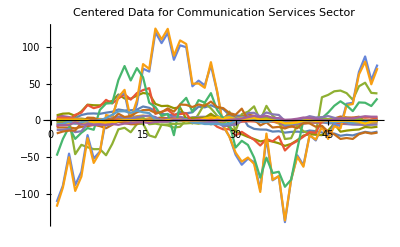

```mathematica
ListLinePlot[Transpose[centeredMatrix],PlotRange->All,PlotLabel->"Centered Data for Communication Services Sector",Background->White]
```

```mathematica
variances = StandardDeviation[centeredMatrix]^2
```

{196.085,14.656,622.201,5.88581,9.7903,26.8527,9.62758,7.11159,8.42724,439.303,409.126,4306.78,4526.76,0.97494,1474.38,2.19348,2.12772,9.24123,2.55149,38.1399,200.567,24.0433,3.39374,14.332}

```mathematica
pairs = Transpose[Join[{avg},{variances}]]
```

{{62.3989,196.085},{52.2564,14.656},{309.276,622.201},{35.7162,5.88581},{17.8889,9.7903},{109.891,26.8527},{27.6247,9.62758},{25.6372,7.11159},{32.5766,8.42724},{111.237,439.303},{165.873,409.126},{1118.2,4306.78},{1127.53,4526.76},{22.7391,0.97494},{336.835,1474.38},{13.9853,2.19348},{13.7166,2.12772},{73.2885,9.24123},{31.693,2.55149},{53.1785,38.1399},{112.245,200.567},{33.3287,24.0433},{29.6587,3.39374},{53.9611,14.332}}

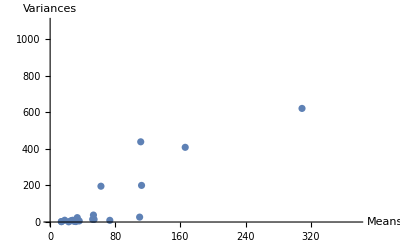

```mathematica
ListPlot[pairs,AxesLabel->{"Means", "Variances"},Background->White]
```

We can encode the above into the following procedure:

```mathematica
getCenteredStockData[matrix_]:=Module[{avg, dim, tempCenter,matrix2},avg = Mean[matrix];
dim = Length[avg];
tempCenter = {};
For[i = 1, i ≤ 53,i++,
tempCenter = Join[tempCenter,{avg}];
];
Return[matrix - tempCenter]
]
```

And now we get centered data for each sector:

```mathematica
communicationServicesBar = getCenteredStockData[newCommunicationServicesM];
consumerDiscretionaryBar = getCenteredStockData[newConsumerDiscretionaryM];
consumerStaplesBar=getCenteredStockData[newConsumerStaplesM];
energyBar=getCenteredStockData[newEnergyM];
financialsBar=getCenteredStockData[newFinancialsM];
healthCareBar=getCenteredStockData[newHealthCareM];
industrialsBar=getCenteredStockData[newIndustrialsM];
informationTechnologyBar=getCenteredStockData[newInformationTechnologyM];
materialsBar=getCenteredStockData[newMaterialsM];
realEstateBar=getCenteredStockData[newRealEstateM];
utilitiesBar=getCenteredStockData[newUtilitiesM];
```

We plot and inspect the centered data plots:

```mathematica
t = Map[Transpose,{communicationServicesBar,consumerDiscretionaryBar,consumerStaplesBar,energyBar,financialsBar,healthCareBar,industrialsBar,informationTechnologyBar,materialsBar,realEstateBar,utilitiesBar}];
allCenteredStockData = Join[t[[1]],t[[2]],t[[3]],t[[4]],t[[5]],t[[6]],t[[7]],t[[8]],t[[9]],t[[10]],t[[11]]];
```

Everything plotted together:

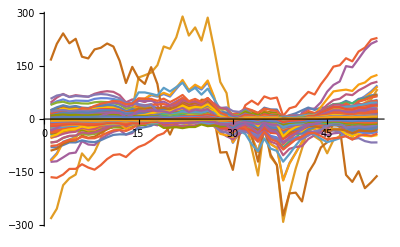

```mathematica
Show[Map[(ListLinePlot[t[[#]],PlotRange->All]&),{1,2,3,4,5,6,7,8,9,10,11}],PlotRange->All,Background-> White]
```

Plotting by sector:

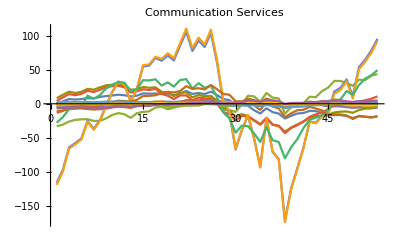

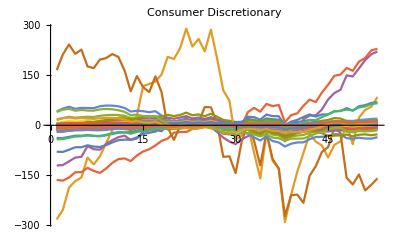

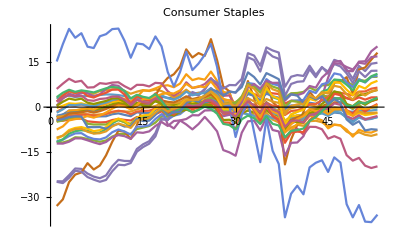

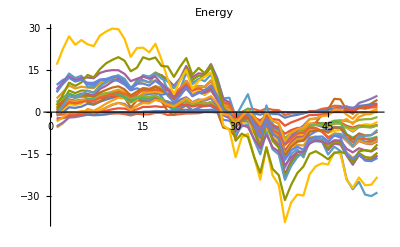

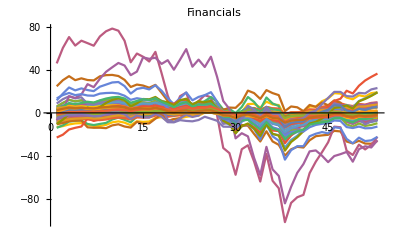

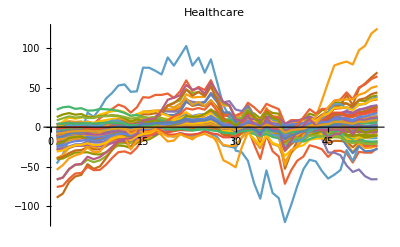

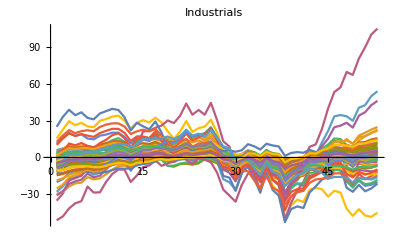

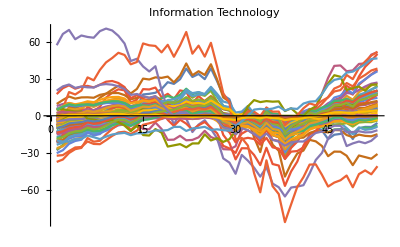

```mathematica
ListLinePlot[t[[1]],PlotLabel->sectorNames[[1]],PlotRange->All,Background-> White]
ListLinePlot[t[[2]],PlotLabel->sectorNames[[2]],PlotRange->All,Background-> White]
ListLinePlot[t[[3]],PlotLabel->sectorNames[[3]],PlotRange->All,Background-> White]
ListLinePlot[t[[4]],PlotLabel->sectorNames[[4]],PlotRange->All,Background-> White]
ListLinePlot[t[[5]],PlotLabel->sectorNames[[5]],PlotRange->All,Background-> White]
ListLinePlot[t[[6]],PlotLabel->sectorNames[[6]],PlotRange->All,Background-> White]
ListLinePlot[t[[7]],PlotLabel->sectorNames[[7]],PlotRange->All,Background-> White]
ListLinePlot[t[[8]],PlotLabel->sectorNames[[8]],PlotRange->All,Background-> White]
ListLinePlot[t[[9]],PlotLabel->sectorNames[[9]],PlotRange->All,Background-> White]
ListLinePlot[t[[10]],PlotLabel->sectorNames[[10]],PlotRange->All,Background-> White]
ListLinePlot[t[[11]],PlotLabel->sectorNames[[11]],PlotRange->All,Background-> White]
```

#### Producing PDF Points

We encapsulate the work from the example into the following method:

```mathematica
getPointsInPDFSpace[matrix_]:=Module[{avg, centeredMatrix,variances,pairs},
avg = Mean[matrix];
centeredMatrix = getCenteredStockData[matrix];
variances = StandardDeviation[centeredMatrix]^2;
pairs = Transpose[Join[{avg},{variances}]];
Return[pairs]
]
```

```mathematica
communicationServicesPairs = getPointsInPDFSpace[newCommunicationServicesM];
consumerDiscretionaryPairs = getPointsInPDFSpace[newConsumerDiscretionaryM];
consumerStaplesPairs=getPointsInPDFSpace[newConsumerStaplesM];
energyPairs=getPointsInPDFSpace[newEnergyM];
financialsPairs=getPointsInPDFSpace[newFinancialsM];
healthCarePairs=getPointsInPDFSpace[newHealthCareM];
industrialsPairs=getPointsInPDFSpace[newIndustrialsM];
informationTechnologyPairs=getPointsInPDFSpace[newInformationTechnologyM];
materialsPairs=getPointsInPDFSpace[newMaterialsM];
realEstatePairs=getPointsInPDFSpace[newRealEstateM];
utilitiesPairs=getPointsInPDFSpace[newUtilitiesM];
```

We also build a map from pdf points to stock name so that we can regroup stocks after clustering in PDF space. We don’t worry about collisions since it’s very unlikely that two stocks will be described by the same PDF point.:

```mathematica
buildAssociation[pairs_,stocks_]:=Module[{n,assoc},
n = Length[stocks];
assoc = Association[];
For[i = 1,i≤n,i++,
assoc = Append[assoc,pairs[[i]]-> stocks[[i]]];
];
Return[assoc]
]
```

```mathematica
communicationServicesMap= buildAssociation[communicationServicesPairs,communicationServices] (*previewed for example*)
consumerDiscretionaryMap = buildAssociation[consumerDiscretionaryPairs,consumerDiscretionary];
consumerStaplesMap=buildAssociation[consumerStaplesPairs,consumerStaples];
energyMap=buildAssociation[energyPairs,energy];
financialsMap=buildAssociation[financialsPairs,financials];
healthCareMap=buildAssociation[healthCarePairs,healthCare];
industrialsMap=buildAssociation[industrialsPairs,industrials];
informationTechnologyMap=buildAssociation[informationTechnologyPairs,informationTechnology];
materialsMap=buildAssociation[materialsPairs,materials];
realEstateMap=buildAssociation[realEstatePairs,realEstate];
utilitiesMap=buildAssociation[utilitiesPairs,utilities];
```

<|{62.3704,184.839}→ATVI,{52.2643,8.30913}→CBS,{309.349,384.582}→CHTR,{35.7161,5.06089}→CMCSA,{17.8837,9.04157}→CTL,{109.87,25.3002}→DIS,{27.6367,6.04164}→DISCA,{25.6471,4.46134}→DISCK,{32.5835,3.2507}→DISH,{111.192,417.681}→EA,{165.827,355.799}→FB,{1117.92,4416.7}→GOOG,{1127.25,4584.38}→GOOGL,{22.7376,0.559017}→IPG,{336.849,1082.6}→NFLX,{13.9827,2.05071}→NWS,{13.714,1.96878}→NWSA,{73.2595,6.3616}→OMC,{31.6818,1.90361}→T,{53.1922,8.55939}→TRIP,{112.197,190.123}→TTWO,{33.3172,5.80333}→TWTR,{29.6604,1.38644}→VIAB,{53.9436,14.2334}→VZ|>

```mathematica
globalMap = Join[communicationServicesMap,consumerDiscretionaryMap,consumerStaplesMap,energyMap,financialsMap,healthCareMap,industrialsMap,informationTechnologyMap,materialsMap,realEstateMap,utilitiesMap];
```

```mathematica
Length[globalMap]
```

497

Mathematica removes values if there is a collision. Since our starting length was  497, the above verifies there were no collisions between key values.

#### Plotting and Clustering in PDF Space

We plot all points in the (μ,σ) domain:

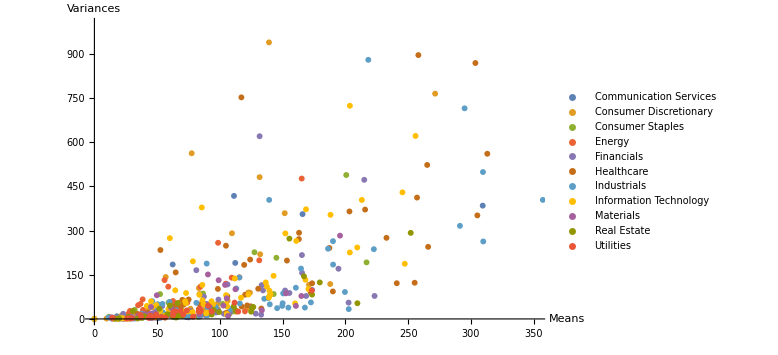

```mathematica
ListPlot[{communicationServicesPairs,consumerDiscretionaryPairs,consumerStaplesPairs,energyPairs,financialsPairs,healthCarePairs,industrialsPairs,informationTechnologyPairs,materialsPairs,realEstatePairs,utilitiesPairs},PlotLegends->{"Communication Services","Consumer Discretionary","Consumer Staples","Energy","Financials","Healthcare","Industrials","Information Technology","Materials","Real Estate","Utilities"},ImageSize->Large, PlotRange->{500,500},AxesLabel->{"Means", "Variances"},Background->White]
```

Plotting at full scale, we have:

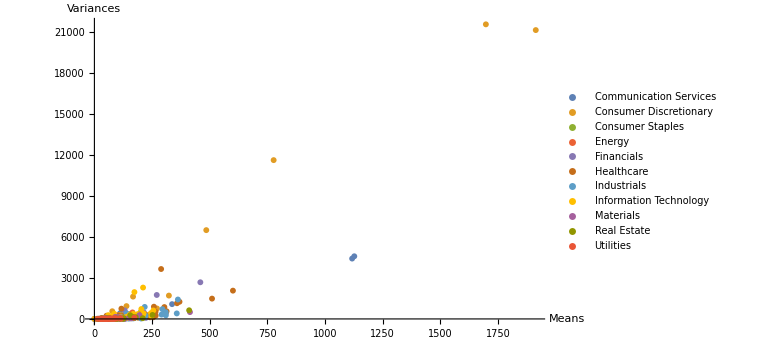

```mathematica
ListPlot[{communicationServicesPairs,consumerDiscretionaryPairs,consumerStaplesPairs,energyPairs,financialsPairs,healthCarePairs,industrialsPairs,informationTechnologyPairs,materialsPairs,realEstatePairs,utilitiesPairs},PlotLegends->{"Communication Services","Consumer Discretionary","Consumer Staples","Energy","Financials","Healthcare","Industrials","Information Technology","Materials","Real Estate","Utilities"},ImageSize->Large, PlotRange->All,AxesLabel->{"Means", "Variances"},Background->White]
```

Based on visual inspection, we see that the data points don’t generally seem to be clustering by sectors, but rather follow a general parabolic curve in the (μ,σ) plane. We use Mathematica’s native FindClusters function to cluster all of the points joined together.

```mathematica
allPoints = Join[communicationServicesPairs,consumerDiscretionaryPairs,consumerStaplesPairs,energyPairs,financialsPairs,healthCarePairs,industrialsPairs,informationTechnologyPairs,materialsPairs,realEstatePairs,utilitiesPairs];
```

```mathematica
clustersPDFSpace = FindClusters[allPoints];
Length[clustersPDFSpace ]
```

2

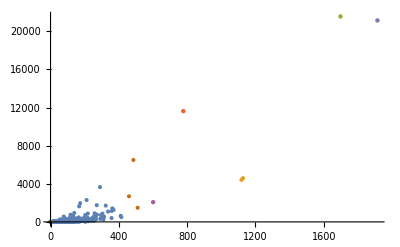

```mathematica
ListPlot[clustersPDFSpace ,PlotRange->All,Background->White]
```

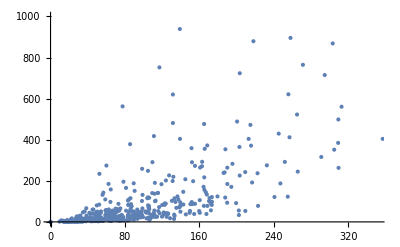

```mathematica
ListPlot[clustersPDFSpace ,Background->White,PlotRange->{500,500}]
```

Using the Association defined earlier, we can pull clusters by stock name from the PDF clusters.

```mathematica
clusterNames[clusters_]:=Module[{n,clusterNames, aCluster, aClusterLength},
clusterNames = {};
n = Length[clusters];
For[i = 1, i≤n,i++,
aCluster = {};
aClusterLength = Length[clusters[[i]]];
For[j = 1, j ≤ aClusterLength, j++,
AppendTo[aCluster,globalMap[clusters[[i]][[j]]]];
];
AppendTo[clusterNames,aCluster]
];
Return[clusterNames]
]
```

```mathematica
stockClustersPDFSpace  = clusterNames[clustersPDFSpace ]
```

{{ATVI,CBS,CHTR,CMCSA,CTL,DIS,DISCA,DISCK,DISH,EA,FB,IPG,NFLX,NWS,NWSA,OMC,T,TRIP,TTWO,TWTR,VIAB,VZ,AAP,APTV,BBY,BWA,CCL,CPRI,DG,DHI,DLTR,DRI,EBAY,EXPE,F,FL,GM,GPC,GPS,GRMN,HAS,HBI,HD,HLT,HOG,HRB,JWN,KMX,KSS,LB,LEG,LEN,LKQ,LOW,M,MAR,MAT,MCD,MGM,MHK,NCLH,NKE,NWL,ORLY,PHM,PVH,RCL,RL,ROST,SBUX,TGT,TIF,TJX,TPR,TSCO,UA,UAA,ULTA,VFC,WHR,WYNN,YUM,ADM,CAG,CHD,CL,CLX,COST,COTY,CPB,EL,GIS,HRL,HSY,K,KHC,KMB,KO,KR,LW,MDLZ,MKC,MNST,MO,PEP,PG,PM,SJM,STZ,SYY,TAP,TSN,WBA,WMT,APA,APC,BHGE,COG,COP,CVX,CXO,DVN,EOG,FANG,FTI,HAL,HES,HFC,HP,KMI,MPC,NBL,NOV,OKE,OXY,PSX,PXD,SLB,VLO,WMB,XEC,XOM,AFL,AIG,AIZ,AJG,ALL,AMG,AMP,AON,AXP,BAC,BBT,BEN,BK,BRK.B,C,CB,CFG,CINF,CMA,CME,COF,DFS,ETFC,FITB,FRC,GS,HBAN,HIG,ICE,IVZ,JEF,JPM,KEY,L,LNC,MCO,MET,MMC,MS,MSCI,MTB,NDAQ,NTRS,PBCT,PFG,PGR,PNC,PRU,RE,RF,RJF,SCHW,SIVB,SPGI,STI,STT,SYF,TMK,TROW,TRV,UNM,USB,WFC,WLTW,ZION,A,ABBV,ABC,ABMD,ABT,AGN,ALGN,ALXN,AMGN,ANTM,BAX,BDX,BIIB,BMY,BSX,CAH,CELG,CERN,CI,CNC,COO,CVS,DGX,DHR,DVA,EW,GILD,HCA,HOLX,HSIC,HUM,IDXX,ILMN,INCY,IQV,JNJ,LH,LLY,MCK,MDT,MRK,MYL,NKTR,PFE,PKI,PRGO,REGN,RMD,SYK,TFX,TMO,UHS,UNH,VAR,VRTX,WAT,WCG,XRAY,ZBH,ZTS,AAL,ALK,ALLE,AME,AOS,ARNC,BA,CAT,CHRW,CMI,CPRT,CSX,CTAS,DAL,DE,DOV,EFX,EMR,ETN,EXPD,FAST,FBHS,FDX,FLR,FLS,FTV,GD,GE,GWW,HII,HON,HRS,INFO,IR,ITW,JBHT,JCI,JEC,KSU,LLL,LMT,LUV,MAS,MMM,NLSN,NOC,NSC,PCAR,PH,PWR,RHI,ROK,ROL,ROP,RSG,RTN,SNA,SWK,TDG,TXT,UAL,UNP,UPS,URI,UTX,VRSK,WAB,WM,XYL,AAPL,ACN,ADBE,ADI,ADP,ADS,ADSK,AKAM,AMAT,AMD,ANET,ANSS,APH,AVGO,BR,CDNS,CRM,CSCO,CTSH,CTXS,DXC,FFIV,FIS,FISV,FLIR,FLT,FTNT,GLW,GPN,HPE,HPQ,IBM,INTC,INTU,IPGP,IT,JKHY,JNPR,KEYS,KLAC,LRCX,MA,MCHP,MSFT,MSI,MU,MXIM,NTAP,NVDA,ORCL,PAYX,PYPL,QCOM,QRVO,RHT,SNPS,STX,SWKS,SYMC,TEL,TSS,TXN,V,VRSN,WDC,WU,XLNX,XRX,ALB,APD,AVY,BLL,CE,CF,DWDP,ECL,EMN,FCX,FMC,IFF,IP,LIN,LYB,MLM,MOS,NEM,NUE,PKG,PPG,SEE,SHW,VMC,WRK,AIV,AMT,ARE,AVB,BXP,CCI,DLR,DRE,EQR,ESS,EXR,FRT,HCP,HST,IRM,KIM,MAA,MAC,O,PLD,PSA,REG,SBAC,SLG,SPG,UDR,VNO,VTR,WELL,WY,AEE,AEP,AES,ATO,AWK,CMS,CNP,D,DTE,DUK,ED,EIX,ES,ETR,EVRG,EXC,FE,LNT,NEE,NI,NRG,PEG,PNW,PPL,SO,SRE,WEC,XEL},{GOOG,GOOGL,AMZN,AZO,BKNG,CMG,BLK,ISRG,MTD,EQIX}}

We also define some functions for plotting stocks within a cluster:

```mathematica
plotCenteredDataFromCluster[stockCluster_]:=Module[{listOfListPlots,index,n},
listOfListPlots = {};
n = Length[stockCluster];
For[i = 1, i≤ n, i++,
index = Position[sp500symbols,stockCluster[[i]]][[1]][[1]];
AppendTo[listOfListPlots,ListLinePlot[allCenteredStockData[[index]],PlotRange->All]]
];
Return[listOfListPlots]
]
plotOriginalDataFromCluster[stockCluster_]:=Module[{listOfListPlots,index,n},
listOfListPlots = {};
n = Length[stockCluster];
For[i = 1, i≤ n, i++,
index = Position[sp500symbols,stockCluster[[i]]][[1]][[1]];
AppendTo[listOfListPlots,ListLinePlot[svdOriginalDataReconstruction[[index]],PlotRange->All]]
];
Return[listOfListPlots]
]
```

We now plot all stocks within the returned clusters.

```mathematica
ol1 = plotOriginalDataFromCluster[stockClustersPDFSpace [[1]]];
l1 = plotCenteredDataFromCluster[stockClustersPDFSpace [[1]]];
```

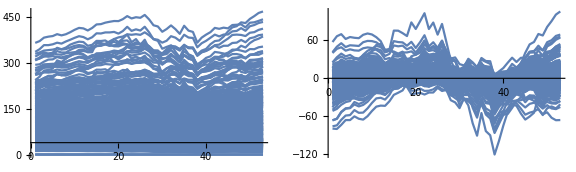

```mathematica
GraphicsRow[{Show[ol1,PlotRange-> All],Show[l1, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
```

```mathematica
ol2 = plotOriginalDataFromCluster[stockClustersPDFSpace [[2]]];
l2 = plotCenteredDataFromCluster[stockClustersPDFSpace [[2]]];
```

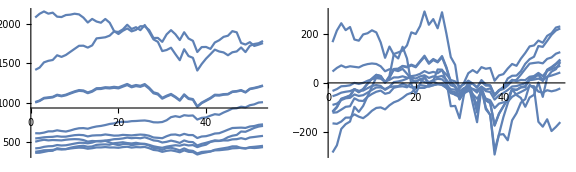

```mathematica
GraphicsRow[{Show[ol2,PlotRange-> All],Show[l2, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
```

We observe that the clustering has essentially clustered by mean. We now see how a change of basis impacts clustering. Before moving on, it should be noted that we can tell Mathematica how many clusters to produce. On its own it produced two clusters; for three or more clusters, only the points far out in the plot were further partitioned, not giving us any more meaningful categorization.

#### Change of Basis and Clustering Along Principal Components

Mathematica has a built in function to allow for what we want:

```mathematica
dr = DimensionReduction[allPoints,Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
adjustedPoints = dr[allPoints];
```

```mathematica
pcaClusters = FindClusters[adjustedPoints];
Length[pcaClusters]
```

2

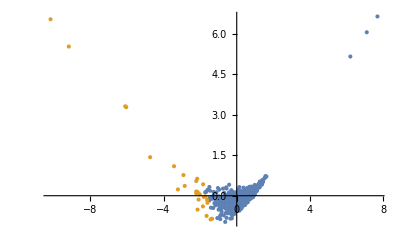

```mathematica
ListPlot[pcaClusters,PlotRange->All,Background-> White]
```

The indices of “adjustedPoints” and “allPoints” correspond - we use this and the Association map between “allPoints” and the S&P500 stock names to plot the new clusters:

```mathematica
clusterNamesFromPCA[clusters_]:=Module[{clusterNames,n,aCluster,aClusterLength,index,pdf},
clusterNames = {};
n = Length[clusters];
For[i = 1, i≤n,i++,
aCluster = {};
aClusterLength = Length[clusters[[i]]];
For[j = 1, j ≤ aClusterLength, j++,
index = Position[adjustedPoints,clusters[[i]][[j]]][[1]][[1]];
pdf = allPoints[[index]];
AppendTo[aCluster,globalMap[pdf]];
];
AppendTo[clusterNames,aCluster]
];
Return[clusterNames]
]
```

```mathematica
clustersFromPCA = clusterNamesFromPCA[pcaClusters]
```

{{ATVI,CBS,CHTR,CMCSA,CTL,DIS,DISCA,DISCK,DISH,EA,FB,IPG,NWS,NWSA,OMC,T,TRIP,TTWO,TWTR,VIAB,VZ,AAP,APTV,BBY,BWA,CCL,CPRI,DG,DHI,DLTR,DRI,EBAY,EXPE,F,FL,GM,GPC,GPS,GRMN,HAS,HBI,HD,HLT,HOG,HRB,JWN,KMX,KSS,LB,LEG,LEN,LKQ,LOW,M,MAR,MAT,MCD,MGM,NCLH,NKE,NWL,PHM,PVH,RCL,RL,ROST,SBUX,TGT,TIF,TJX,TPR,TSCO,UA,UAA,VFC,WHR,WYNN,YUM,ADM,CAG,CHD,CL,CLX,COST,COTY,CPB,EL,GIS,HRL,HSY,K,KHC,KMB,KO,KR,LW,MDLZ,MKC,MNST,MO,PEP,PG,PM,SJM,STZ,SYY,TAP,TSN,WBA,WMT,APA,APC,BHGE,COG,COP,CVX,CXO,DVN,EOG,FANG,FTI,HAL,HES,HFC,HP,KMI,MPC,NBL,NOV,OKE,OXY,PSX,PXD,SLB,VLO,WMB,XEC,XOM,AFL,AIG,AIZ,AJG,ALL,AMG,AMP,AON,AXP,BAC,BBT,BEN,BK,BRK.B,C,CB,CFG,CINF,CMA,CME,COF,DFS,ETFC,FITB,FRC,GS,HBAN,HIG,ICE,IVZ,JEF,JPM,KEY,L,LNC,MCO,MET,MMC,MS,MSCI,MTB,NDAQ,NTRS,PBCT,PFG,PGR,PNC,PRU,RE,RF,RJF,SCHW,SPGI,STI,STT,SYF,TMK,TROW,TRV,UNM,USB,WFC,WLTW,ZION,A,ABBV,ABC,ABT,AGN,ALXN,AMGN,ANTM,BAX,BDX,BIIB,BMY,BSX,CAH,CELG,CERN,CI,CNC,COO,CVS,DGX,DHR,DVA,EW,GILD,HCA,HOLX,HSIC,HUM,IDXX,INCY,IQV,JNJ,LH,LLY,MCK,MDT,MRK,MYL,NKTR,PFE,PKI,PRGO,RMD,SYK,TFX,TMO,UHS,UNH,VAR,VRTX,WAT,XRAY,ZBH,ZTS,AAL,ALK,ALLE,AME,AOS,ARNC,CAT,CHRW,CMI,CPRT,CSX,CTAS,DAL,DE,DOV,EFX,EMR,ETN,EXPD,FAST,FBHS,FDX,FLR,FLS,FTV,GD,GE,GWW,HII,HON,HRS,INFO,IR,ITW,JBHT,JCI,JEC,KSU,LLL,LMT,LUV,MAS,MMM,NLSN,NSC,PCAR,PH,PWR,RHI,ROK,ROL,ROP,RSG,RTN,SNA,SWK,TXT,UAL,UNP,UPS,URI,UTX,VRSK,WAB,WM,XYL,AAPL,ACN,ADBE,ADI,ADP,ADS,ADSK,AKAM,AMAT,AMD,ANET,ANSS,APH,AVGO,BR,CDNS,CRM,CSCO,CTSH,CTXS,DXC,FFIV,FIS,FISV,FLIR,FLT,FTNT,GLW,GPN,HPE,HPQ,IBM,INTC,INTU,IT,JKHY,JNPR,KEYS,KLAC,LRCX,MA,MCHP,MSFT,MSI,MU,MXIM,NTAP,ORCL,PAYX,PYPL,QCOM,QRVO,RHT,SNPS,STX,SWKS,SYMC,TEL,TSS,TXN,V,VRSN,WDC,WU,XLNX,XRX,ALB,APD,AVY,BLL,CE,CF,DWDP,ECL,EMN,FCX,FMC,IFF,IP,LIN,LYB,MLM,MOS,NEM,NUE,PKG,PPG,SEE,VMC,WRK,AIV,AMT,ARE,AVB,BXP,CCI,DLR,DRE,EQR,ESS,EXR,FRT,HCP,HST,IRM,KIM,MAA,MAC,O,PLD,PSA,REG,SBAC,SLG,SPG,UDR,VNO,VTR,WELL,WY,AEE,AEP,AES,ATO,AWK,CMS,CNP,D,DTE,DUK,ED,EIX,ES,ETR,EVRG,EXC,FE,LNT,NEE,NI,NRG,PEG,PNW,PPL,SO,SRE,WEC,XEL},{GOOG,GOOGL,NFLX,AMZN,AZO,BKNG,CMG,MHK,ORLY,ULTA,BLK,SIVB,ABMD,ALGN,ILMN,ISRG,MTD,REGN,WCG,BA,NOC,TDG,IPGP,NVDA,SHW,EQIX}}

```mathematica
l1 = plotCenteredDataFromCluster[clustersFromPCA[[1]]];
l2 = plotCenteredDataFromCluster[clustersFromPCA[[2]]];
ol1 = plotOriginalDataFromCluster[clustersFromPCA[[1]]];
ol2 = plotOriginalDataFromCluster[clustersFromPCA[[2]]];
```

First cluster:

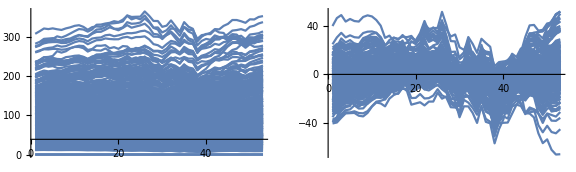

```mathematica
GraphicsRow[{Show[ol1,PlotRange-> All],Show[l1, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
```

Second cluster:

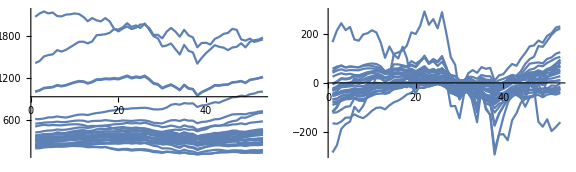

```mathematica
GraphicsRow[{Show[ol2,PlotRange-> All],Show[l2, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
```

This does a better job clustering on the means - we see better stratification in stock data. In both of our clustering operations, there was the main clustering group and a smaller one - we see if there is much overlap between the smaller clusters from the (μ,σ)-plane clustering and the PCA-component-plane clustering.

```mathematica
PDFSpaceSmallCluster = stockClustersPDFSpace[[2]]
```

{GOOG,GOOGL,AMZN,AZO,BKNG,CMG,BLK,ISRG,MTD,EQIX}

```mathematica
PCASpaceSmallCluster =  clustersFromPCA[[2]]
```

{GOOG,GOOGL,NFLX,AMZN,AZO,BKNG,CMG,MHK,ORLY,ULTA,BLK,SIVB,ABMD,ALGN,ILMN,ISRG,MTD,REGN,WCG,BA,NOC,TDG,IPGP,NVDA,SHW,EQIX}

```mathematica
Intersection[PDFSpaceSmallCluster,PCASpaceSmallCluster]
```

{AMZN,AZO,BKNG,BLK,CMG,EQIX,GOOG,GOOGL,ISRG,MTD}

We observe that the PDF Space Smaller Cluster is a subset of the PCA Space Smaller Cluster, which isn’t surprising given that we are essentially clustering by means. We briefly investigate the case where we force three partitions of the data:

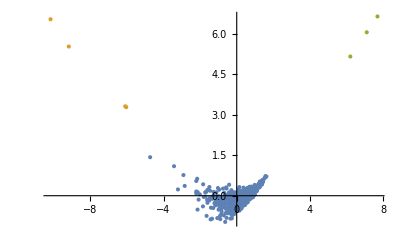

{{ATVI,CBS,CHTR,CMCSA,CTL,DIS,DISCA,DISCK,DISH,EA,FB,IPG,NFLX,NWS,NWSA,OMC,T,TRIP,TTWO,TWTR,VIAB,VZ,AAP,APTV,AZO,BBY,BWA,CCL,CMG,CPRI,DG,DHI,DLTR,DRI,EBAY,EXPE,F,FL,GM,GPC,GPS,GRMN,HAS,HBI,HD,HLT,HOG,HRB,JWN,KMX,KSS,LB,LEG,LEN,LKQ,LOW,M,MAR,MAT,MCD,MGM,MHK,NCLH,NKE,NWL,ORLY,PHM,PVH,RCL,RL,ROST,SBUX,TGT,TIF,TJX,TPR,TSCO,UA,UAA,ULTA,VFC,WHR,WYNN,YUM,ADM,CAG,CHD,CL,CLX,COST,COTY,CPB,EL,GIS,HRL,HSY,K,KHC,KMB,KO,KR,LW,MDLZ,MKC,MNST,MO,PEP,PG,PM,SJM,STZ,SYY,TAP,TSN,WBA,WMT,APA,APC,BHGE,COG,CVX,CXO,DVN,EOG,FANG,FTI,HAL,HES,HFC,HP,KMI,MPC,NBL,NOV,OKE,OXY,PSX,PXD,SLB,VLO,WMB,XEC,XOM,AFL,AIG,AIZ,AJG,AMG,AMP,AON,AXP,BAC,BBT,BEN,BK,BLK,BRK.B,C,CB,CFG,CINF,CMA,CME,COF,DFS,ETFC,FITB,FRC,GS,HBAN,HIG,ICE,IVZ,JEF,JPM,KEY,L,LNC,MCO,MET,MMC,MS,MSCI,MTB,NDAQ,NTRS,PBCT,PFG,PGR,PNC,PRU,RE,RF,RJF,SCHW,SIVB,SPGI,STI,STT,SYF,TMK,TROW,TRV,UNM,USB,WFC,WLTW,ZION,A,ABBV,ABC,ABMD,ABT,AGN,ALGN,ALXN,AMGN,ANTM,BAX,BDX,BIIB,BMY,BSX,CAH,CELG,CERN,CI,CNC,COO,CVS,DGX,DHR,DVA,EW,GILD,HCA,HOLX,HSIC,HUM,IDXX,ILMN,INCY,IQV,ISRG,JNJ,LH,LLY,MCK,MDT,MRK,MTD,MYL,NKTR,PFE,PKI,PRGO,REGN,RMD,SYK,TFX,TMO,UHS,UNH,VAR,VRTX,WAT,WCG,XRAY,ZBH,ZTS,AAL,ALK,ALLE,AME,AOS,ARNC,BA,CAT,CHRW,CMI,CPRT,CSX,CTAS,DAL,DE,DOV,EFX,EMR,ETN,EXPD,FAST,FBHS,FDX,FLR,FLS,FTV,GD,GE,GWW,HII,HON,HRS,INFO,IR,ITW,JBHT,JCI,JEC,KSU,LLL,LMT,LUV,MAS,MMM,NLSN,NOC,NSC,PCAR,PH,PWR,RHI,ROK,ROL,ROP,RSG,RTN,SNA,SWK,TDG,TXT,UAL,UNP,UPS,URI,UTX,VRSK,WAB,WM,XYL,AAPL,ACN,ADBE,ADI,ADP,ADS,ADSK,AKAM,AMAT,ANET,ANSS,APH,AVGO,BR,CDNS,CRM,CSCO,CTSH,CTXS,DXC,FFIV,FIS,FISV,FLIR,FLT,FTNT,GLW,GPN,HPE,HPQ,IBM,INTC,INTU,IPGP,IT,JKHY,JNPR,KEYS,KLAC,LRCX,MA,MCHP,MSFT,MSI,MU,MXIM,NTAP,NVDA,ORCL,PAYX,PYPL,QCOM,QRVO,RHT,SNPS,STX,SWKS,SYMC,TEL,TSS,TXN,V,VRSN,WDC,WU,XLNX,XRX,ALB,APD,AVY,BLL,CE,CF,DWDP,ECL,EMN,FCX,FMC,IFF,IP,LIN,LYB,MLM,MOS,NEM,NUE,PKG,PPG,SEE,SHW,VMC,WRK,AIV,AMT,ARE,AVB,BXP,CCI,DLR,DRE,EQIX,EQR,ESS,EXR,FRT,HCP,HST,IRM,KIM,MAA,MAC,O,PLD,PSA,REG,SBAC,SLG,SPG,UDR,VNO,VTR,WELL,WY,AEE,AEP,AES,ATO,AWK,CMS,CNP,D,DTE,DUK,ED,EIX,ES,ETR,EVRG,EXC,FE,LNT,NEE,NI,NRG,PEG,PNW,PPL,SO,SRE,WEC,XEL},{GOOG,GOOGL,AMZN,BKNG},{COP,ALL,AMD}}

```mathematica
pcaClusters2 = FindClusters[adjustedPoints,3];
ListPlot[pcaClusters2,PlotRange->All,Background-> White]
clustersFromPCA2 = clusterNamesFromPCA[pcaClusters2]
l1 = plotCenteredDataFromCluster[clustersFromPCA2[[1]]];
l2 = plotCenteredDataFromCluster[clustersFromPCA2[[2]]];
l3 = plotCenteredDataFromCluster[clustersFromPCA2[[3]]];
ol1 = plotOriginalDataFromCluster[clustersFromPCA2[[1]]];
ol2 = plotOriginalDataFromCluster[clustersFromPCA2[[2]]];
ol3 = plotOriginalDataFromCluster[clustersFromPCA2[[3]]];
```

```mathematica
GraphicsRow[{Show[ol1,PlotRange-> All],Show[l1, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol2,PlotRange-> All],Show[l2, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol3,PlotRange-> All],Show[l3, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
```

-Graphics-

-Graphics-

-Graphics-

#### Clustering by Information Entropy from PDF Space

We now try a different approach. We recall the following functional definitions from the Information Theory Module:

```mathematica
pdf[x_] := Evaluate[PDF[NormalDistribution[μ,σ],x]](* A PDF defined by a datapoint in (μ,σ) space*)
Info[x_]:= -Log[pdf[x]] (*Information*)
S := Integrate[Info[x]pdf[x],{x,-Infinity,Infinity}](*Entropy*)
```

And we define a function that takes in a PDF point and returns the entropy of that probability distribution. We use NIntegrate and change the bounds to integrate within 5 standard deviations of the mean to make the integration easier.

```mathematica
computeEntropy[p_]:=Module[{μ,σ, pdf, Info, S},
μ=p[[1]];
σ = p[[2]];
pdf[x_] := Max[Evaluate[PDF[NormalDistribution[μ,σ],x]],10^-4];(*we put this here to prevent Log and the Integral from blowing up for very small PDF values*)
Info[x_]:= -Log[pdf[x]];
S = NIntegrate[Info[x]pdf[x],{x,μ - 5Sqrt[σ],μ + 5Sqrt[σ]},AccuracyGoal->3,PrecisionGoal->3,Method->"MonteCarlo"](*Crude Monte Carlo to allow the integrals to converge quickly*)
]
```

```mathematica
entropies = Map[computeEntropy,allPoints];
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 3.0943 and 0.00397816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 2.88156 and 0.00551944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 3.10548 and 0.00373122 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

We store entropies explicitly in this cell.

```mathematica
entropies = {1.7705953159853285,3.094298041210131,1.3845926488683806,2.881559106723794,3.105483194314945,2.9182184716133404,2.9866125590934005,2.802873465171298,2.5555737305177604,1.3456331885218464,1.4235220687662493,0.6121033238907354,0.6236142664909966,0.836584563374532,0.9553390621935506,2.120220395529013,2.0890716283413324,2.9977203223025084,2.0648968270176886,3.101360858146278,1.747738458169008,2.9645937951028944,1.753771776991981,3.1097724106416997,1.4193247861762588,1.3522955620312311,2.105338942651225,0.9928665236380894,2.4979993962216205,1.3390541967755647,2.9521293441096685,3.119478016505505,0.7424471895450371,1.9202286416171286,2.426097595117758,3.11432051766437,2.7672782578326447,2.3222855920717778,3.104019884847511,2.7424217162004147,1.7316856520246555,3.0326088041292913,2.842164728724344,2.769912372644863,2.816161452086653,2.50119409768774,2.6974670270398486,2.73734754729837,2.027454041405005,2.959424870408961,3.1140906714910357,1.4757016359750765,2.766642086078441,2.7272517672852925,2.9227058010414892,3.1143676718679414,3.06827641211614,2.945015441996532,3.115766441880635,2.54299264882836,2.9988746071300096,2.201306608650437,2.195194607324931,2.042317416691416,2.9798570639567683,0.8192539255598565,3.0212732990544753,2.882029777310749,3.120130112153912,0.8053301503603959,2.7535432981976506,1.2801699080484148,2.9294540814196623,2.195105189204559,2.808706183768136,2.6084351638631555,2.762488192399515,1.5241701997525479,1.2117306278718407,2.6801528040994924,2.23359080282939,0.945278388734576,1.0591250722010885,1.0859212091048613,2.8590220483287876,1.6740550109579968,1.0065867656257894,2.8019804926272567,3.090072938743468,2.8280094167254566,2.486669544171055,2.8058373195013555,1.7030956028790816,1.7458226368638183,3.0639487113173067,2.464368078126825,2.2332173730739737,2.9792894448372076,3.120237363442492,2.543846625052238,2.7368149063189953,2.2334983575720244,2.766544808493493,2.79567503386765,2.678834224433394,3.089481695555794,3.0382435594755446,1.6554911005939303,2.891350663774291,3.118327632478973,2.8923912683119393,2.2195214132958108,3.0459870796065487,3.053956910892058,1.2752327343756245,3.0899196437820082,3.0442700477323585,3.0067137798767316,2.8227912989530815,2.868241023762541,2.8274189592471304,2.074451837489177,2.9854948210511196,1.3658579325930258,1.6142148726186822*^-7,2.910539125026811,1.7269909392449085,2.5985610805185413,1.9302472593458824,1.9222778407755363,3.0294722931733378,2.3748005737730002,2.758572596179708,2.436937865189185,2.8587581145095897,1.791681340114317,2.4209276841799583,2.889275480168192,2.5452926162812495,3.07118554884063,2.49281298691889,2.0212261424343376,1.2869436111805967,1.962858644209926,1.5851545122828565,2.6498666939189155,2.0717069894877027,3.1237137867225693,2.6944745698524,2.752339229950603,2.854649328296304,3.0662013203639953,2.2362175069965614*^-6,1.171454967787282,2.0447251369259827,2.1518543367765823,3.051526584852228,2.2728204852867084,2.9540514599177556,1.9972580399363837,3.065847010675107,0.6779378623780593,2.495936027201641,3.0045634760417204,3.0898554843693296,3.119212116680336,2.9003420152105366,2.301983449833403,2.139105997629006,2.5428546797958465,3.049241845473927,2.635745699179974,2.9386720576175396,2.97877600612656,1.2892609469528236,1.459340217336341,3.1137906744500445,2.9250874002692884,3.065668124040364,2.613591287145037,2.9643773365929404,2.613788637696659,2.6790088350182284,3.0266640003234655,1.8654773133142177,2.5896176843196272,3.091395739970578,3.0351502814370637,1.6770911004711366,2.284778321863617,3.1130941956084723,2.395864545390892,1.865690724968367,3.021183529333269,3.101455585071836,2.153967312289749,2.914167889410278,2.282799145713463,2.529378852412579,2.47064475942706,2.9671682294560484,0.7973899991791885,1.8158421732038403,2.884106367915699,1.8307518207363709,3.1235148577904526,3.0939600741029585,2.0344694784341173,3.0531121955191693,3.1120060371803544,2.444431743066659,3.1162283459896303,2.209980806418098,3.071913001814308,2.8974271267519476,2.6456644892800742,3.104198248727014,0.9345685379940316,2.770389640275296,1.520308294296416,0.6015589324195822,2.607604196803328,2.173102282809062,1.2452888782280591,3.0142393271888688,2.0163815785204964,1.2134283427176562,3.1049213011721757,3.113942878674344,3.057776508082122,2.779157084653712,3.0928727840028407,1.623011387289622,1.091628830224997,1.3516298657749788,2.6799739792204793,2.1203997065900935,2.2923918031299766,2.6235334617262622,1.7296698235989387,3.0886471363732544,1.7206060638790344,3.0994271349267493,2.3858381841649297,1.4302291251113406,1.4014380088698202,1.0355845264930712,2.5777334389723277,1.7692616607463383,0.8489926999759025,2.7539941229824207,1.562010398998177,1.6035787851641783,2.113528177105923,2.997878058980666,2.3990655406097194,0.7486860446906195,3.0523761742453623,1.6369763610633936,3.1167395825198994,2.57030330356996,1.8579125716572051,0.9034810695911782,2.9853582854591645,2.1873634644403412,1.6160935820869406,1.5516078980223755,2.645757734970995,2.0090785589548332,2.2538188879025993,2.011393084817715,1.410913087544393,1.0245476193232677,2.97060252813814,2.6563508599891508,3.067806815617681,3.048828647557542,3.094726410164432,3.100908205405274,3.125020800458851,2.541919398907485,1.6311125015755963,1.3597420058985736,2.342806798550527,3.116333507903331,2.7320211807577053,2.9757854927776366,2.984661606483985,1.7696670510997978,2.842405702330187,2.622005752264387,3.114521904650727,1.9269523661942447,3.0414887234383086,3.0718126364683966,3.1149116124945757,3.089695302915205,2.7039311332293154,1.0313361362690627,2.4426973891498514,3.107168482870335,3.0195213831098235,1.6277075485213708,2.9023141279756257,1.2649468149344822,1.6303414903437932,2.519205481977612,2.712657782101987,2.8123952475616356,2.6765717779128497,2.562848734921069,2.110367518780531,2.5961735401870616,2.936500763529323,2.7894444082607213,2.185165225584213,1.576208946631363,3.114130329354688,3.12363692237019,2.7848031896253014,2.9380867329568643,1.111635642759267,1.8141317070787195,3.112022086629278,2.708151862245385,2.447300973595277,2.8480854978580528,2.4850825779106005,2.5567114090295626,1.4787969170215503,3.0613808683421255,1.5731521651506006,2.0970362339444093,2.3666601849298834,0.863137133879965,2.469838869308804,2.5011350433183903,2.218159694781237,2.7304717238838716,1.3617864044293528,2.7015174728529425,2.523340692030749,1.7578927001548361,2.6903125366327925,3.110803595462192,1.4264251275743711,2.5169764581077554,1.7577036326934559,2.565647248222077,2.1572561176138194,1.1075573737029207,2.2408270888769843,2.964091839234407,2.6288849566800643,4.555191411916772*^-7,1.1696167620236764,1.9574684335748476,3.0295030202657816,1.3333013574070538,1.9391249139053715,2.683376812932165,1.901800425233119,3.0866866907330412,2.9255072706578473,3.0820904012564263,1.7358872447030944,2.121752499820804,3.062978693991936,2.956596262093539,2.895649744672879,1.616568089596018,2.2121783756864883,2.9232012595172794,2.3330413681153854,0.7870169622536826,2.213601259044028,2.0731229121432992,3.1056985293853727,1.363088474576063,0.7639544985960441,2.2771318581700015,1.999846764906472,1.6692996112355754,2.1493881905435868,2.2621398293690254,1.4018309416477088,1.656841914136437,2.251993819687319,2.6521720081794773,2.2468787947008093,2.444232114891147,3.1250999213681188,2.445810353249794,0.7197285070957122,2.9506074955495905,2.930162353780429,2.556407583639919,2.785795181766444,2.514390120399418,1.5722209538366092,2.445308904296658,2.590014633061639,2.0431544798119003,2.4284737763084157,2.41533896849128,2.990506097680321,2.556720560054624,2.3285218588268775,1.5245273160319672,1.5538041572208345,1.3528464834883283,1.3924169441242478,2.645989067673751,2.68645595534317,2.286992572350587,2.6136909192624507,2.677804981771642,2.346689224928102,3.050410831050326,2.7231911687534334,2.221961128969421,1.8828625597847926,2.9387784530883985,3.0828103348060756,2.84987591590545,3.0455435919478795,2.6291827572569084,1.9632744209176929,1.5393660572531342,2.892879026300411,3.1162317583851897,3.1199441508704377,2.041175752435364,3.1152689690769155,3.075955409165973,1.2632205496718452,2.124750851356555,2.2630977192101707,3.1242153853968007,1.5565938954669525,2.6733858521532885,2.0020406876202683,2.9329381278315907,2.6475537801413807,2.842076082421054,1.7564934225604,1.1621483285236633,3.0517182064985713,1.5207332889830234,3.0883089026857373,2.731355654311021,3.0486215431174313,2.075404082075662,1.7452766641010171,1.5143120272100647,2.9536780430754046,2.7614324861685096,2.610949652903306,3.0615330102861753,2.518829450186228,3.07441383015573,1.9054431499868596,2.821688556298121,2.2482156970559584,3.105997510740505,3.116810953177419,3.0779118129401972,2.5042592459322646,2.8930713258331835,2.897265918349346,2.859729674081309,2.5989774513394295,2.9146149602642124,2.6081059977660273,3.1193626955463234,2.3093037188429615,3.096539887676634,2.498072210243949,2.921975924460575,3.0499400219549595,3.1150019447339368,2.94349806553751,2.9044340278934944,2.813099394101994,3.1179627676091486,2.934380239609921,2.603182847352754,2.15210430714524,1.7418095872634605,3.092525902257178,3.0265913306798264,2.772758892972111,2.2345542549131983,2.9262940785322766,2.919781715279809,2.8844314052399995,3.1071713379938206};
```

We now cluster. Some trial and error influenced our decision in how many clusters to take:

```mathematica
entropyClusters = FindClusters[entropies,10];
Length[entropyClusters]
```

10

We now transfer these clusters to the stock names.

```mathematica
clusterNamesFromEntropies[clusters_]:=Module[{clusterNames,n,aCluster,aClusterLength,index,pdf},
clusterNames = {};
n = Length[clusters];
For[i = 1, i≤n,i++,
aCluster = {};
aClusterLength = Length[clusters[[i]]];
For[j = 1, j ≤ aClusterLength, j++,
index = Position[entropies,clusters[[i]][[j]]][[1]][[1]];
pdf = allPoints[[index]];
AppendTo[aCluster,globalMap[pdf]];
];
AppendTo[clusterNames,aCluster]
];
Return[clusterNames]
]
```

```mathematica
stockClustersEntropy = clusterNamesFromEntropies[entropyClusters]
```

{{ATVI,TTWO,VIAB,F,TIF,WHR,CLX,COST,MKC,CXO,KMI,VLO,MSCI,SPGI,STT,AGN,CI,EW,HCA,IQV,LH,LLY,NKTR,TFX,TMO,ARNC,CTAS,GD,HII,LMT,NSC,RTN,WAB,ADBE,DXC,FLT,JNPR,MA,RHT,VRSN,WDC,MLM,AMT,DRE,ESS,IRM,KIM,NI},{CBS,CTL,TRIP,VZ,CCL,DHI,EBAY,FL,HOG,LB,LEG,LKQ,NCLH,NWL,ADM,COTY,HRL,LW,MDLZ,MO,PM,SJM,SYY,TAP,TSN,FTI,OKE,XOM,AJG,AXP,BK,CB,CFG,DFS,HIG,IVZ,LNC,MMC,MS,NDAQ,PFG,PGR,SYF,TMK,TRV,UNM,WFC,ZION,ABC,BAX,BMY,BSX,CAH,CERN,GILD,HOLX,MYL,PFE,ZTS,AAL,ALK,ALLE,AME,CHRW,DOV,EMR,ETN,EXPD,FAST,FLS,FTV,LUV,MAS,PCAR,RSG,XYL,APH,CSCO,CTXS,FIS,INTC,MXIM,CF,FMC,IP,NEM,NUE,PPG,SEE,AIV,EQR,EXR,HCP,PLD,REG,UDR,VNO,VTR,CMS,D,ED,EIX,EXC,NRG,PEG,XEL},{CHTR,EA,FB,AAP,AMZN,BKNG,HRB,PVH,TJX,STZ,COG,PXD,AMG,GS,HBAN,ANTM,BIIB,COO,HUM,IDXX,WAT,BA,GWW,NOC,ROP,URI,AAPL,ADS,ANET,AVGO,INTU,LRCX,WU,XLNX,SHW,EQIX},{CMCSA,DIS,DISCA,OMC,TWTR,BWA,GM,HLT,KSS,LEN,M,MGM,NKE,RCL,VFC,GIS,MNST,PEP,WMT,BHGE,CVX,HP,NBL,AIZ,BBT,C,CINF,FITB,FRC,ICE,JPM,PRU,SCHW,STI,A,MDT,RMD,XRAY,CPRT,CSX,DAL,GE,JEC,NLSN,RHI,AKAM,CTSH,FISV,FLIR,GLW,ORCL,PAYX,TSS,FCX,IFF,MOS,BXP,DLR,MAA,WY,AEE,AEP,ATO,DUK,ES,ETR,FE,SO,SRE,WEC},{DISCK,DLTR,EXPE,GPC,GPS,HAS,HBI,JWN,KMX,PHM,ROST,TGT,TPR,YUM,CAG,CL,K,KMB,KO,KR,WBA,APA,HES,WMB,AFL,AIG,ETFC,L,ABBV,ABT,CELG,CVS,JNJ,UHS,ZBH,CMI,FBHS,HRS,INFO,IR,KSU,MMM,PH,UPS,UTX,WM,CDNS,MSFT,QCOM,XRX,ALB,BLL,DWDP,ARE,CCI,FRT,MAC,SLG,EVRG,PNW},{DISH,BBY,DG,GRMN,LOW,SBUX,CHD,CPB,HSY,DVN,HFC,MPC,NOV,OXY,BRK.B,COF,JEF,KEY,MET,NTRS,RF,RJF,USB,ALXN,DVA,INCY,MRK,PKI,AOS,DE,FLR,HON,ITW,JCI,PWR,ROK,ROL,TXT,UAL,VRSK,ACN,ADI,AMAT,MU,NTAP,PYPL,QRVO,SNPS,STX,SYMC,TEL,TXN,AVY,LIN,O,PSA,WELL,AES,AWK,DTE,LNT},{GOOG,GOOGL,IPG,NFLX,AZO,CMG,MHK,ORLY,UA,UAA,ULTA,WYNN,BLK,SIVB,ABMD,ALGN,CNC,ILMN,ISRG,MTD,REGN,WCG,FDX,TDG,HPE,IPGP,NVDA},{NWS,NWSA,T,APTV,CPRI,HD,MCD,APC,EOG,FANG,PSX,SLB,XEC,AMP,BEN,MCO,PBCT,TROW,BDX,DGX,MCK,PRGO,UNH,VRTX,EFX,JBHT,SNA,ANSS,BR,CRM,FFIV,IBM,JKHY,SWKS,EMN,LYB,PKG,VMC,AVB,HST,SBAC},{DRI,MAR,MAT,RL,TSCO,EL,KHC,PG,HAL,AON,BAC,CMA,CME,MTB,PNC,RE,WLTW,AMGN,DHR,HSIC,SYK,VAR,CAT,LLL,SWK,UNP,ADP,ADSK,FTNT,GPN,HPQ,IT,KEYS,KLAC,MCHP,MSI,V,APD,CE,ECL,WRK,SPG,CNP,NEE,PPL},{COP,ALL,AMD}}

```mathematica
l1 = plotCenteredDataFromCluster[stockClustersEntropy[[1]]];
l2 = plotCenteredDataFromCluster[stockClustersEntropy[[2]]];
l3 = plotCenteredDataFromCluster[stockClustersEntropy[[3]]];
l4 = plotCenteredDataFromCluster[stockClustersEntropy[[4]]];
l5 = plotCenteredDataFromCluster[stockClustersEntropy[[5]]];
l6 = plotCenteredDataFromCluster[stockClustersEntropy[[6]]];
l7 = plotCenteredDataFromCluster[stockClustersEntropy[[7]]];
l8 = plotCenteredDataFromCluster[stockClustersEntropy[[8]]];
l9 = plotCenteredDataFromCluster[stockClustersEntropy[[9]]];
l10 = plotCenteredDataFromCluster[stockClustersEntropy[[10]]];
ol1 = plotOriginalDataFromCluster[stockClustersEntropy[[1]]];
ol2 = plotOriginalDataFromCluster[stockClustersEntropy[[2]]];
ol3 = plotOriginalDataFromCluster[stockClustersEntropy[[3]]];
ol4 = plotOriginalDataFromCluster[stockClustersEntropy[[4]]];
ol5 = plotOriginalDataFromCluster[stockClustersEntropy[[5]]];
ol6 = plotOriginalDataFromCluster[stockClustersEntropy[[6]]];
ol7 = plotOriginalDataFromCluster[stockClustersEntropy[[7]]];
ol8 = plotOriginalDataFromCluster[stockClustersEntropy[[8]]];
ol9 = plotOriginalDataFromCluster[stockClustersEntropy[[9]]];
ol10 = plotOriginalDataFromCluster[stockClustersEntropy[[10]]];
```

All clusters shown below:

```mathematica
GraphicsRow[{Show[ol1,PlotRange-> All],Show[l1, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol2,PlotRange-> All],Show[l2, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol3,PlotRange-> All],Show[l3, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol4,PlotRange-> All],Show[l4, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol5,PlotRange-> All],Show[l5, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol6,PlotRange-> All],Show[l6, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol7,PlotRange-> All],Show[l7, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol8,PlotRange-> All],Show[l8, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol9,PlotRange-> All],Show[l9, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
GraphicsRow[{Show[ol10,PlotRange-> All],Show[l10, PlotRange-> All]},ImageSize->Large,PlotLabel->"Stock Data (left), Centered Data (right)"]
```

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

For a small number of partitions, clusters did not distinguish well between stocks. For a larger number (10 in this case), we see that we can extract more separation, and also retain some of the insights from our earlier clustering. For example, we see directly above that the two stocks in the bottom most plot are the same ones that clustered together in the 3-clusters case from PCA clustering. Furthermore, we see better stratification with respect to means and variation than in our earlier cases.

### Future Work

Overall, we were able to extract limited insights from clustering stock data after being transformed to PDF space, along the Principal Components in PDF space, and to entropy values. The clusters produced from PDF space and the PCA space were similar; when clustering the entropy values, we were able to achieve a finer partitioning of the data. Overall, there did not seem to be any meaningful correlations between our clusters and the presented sector categorization.

There are a few weak points in our development. In our initial approach of abstracting each stock to a point in PDF space, there is a fault: distrbutions don’t tell us how values at different times are related, and it’s possible that two entirely different processes are abstracted to the same point in PDF space. For an example (which was discussed in class), consider one process with equal probability of taking value 1 for all time or -1 for all time, and another which randomly takes 1 or -1 at any time. These are clearly different, but would be abstracted to the PDF point (Hunter, Lecture Notes on Applied Math). Stock behavior is obviously correlated, so instead of forming univariate distributions for each stock it may be worthwhile to produce joint probability distributions for groups of stocks. However, determining which stocks to include in a joint probability distribution itself requires us to cluster the stocks, so doesn’t seem to get us further.

The most immediate improvement to be made is to change the distance metric being used to cluster the data - when we were in the (μ,σ) plane or in the transformed plane along the principal components, it doesn’t make sense to use the Euclidean Norm to cluster. (This is slightly different when we cluster the entropies of each PDF point, since we were clustering scalars).  One idea is to cluster with a different distance metric, one more suited to working in PDF space. Since we are working in PDF space, we could use the Fisher metric tensor and use geodesics between points, but this is harder to formulate when working with a set of univariate PDFs. Another idea is to consider a metric based on mutual information.

```mathematica
pdf[x_] := Evaluate[PDF[NormalDistribution[μ,σ],x]](* A PDF defined by a datapoint in (μ,σ) space*)
Info[x_]:= -Log[pdf[x]] (*Information*)
S = Integrate[Info[x]pdf[x],{x,-Infinity,Infinity}](*Entropy*)
```

Let ℐ(p,q) = S(p) + S(q) - S(p,q), where S(x) is entropy and S(x,y) is joint entropy. We think of two PDFs as being closer if they share more mutual information (i.e., higher  ℐ(p,q)) and further if their mutual information is lower. Hence, we could define d(p,q) = 1/|ℐ(p,q)|. We may worry about the case where p and q are indepent variables, in which case ℐ(p,q) = 0, but with financial data there is bound to be some correlation between any two stocks. Points should be closer when there is more mutual information between them, and this function achieves this (and is always well defined since |ℐ(x,y)| > 0). This itself could be improved: the implementation below assumes that the covariance between any given two stocks will be zero since our covariance matrix passed to the multinormal pdf is diagonal, an assumption which clearly isn’t always true. An easy improvement to be made for future work is to extend our definitions to support correlated variables, such as by computing the correlation between two pdfs explicitly.

```mathematica
pdfInformationDistanceFunction[p_,q_] := Module[{μp,μq,σp,σq, pdfp,pdfq,pdfpq, Infop,Infoq,Infopq, Sp,Sq, Spq,Ipq},
μp = p[[1]];
σp = p[[2]];
μq = q[[1]];
σq = q[[2]];
pdfp[x_] := Evaluate[PDF[NormalDistribution[μp,σp],x]];
pdfq[x_] := Evaluate[PDF[NormalDistribution[μq,σq],x]];
Infop[x_]:= -Log[pdfp[x]];
Infoq[x_]:= -Log[pdfq[x]];
Sp = Integrate[Infop[x]pdfp[x],{x,-Infinity,Infinity}];
Sq = Integrate[Infoq[x]pdfq[x],{x,-Infinity,Infinity}];
pdfpq[x_,y_]:= Evaluate[PDF[MultinormalDistribution[{μp,μq},{{σp,0},{0,σq}}],{x,y}]];
Infopq[x_,y_]:=-Log[pdfpq[x,y]];
Spq = Re[Integrate[pdfpq[x,y]Infopq[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]];
Ipq=Return[Sp + Sq - Spq];
Return[N[1/(Abs[Ipq])]]
]
```

```mathematica
pdfInformationDistanceFunction[{1,0.1},{109,20}]
```

0.346574

Another idea for computing the distance between two PDF’s is courtesy (Larson, B.) and is the overlapping coefficient, which measures the integral area shared between two PDF’s. (For stocks, this would transfer as stocks occupying a similar price range around the same mean). The overlap may be defined as O(p,q) = ∫Min[p(x),q(x)]ⅆx. If p = q, then O(p,q) = 1; hence, we may consider d(p,q) = 1/O(p,q), which is theoretically well defined since the overlap for any two PDFs is non-zero. In the below implementation, we integrate within a small interval extending two standard deviations beyond each PDF rather than the whole real line to help NIntegrate converge.

```mathematica
pdfOverlapDistanceFunction[p_,q_]:= Module[{μp,μq,σp,σq, pdfp,pdfq,closeness},
μp = p[[1]];
σp = p[[2]];
μq = q[[1]];
σq = q[[2]];
pdfp[x_] := Evaluate[PDF[NormalDistribution[μp,σp],x]];
pdfq[x_] := Evaluate[PDF[NormalDistribution[μq,σq],x]];
closeness = NIntegrate[Min[pdfp[x],pdfq[x]],{x,Min[μp - 2σp,μq - 2σq],Max[μp + 2σp,μq + 2σq]},PrecisionGoal->4,AccuracyGoal->4];
Return[1/(closeness)]
]
```

```mathematica
pdfOverlapDistanceFunction[{1,2},{109,20}]
```

1.74652×10^6

However, both metrics fail when applied to the Find Clusters algorithm (see the below error from attempting to apply one of the new metrics to partial data from the Communication Services sector), which suggests that the better way to go would indeed be applying the Fisher metric on our PDF manifold. Indeed, looking at the earlier PDF plots, we observe that the points seem to be distributed along a parabola in the (μ,σ) plane, so perhaps even working with geodesics in the real plane along parabolic paths would be a good next step.

```mathematica
ListPlot[FindClusters[communicationServicesPairs,DistanceFunction->pdfOverlapDistanceFunction]]
```

FindClusters::wrgdist: The distance function pdfOverlapDistanceFunction cannot be comuputed on the data.

ListPlot::lpn: FindClusters[{{62.3989,196.085},{52.2564,14.656},{309.276,622.201},{35.7162,5.88581},{17.8889,9.7903},{109.891,26.8527},{27.6247,9.62758},«11»,{31.693,2.55149},{53.1785,38.1399},{112.245,200.567},{33.3287,24.0433},{29.6587,3.39374},{53.9611,14.332}},DistanceFunction→«26»] is not a list of numbers or pairs of numbers.